## Eq. (8-11) Deterministic analysis of dynamics

## Transition rates and determination of ODE + Fixed Points

```mathematica
(* Define how many mating types we consider, variable and parameter vectors *)
params=M->3;
xVec=Table[ToExpression["x"<>ToString[i]],{i,1,M/.params}];
(* δVec = d in Main Text and SI *)
δVec=Table[ToExpression["δ"<>ToString[i]],{i,1,M/.params}];
(* dVec = D in Main Text and SI *)
dVec=Table[1+s*δVec[[i]],{i,1,M/.params}];

(* Define probability transition rates, including death term *)
T[i_,j_]:=(1-c)/2 xVec[[i]](1-xVec[[i]])dVec[[j]]xVec[[j]]+c*xVec[[i]]dVec[[j]]xVec[[j]];

(* Define deterministic dynamics from first principles *)
AVecFull=Table[Sum[T[i,j]-T[j,i],{j,1,M/.params}],{i,1,M/.params}]//FullSimplify;

(* Define neater analytic form of deterministic dynamics to used in paper *)
AVec=Table[Sum[xVec[[i]]xVec[[j]]((1-c)/2(xVec[[j]]-xVec[[i]])+s(1-c)/2(δVec[[i]]xVec[[j]]-δVec[[j]]xVec[[i]])+s(1+c)/2(δVec[[j]]-δVec[[i]])),{j,1,M/.params}],{i,1,M/.params}]//FullSimplify;

(* Check that both forms are in agreement *)
AVec - AVecFull//FullSimplify;

(* Show that fixed point of dynamics is given by xi=1/M when s=0 *)
FPs0=Table[xVec[[i]]->1/M,{i,1,M/.params}];
AVec/.FPs0/.s->0;

(* Determine stability condition of this polymorphic fixed point when s=0 - show agreement with solution in text - note zero eigenvalue comes from fixed popsize not being yet accounted for in Eqns - i.e. M-1 free variables but M variables used here *)
Js0=D[AVec,{xVec}]/.FPs0/.s->0;

Λs0Full=Eigenvalues[Js0];
Λs0=Join[Table[-(1-c)/(2M),{i,1,M-1/.params}],{0}];

Λs0-Λs0Full/.params//FullSimplify;

(* Define fixed point solution when s>0 and show solution is valid to leading order in s *)

FP=Table[xVec[[i]]->1/M+s*(1-c-M-c*M)/(M^2(1-c))(M*δVec[[i]]-Sum[δVec[[j]],{j,1,M/.params}]),{i,1,M/.params}];

Series[AVecFull/.FP/.params,{s,0,1}]
```

{O[s]^2,O[s]^2,O[s]^2}

## Plot explicit deterministic dynamics and illustrate general validity of fixed point solution

{M→3,c→0.99,s→0.0005,δ1→1,δ2→-1,δ3→0}

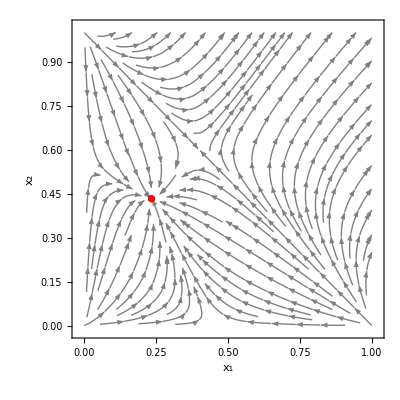

```mathematica
params={M->3,c->0.99,s->0.0005,δ1->1,δ2->-1,δ3->0}

Show[
StreamPlot[AVec[[1;;2]]/.xVec[[3]]->1-Total[xVec]+xVec[[3]]/.params,{x1,0,1},{x2,0,1},StreamStyle->Gray,FrameStyle->18,ImageSize->400,FrameLabel->{Style[Text["x_1"],24],Style[Text["x_2"],24]}],
ListPlot[{{x1,x2}}/.FP/.params,PlotStyle->{Large,Red}]
]
```

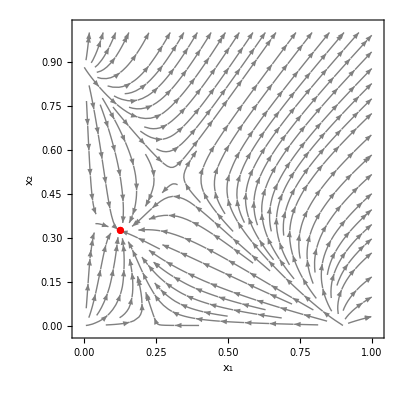

```mathematica
params={M->4,c->0.99,s->0.0005,δ1->1,δ2->-1,δ3->0,δ4->-1};

xVec=Table[ToExpression["x"<>ToString[i]],{i,1,M/.params}];
δVec=Table[ToExpression["δ"<>ToString[i]],{i,1,M/.params}];
dVec=Table[1+s*δVec[[i]],{i,1,M/.params}];

(* Define neater analytic form of deterministic dynamics to be used in paper *)
AVec=Table[Sum[xVec[[i]]xVec[[j]]((1-c)/2(xVec[[j]]-xVec[[i]])+s(1-c)/2(δVec[[i]]xVec[[j]]-δVec[[j]]xVec[[i]])+s(1+c)/2(δVec[[j]]-δVec[[i]])),{j,1,M/.params}],{i,1,M/.params}]//FullSimplify;
FP=Table[xVec[[i]]->1/M+s*(1-c-M-c*M)/(M^2(1-c))(M*δVec[[i]]-Sum[δVec[[j]],{j,1,M/.params}]),{i,1,M/.params}];

Show[
StreamPlot[AVec[[1;;2]]/.xVec[[M/.params]]->1-Total[xVec]+xVec[[M/.params]]/.xVec[[3]]->1/4/.params,{x1,0,1},{x2,0,1},StreamStyle->Gray,FrameStyle->18,ImageSize->400,FrameLabel->{Style[Text["x_1"],24],Style[Text["x_2"],24]}],
ListPlot[{{x1,x2}}/.FP/.params,PlotStyle->{Large,Red}]
]
```

## Eq. (14) - Proof of general solution of stationary distribution

## Show general form of b and d works with general solution to Master Equation

### Long form (show stationary solution is stationary solution for all states)

```mathematica
b[ni_]:=If[ni≥0&&ni≤NT-1/.NTEval,ToExpression["b"<>ToString[ni]],0];
d[nj_]:=If[nj≥1&&nj≤NT/.NTEval,ToExpression["d"<>ToString[nj]],0];

MEval=M->5;
NTEval=NT->15;

nStates=DeleteCases[Flatten[Table[If[0≤NT-i-j-q-r≤NT/.NTEval,{i,j,q,r,NT-i-j-q-r}/.NTEval,0],{i,0,NT/.NTEval},{j,0,NT/.NTEval},{q,0,NT/.NTEval},{r,0,NT/.NTEval}],3],0];
dnStates=Permutations[Join[{1,-1},ConstantArray[0,{M-2/.MEval}]]];

(* Set up master equation obeying conditions in Eq.(S3-S4) *)
MEQN=Table[
Sum[
b[ n[[Position[dn,-1][[1,1]]]]-1 ]d[n[[Position[dn,1][[1,1]]]]+1 ]P[n+dn]
,{dn,dnStates}]
-Sum[
b[ n[[Position[dn,-1][[1,1]]]]]d[n[[Position[dn,1][[1,1]]]] ]P[n]
,{dn,dnStates}]
,{n,nStates}];

(* Also implement symmetry conditions *)
pstCond=Table[P[n]->P[Sort[n,Greater]],{n,nStates}];
bCond=Table[b[NT-i/.NTEval]->b[i],{i,1,NT/2/.NTEval}];

(* Define stationary solution according to Eq.(S5) *)
pstSol=DeleteDuplicates[Table[
P[Sort[n,Greater]]->
Product[(b[k]d[NT-k/.NTEval])/(b[NT-k-1/.NTEval]d[k+1]),{k,0,Sort[n,Greater][[1]]-1}]*
Product[(b[k]d[NT-k-Sort[n,Greater][[1]]/.NTEval])/(b[NT-k-Sort[n,Greater][[1]]-1/.NTEval]d[k+1]),{k,0,Sort[n,Greater][[2]]-1}]*Product[(b[k]d[NT-k-Sort[n,Greater][[1]]-Sort[n,Greater][[2]]/.NTEval])/(b[NT-k-Sort[n,Greater][[1]]-Sort[n,Greater][[2]]-1/.NTEval]d[k+1]),{k,0,Sort[n,Greater][[3]]-1}]*Product[(b[k]d[NT-k-Sort[n,Greater][[1]]-Sort[n,Greater][[2]]-Sort[n,Greater][[3]]/.NTEval])/(b[NT-k-Sort[n,Greater][[1]]-Sort[n,Greater][[2]]-Sort[n,Greater][[3]]-1/.NTEval]d[k+1]),{k,0,Sort[n,Greater][[4]]-1}]*P[Sort[nStates[[1]],Greater]]

,{n,nStates}]];

(* Prove by substituion that this is a stationary state *)
MEQN/.pstCond/.pstSol
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Short form (show stationary solution is stationary solution for randomly selected state)

```mathematica
b[ni_]:=If[ni≥0&&ni≤NT-1/.NTEval,ToExpression["b"<>ToString[ni]],0];
d[nj_]:=If[nj≥1&&nj≤NT/.NTEval,ToExpression["d"<>ToString[nj]],0];

MEval=M->10;
NTEval=NT->100;

dnStates=Permutations[Join[{1,-1},ConstantArray[0,{M-2/.MEval}]]];


MEQNofn[n_]:=
Sum[
b[ n[[Position[dn,-1][[1,1]]]]-1 ]d[n[[Position[dn,1][[1,1]]]]+1 ]P[n+dn]
,{dn,dnStates}]-Sum[
b[ n[[Position[dn,-1][[1,1]]]]]d[n[[Position[dn,1][[1,1]]]] ]P[n]
,{dn,dnStates}];

pstCondofn[nFocal_]:=Table[P[n]->P[Sort[n,Greater]],{n,Table[nFocal+Join[dnStates,{ConstantArray[0,M/.MEval]}][[i]],{i,1,Length[dnStates]+1}]}];
bCond=Table[b[NT-i/.NTEval]->b[i],{i,1,NT/2/.NTEval}];


pstSolofn[nFocal_]:=Table[
P[Sort[n,Greater]]->Product[
Product[
(b[k]d[NT-k-Sum[n[[β]],{β,1,α-1}]/.NTEval])/(b[NT-k-Sum[n[[β]],{β,1,α-1}]-1/.NTEval]d[k+1])
,{k,0,n[[α]]-1}]
,{α,1,M-1/.MEval}]
,{n,Table[nFocal+Join[dnStates,{ConstantArray[0,M/.MEval]}][[i]],{i,1,Length[dnStates]+1}]}];
```

```mathematica
randStateVec=ConstantArray[0,M/.MEval];
While[Total[randStateVec]≠NT/.NTEval,
randStateVec=Table[RandomReal[{0,1}],{i,1,M/.MEval}];
randStateVec=Round[randStateVec/Total[randStateVec]*NT/.NTEval];
];
Total[randStateVec]

MEQNofn[randStateVec]/.pstCondofn[randStateVec]/.pstSolofn[randStateVec]//FullSimplify
```

100

0

## Fig 2: 4x4 Streamplot

```mathematica
params1={M->3,c->0,s->0.04,δ1->0.5,δ2->-1,δ3->0,NT->100};
params2={M->3,c->0.8,s->0.04,δ1->0.5,δ2->-1,δ3->0,NT->100};
params3={NT->100000,m->0.00000005,c->0,Mmax->200,M0->2};
params4={NT->100000,m->0.00000005,c->0.8,Mmax->200,M0->2};
```

## Streamplot (1a)

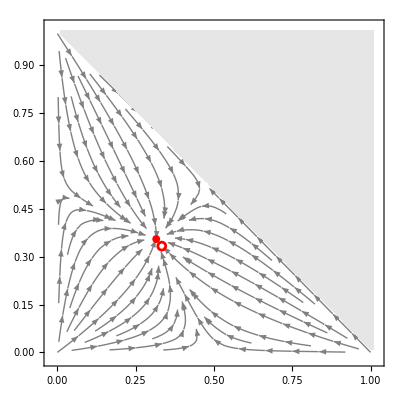

```mathematica
(* Set parameters *)
params=params1;
(* δVec = d in Main Text and SI *)
δVec=Table[ToExpression["δ"<>ToString[i]]/.params,{i,1,3}];
(* dVec = D in Main Text and SI *)
dVec=Table[1+s*δVec[[i]],{i,1,Length[δVec]}]/.params;
xVec=Table[ToExpression["x"<>ToString[i]],{i,1,Length[δVec]}];
xVecT=Table[ToExpression["x"<>ToString[i]<>"[t]"],{i,1,Length[δVec]}];
xVecTran=Table[xVec[[i]]->xVecT[[i]],{i,1,Length[δVec]}];
AVec=Table[Sum[xVec[[i]]xVec[[j]]((1-c)/2(xVec[[j]]-xVec[[i]])+s(1-c)/2(δVec[[i]]xVec[[j]]-δVec[[j]]xVec[[i]])+s(1+c)/2(δVec[[j]]-δVec[[i]]))/.params,{j,1,Length[δVec]}],{i,1,Length[δVec]}];
FP=Table[xVec[[i]]->1/M+s*(1-c-M-c*M)/(M^2(1-c))(M*δVec[[i]]-Sum[δVec[[j]],{j,1,Length[δVec]}])/.M->Length[δVec],{i,1,Length[δVec]}];

(* 
Non-neutral stable fixed point plotted as red disk 
Neutral (here unstable) fixed point plotted as red circle for reference
*)
plot1a=
Show[
StreamPlot[AVec[[1;;2]]/.xVec[[3]]->1-Total[xVec]+xVec[[3]]/.params,{x1,0,1},{x2,0,1},StreamStyle->Gray,FrameStyle->18,ImageSize->400
],
RegionPlot[x1+x2>1.01/.params,{x1,1/NT/.params,(NT+1)/NT/.params},{x2,1/NT/.params,(NT+1)/NT/.params},BoundaryStyle->None,PlotStyle->Lighter[LightGray]],
Graphics[{Red,Thickness[0.005],Circle[{1/M,1/M}/.params,0.0125]}],
Graphics[{Red,Disk[{x1,x2}/.FP/.params,0.0125]}]
]
```

## Streamplot (1b)

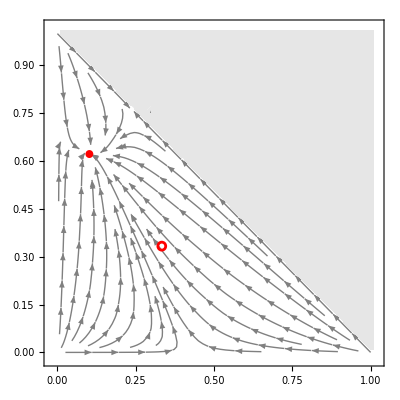

```mathematica
params=params2;
(* δVec = d in Main Text and SI *)
δVec=Table[ToExpression["δ"<>ToString[i]]/.params,{i,1,3}];
(* dVec = D in Main Text and SI *)
dVec=Table[1+s*δVec[[i]],{i,1,Length[δVec]}]/.params;
xVec=Table[ToExpression["x"<>ToString[i]],{i,1,Length[δVec]}];
xVecT=Table[ToExpression["x"<>ToString[i]<>"[t]"],{i,1,Length[δVec]}];
xVecTran=Table[xVec[[i]]->xVecT[[i]],{i,1,Length[δVec]}];
AVec=Table[Sum[xVec[[i]]xVec[[j]]((1-c)/2(xVec[[j]]-xVec[[i]])+s(1-c)/2(δVec[[i]]xVec[[j]]-δVec[[j]]xVec[[i]])+s(1+c)/2(δVec[[j]]-δVec[[i]]))/.params,{j,1,Length[δVec]}],{i,1,Length[δVec]}];
FP=Table[xVec[[i]]->1/M+s*(1-c-M-c*M)/(M^2(1-c))(M*δVec[[i]]-Sum[δVec[[j]],{j,1,Length[δVec]}])/.M->Length[δVec],{i,1,Length[δVec]}];
(* 
Non-neutral stable fixed point plotted as red disk 
Neutral (here unstable) fixed point plotted as red circle for reference
*)
plot1b=
Show[
StreamPlot[AVec[[1;;2]]/.xVec[[3]]->1-Total[xVec]+xVec[[3]]/.params,{x1,0,1},{x2,0,1},StreamStyle->Gray,FrameStyle->18,ImageSize->400
],
RegionPlot[x1+x2>1.01/.params,{x1,1/NT/.params,(NT+1)/NT/.params},{x2,1/NT/.params,(NT+1)/NT/.params},BoundaryStyle->None,PlotStyle->Lighter[LightGray]],
Graphics[{Red,Thickness[0.005],Circle[{1/M,1/M}/.params,0.0125]}],
Graphics[{Red,Disk[{x1,x2}/.FP/.params,0.0125]}]
]
```

## Densityplot (1c)

0.005

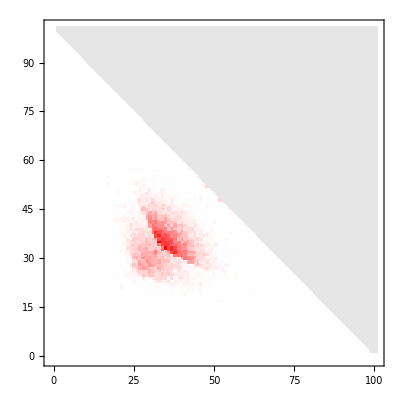

```mathematica
(* Create function that re-orders elements of n vector with largest elements first (acts as projection into 2D) *)
nArrow[n_]:=Sort[DeleteCases[n,0],Greater];

params={NT->100,m->0.00005,c->0.0,Mmax->100,mutSD->0.04};
m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=100;
minTimeStep=100;
maxTimeStep=410000;
M0=3;


paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];;

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];

(*
Now let's account for the third dimension - now we have our 3D symmetry!!!
*)

simTrajOrdered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajOrdered[[i]]=Join[simTraj[[i,1;;2]],If[Length[nArrow[simTraj[[i,3;;]]]]≥2,nArrow[simTraj[[i,3;;]]][[1;;2]],{nArrow[simTraj[[i,3;;]]][[1]],0}]];
];
PSTSimTableOrdered=DeleteCases[Flatten[Table[If[i1+i2≤NT/.params,Join[{i1,i2},{N[1/Length[Permutations[{i1,i2}]] Count[simTrajOrdered[[All,3;;4]],Sort[{i1,i2},Greater][[1;;2]]]/Length[simTrajOrdered]]}],{i1,i2,0}],{i1,0,NT/.params},{i2,0,NT/.params}],1],0];
PSTSimTableOrderedNorm=Total[PSTSimTableOrdered[[All,3]]];
For[i=1,i≤Length[PSTSimTableOrdered],i++,PSTSimTableOrdered[[i,3]]=N[PSTSimTableOrdered[[i,3]]/PSTSimTableOrderedNorm]];


barMinMax={0,1.1*Max[PSTSimTableOrdered[[All,3]]]};
barMinMax={0,0.008};

plot1c=Show[
ListDensityPlot[PSTSimTableOrdered,PlotRange->{{-1,NT+1/.params},{-1,NT+1/.params},barMinMax},InterpolationOrder->0,ImageSize->400,ColorFunctionScaling->False,ColorFunction->((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),
FrameStyle->18,ImageSize->400
],
RegionPlot[x1+x2>1.005*NT/.params,{x1,1,NT+1/.params},{x2,1,NT+1/.params},BoundaryStyle->None,PlotStyle->Lighter[LightGray]]
]

plot1cLegend=BarLegend[{((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),barMinMax},LegendMarkerSize->350,LabelStyle->18,LegendLayout->"Row"];
```

## Densityplot (1d)

0.005

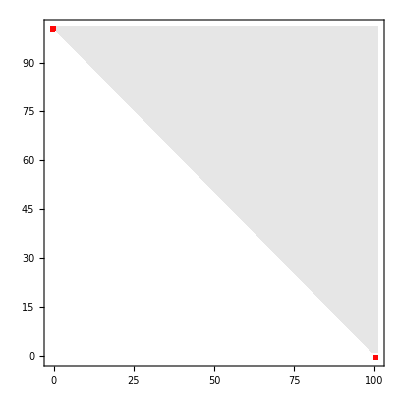

```mathematica
nArrow[n_]:=Sort[DeleteCases[n,0],Greater];

params={NT->100,m->0.00005,c->0.8,Mmax->100,mutSD->0.04};
NT*m/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=100;
minTimeStep=100;
maxTimeStep=410000;
M0=3;


paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];;

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];

(*
Now let's account for the third dimension - now we have our 3D symmetry!!!
*)

simTrajOrdered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajOrdered[[i]]=Join[simTraj[[i,1;;2]],If[Length[nArrow[simTraj[[i,3;;]]]]≥2,nArrow[simTraj[[i,3;;]]][[1;;2]],{nArrow[simTraj[[i,3;;]]][[1]],0}]];
];
PSTSimTableOrdered=DeleteCases[Flatten[Table[If[i1+i2≤NT/.params,Join[{i1,i2},{N[1/Length[Permutations[{i1,i2}]] Count[simTrajOrdered[[All,3;;4]],Sort[{i1,i2},Greater][[1;;2]]]/Length[simTrajOrdered]]}],{i1,i2,0}],{i1,0,NT/.params},{i2,0,NT/.params}],1],0];
PSTSimTableOrderedNorm=Total[PSTSimTableOrdered[[All,3]]];
For[i=1,i≤Length[PSTSimTableOrdered],i++,PSTSimTableOrdered[[i,3]]=N[PSTSimTableOrdered[[i,3]]/PSTSimTableOrderedNorm]];

barMinMax={0,1.1*Max[PSTSimTableOrdered[[All,3]]]};
barMinMax={0,0.5};

plot1d=Show[
ListDensityPlot[PSTSimTableOrdered,PlotRange->{{-1,NT+1/.params},{-1,NT+1/.params},barMinMax},InterpolationOrder->0,ImageSize->400,ColorFunctionScaling->False,ColorFunction->((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),
FrameStyle->18,ImageSize->400],
RegionPlot[x1+x2>1.005*NT/.params,{x1,1,NT+1/.params},{x2,1,NT+1/.params},BoundaryStyle->None,PlotStyle->Lighter[LightGray]]
]


plot1dLegend=BarLegend[{((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),barMinMax},LegendMarkerSize->350,LabelStyle->18,LegendLayout->"Row"];
```

## Fig 3: 4x4 M vs τ plot

```mathematica
(* Set up parameters *)
Clear[M0,mg];
params1={NT->100000,m->0.0000005,c->0,Mmax->200,M0->2};
params2={NT->100000,m->0.0000005,c->0.8,Mmax->200,M0->2};
params3={NT->100000,m->0.00000005,c->0,Mmax->200,M0->2};
params4={NT->100000,m->0.00000005,c->0.8,Mmax->200,M0->2};
sParam={s->0.04};
NT*m/.params1
NT*m/.params3

minTimeStep=0;
maxTimeStep=10000;

maxTimeStep*NT*m/.params1
maxTimeStep*NT*m/.params3
```

0.05

0.005

500.

50.

## Neutral deterministic plot (a)

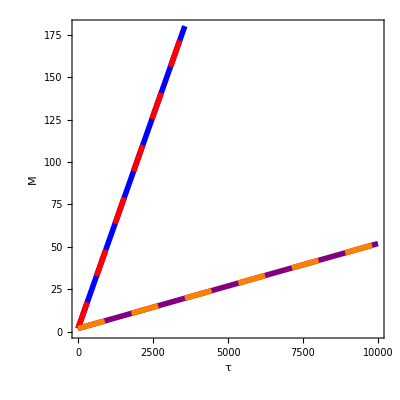

```mathematica
Plot[Evaluate[{
M0+mg*t/.mg->m*NT/.params1,
M0+mg*t/.mg->m*NT/.params2,
M0+mg*t/.mg->m*NT/.params3,
M0+mg*t/.mg->m*NT/.params4
}],{t,0,maxTimeStep},AxesOrigin->{0,0},PlotRange->{0,180},AspectRatio->1,Frame->True,FrameStyle->18,ImageSize->400,FrameLabel->{Style[Text["τ"],24],Style[Text["M"],24]},
PlotStyle->{Directive[Thickness[0.01],Blue],Directive[Thickness[0.01],Dashing[0.05],Red],Directive[Thickness[0.01],Purple],Directive[Thickness[0.01],Dashing[0.05],Orange]}
]
```

## Non-Neutral deterministic plot (b) using ODE solutions (pre-generated ode)

### Params 1

```mathematica
params=Join[params1,{s->0.02}];

MTrajDet1=Table[{i/mg,0}/.mg->m*NT/.params,{i,0,Round[maxTimeStep*mg/.mg->m*NT/.params]}];

(* Pre-generate a large set of alleles of different fitness' *)

δVec=Join[{0,0},RandomVariate[NormalDistribution[0,1],Length[MTrajDet1]]];
xVec=Table[ToExpression["x"<>ToString[i]],{i,1,Length[δVec]}];
xVecT=Table[ToExpression["x"<>ToString[i]<>"[t]"],{i,1,Length[δVec]}];
xVecTran=Table[xVec[[i]]->xVecT[[i]],{i,1,Length[δVec]}];
dVec=Table[1+s*δVec[[i]],{i,1,Length[δVec]}]/.params;
AVec=Table[Sum[xVec[[i]]xVec[[j]]((1-c)/2(xVec[[j]]-xVec[[i]])+s(1-c)/2(δVec[[i]]xVec[[j]]-δVec[[j]]xVec[[i]])+s(1+c)/2(δVec[[j]]-δVec[[i]]))/.params,{j,1,Length[δVec]}],{i,1,Length[δVec]}];
eqns=Table[D[xVecT[[i]],t]==(AVec[[i]]/.xVecTran),{i,1,Length[δVec]}];

relaxTime=2000;

xFinal=Join[{0.5,0.5},ConstantArray[0,Length[MTrajDet1]]];

For[i=1,i≤Length[MTrajDet1],i++,

MTrajDet1[[i,2]]=Length[Select[xFinal,#>10^-6&]];
Print[MTrajDet1[[i,2]]];

j=1;
While[xFinal[[j]]<1/NT/.params,j++];
xFinal[[j]]=xFinal[[j]]-1/NT/.params;
xFinal[[i+2]]=1/NT/.params;

nSol=NDSolve[
Join[
eqns,
Table[(xVecT[[k]]/.t->0)==xFinal[[k]],{k,1,Length[δVec]}]
],
xVec,
{t,0,relaxTime},Method->{"EquationSimplification"->"Residual"}
];
xFinal=xVecT/.nSol[[1]]/.t->relaxTime;

For[j=1,j≤Length[xFinal],j++,If[xFinal[[j]]<10^-6,xFinal[[j]]=0]];
(*xFinal=DeleteCases[xFinal,0];*)
xFinal=xFinal/Total[xFinal];

];
```

2

3

4

5

$Aborted

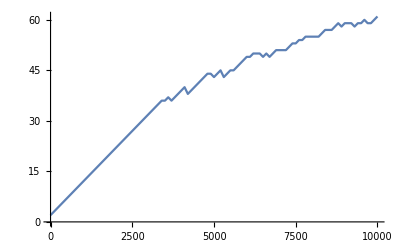

```mathematica
ListLinePlot[MTrajDet1]
```

### Params 2

```mathematica
params=Join[params2,{s->0.02}];

MTrajDet2=Table[{i/mg,0}/.mg->m*NT/.params,{i,0,Round[maxTimeStep*mg/.mg->m*NT/.params]}]

δVec=Join[{0,0},RandomVariate[NormalDistribution[0,1],Length[MTrajDet2]]];
xVec=Table[ToExpression["x"<>ToString[i]],{i,1,Length[δVec]}];
xVecT=Table[ToExpression["x"<>ToString[i]<>"[t]"],{i,1,Length[δVec]}];
xVecTran=Table[xVec[[i]]->xVecT[[i]],{i,1,Length[δVec]}];
dVec=Table[1+s*δVec[[i]],{i,1,Length[δVec]}]/.params;
AVec=Table[Sum[xVec[[i]]xVec[[j]]((1-c)/2(xVec[[j]]-xVec[[i]])+s(1-c)/2(δVec[[i]]xVec[[j]]-δVec[[j]]xVec[[i]])+s(1+c)/2(δVec[[j]]-δVec[[i]]))/.params,{j,1,Length[δVec]}],{i,1,Length[δVec]}];
eqns=Table[D[xVecT[[i]],t]==(AVec[[i]]/.xVecTran),{i,1,Length[δVec]}];

relaxTime=2000;

xFinal=Join[{0.5,0.5},ConstantArray[0,Length[MTrajDet2]]];

For[i=1,i≤Length[MTrajDet2],i++,

MTrajDet2[[i,2]]=Length[Select[xFinal,#>10^-6&]];
Print[MTrajDet2[[i,2]]];

j=1;
While[xFinal[[j]]<1/NT/.params,j++];
xFinal[[j]]=xFinal[[j]]-1/NT/.params;
xFinal[[i+2]]=1/NT/.params;

nSol=NDSolve[
Join[
eqns,
Table[(xVecT[[k]]/.t->0)==xFinal[[k]],{k,1,Length[δVec]}]
],
xVec,
{t,0,relaxTime},Method->{"EquationSimplification"->"Residual"}
];
xFinal=xVecT/.nSol[[1]]/.t->relaxTime;

For[j=1,j≤Length[xFinal],j++,If[xFinal[[j]]<10^-6,xFinal[[j]]=0]];
xFinal=xFinal/Total[xFinal];

];
```

{{0,0},{1000.,0},{2000.,0},{3000.,0},{4000.,0},{5000.,0},{6000.,0},{7000.,0},{8000.,0},{9000.,0},{10000.,0},{11000.,0},{12000.,0},{13000.,0},{14000.,0},{15000.,0},{16000.,0},{17000.,0},{18000.,0},{19000.,0},{20000.,0},{21000.,0},{22000.,0},{23000.,0},{24000.,0},{25000.,0},{26000.,0},{27000.,0},{28000.,0},{29000.,0},{30000.,0},{31000.,0},{32000.,0},{33000.,0},{34000.,0},{35000.,0},{36000.,0},{37000.,0},{38000.,0},{39000.,0},{40000.,0},{41000.,0},{42000.,0},{43000.,0},{44000.,0},{45000.,0},{46000.,0},{47000.,0},{48000.,0},{49000.,0},{50000.,0},{51000.,0},{52000.,0},{53000.,0},{54000.,0},{55000.,0},{56000.,0},{57000.,0},{58000.,0},{59000.,0},{60000.,0},{61000.,0},{62000.,0},{63000.,0},{64000.,0},{65000.,0},{66000.,0},{67000.,0},{68000.,0},{69000.,0},{70000.,0},{71000.,0},{72000.,0},{73000.,0},{74000.,0},{75000.,0},{76000.,0},{77000.,0},{78000.,0},{79000.,0},{80000.,0},{81000.,0},{82000.,0},{83000.,0},{84000.,0},{85000.,0},{86000.,0},{87000.,0},{88000.,0},{89000.,0},{90000.,0},{91000.,0},{92000.,0},{93000.,0},{94000.,0},{95000.,0},{96000.,0},{97000.,0},{98000.,0},{99000.,0},{100000.,0}}

{x1'[t]==x1[t] x10[t] (0.00493109-0.000547899 x1[t]+0.1 (-x1[t]+x10[t]))+x1[t] x100[t] (-0.0283639+0.00315154 x1[t]+0.1 (-x1[t]+x100[t]))+x1[t] x101[t] (-0.000790634+0.0000878482 x1[t]+0.1 (-x1[t]+x101[t]))+96+x1[t] x97[t] (-0.0134897+0.00149886 x1[t]+0.1 (-x1[t]+x97[t]))+x1[t] x98[t] (0.0295036-0.00327818 x1[t]+0.1 (-x1[t]+x98[t]))+x1[t] x99[t] (-0.0240876+0.00267639 x1[t]+0.1 (-x1[t]+x99[t])),101,x103'[t]==0.+101+x103[t] x99[t] (-0.00217898+1+0.1 (1))}
 |  |  |  |

2

3

4

4

5

6

7

8

9

9

10

10

10

8

9

9

8

8

8

«3 more identical outputs»

9

9

9

«2 more identical outputs»

10

10

9

9

9

«1 more identical outputs»

10

10

9

9

9

10

10

10

«4 more identical outputs»

11

11

11

12

12

12

«1 more identical outputs»

11

11

11

«13 more identical outputs»

12

11

11

12

12

12

«14 more identical outputs»

13

13

12

13

14

14

14

«2 more identical outputs»

15

16

15

15

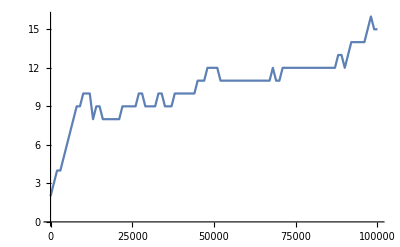

```mathematica
ListLinePlot[MTrajDet2]
```

### Params 3

```mathematica
params=Join[params3,{s->0.02}];

MTrajDet3=Table[{i/mg,0}/.mg->m*NT/.params,{i,0,Round[maxTimeStep*mg/.mg->m*NT/.params]}]

δVec=Join[{0,0},RandomVariate[NormalDistribution[0,1],Length[MTrajDet3]]];
xVec=Table[ToExpression["x"<>ToString[i]],{i,1,Length[δVec]}];
xVecT=Table[ToExpression["x"<>ToString[i]<>"[t]"],{i,1,Length[δVec]}];
xVecTran=Table[xVec[[i]]->xVecT[[i]],{i,1,Length[δVec]}];
dVec=Table[1+s*δVec[[i]],{i,1,Length[δVec]}]/.params;
AVec=Table[Sum[xVec[[i]]xVec[[j]]((1-c)/2(xVec[[j]]-xVec[[i]])+s(1-c)/2(δVec[[i]]xVec[[j]]-δVec[[j]]xVec[[i]])+s(1+c)/2(δVec[[j]]-δVec[[i]]))/.params,{j,1,Length[δVec]}],{i,1,Length[δVec]}];
eqns=Table[D[xVecT[[i]],t]==(AVec[[i]]/.xVecTran),{i,1,Length[δVec]}]

relaxTime=2000;

xFinal=Join[{0.5,0.5},ConstantArray[0,Length[MTrajDet3]]];

For[i=1,i≤Length[MTrajDet3],i++,

MTrajDet3[[i,2]]=Length[Select[xFinal,#>10^-6&]];
Print[MTrajDet3[[i,2]]];

j=1;
While[xFinal[[j]]<1/NT/.params,j++];
xFinal[[j]]=xFinal[[j]]-1/NT/.params;
xFinal[[i+2]]=1/NT/.params;

nSol=NDSolve[
Join[
eqns,
Table[(xVecT[[k]]/.t->0)==xFinal[[k]],{k,1,Length[δVec]}]
],
xVec,
{t,0,relaxTime},Method->{"EquationSimplification"->"Residual"}
];
xFinal=xVecT/.nSol[[1]]/.t->relaxTime;

For[j=1,j≤Length[xFinal],j++,If[xFinal[[j]]<10^-6,xFinal[[j]]=0]];
xFinal=xFinal/Total[xFinal];

];
```

{{0,0},{2000.,0},{4000.,0},{6000.,0},{8000.,0},{10000.,0},{12000.,0},{14000.,0},{16000.,0},{18000.,0},{20000.,0},{22000.,0},{24000.,0},{26000.,0},{28000.,0},{30000.,0},{32000.,0},{34000.,0},{36000.,0},{38000.,0},{40000.,0},{42000.,0},{44000.,0},{46000.,0},{48000.,0},{50000.,0},{52000.,0},{54000.,0},{56000.,0},{58000.,0},{60000.,0},{62000.,0},{64000.,0},{66000.,0},{68000.,0},{70000.,0},{72000.,0},{74000.,0},{76000.,0},{78000.,0},{80000.,0},{82000.,0},{84000.,0},{86000.,0},{88000.,0},{90000.,0},{92000.,0},{94000.,0},{96000.,0},{98000.,0},{100000.,0}}

{x1'[t]==x1[t] x10[t] (-0.00167626+0.00167626 x1[t]+1/2 (-x1[t]+x10[t]))+x1[t] x11[t] (0.0196933-0.0196933 x1[t]+1/2 (-x1[t]+x11[t]))+x1[t] x12[t] (-0.00548559+0.00548559 x1[t]+1/2 (-x1[t]+x12[t]))+x1[t] x13[t] (-0.0151656+0.0151656 x1[t]+1/2 (-x1[t]+x13[t]))+44+x1[t] x6[t] (-0.011918+0.011918 x1[t]+1/2 (-x1[t]+x6[t]))+x1[t] x7[t] (0.011792-0.011792 x1[t]+1/2 (-x1[t]+x7[t]))+x1[t] x8[t] (-0.00936397+0.00936397 x1[t]+1/2 (-x1[t]+x8[t]))+x1[t] x9[t] (-0.00217813+0.00217813 x1[t]+1/2 (-x1[t]+x9[t])),x2'[t]==1,50,x53'[t]==0.+51+x53[t] x9[t] (1)}
 |  |  |  |

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

28

29

29

29

30

30

31

32

33

34

35

36

37

38

39

40

40

41

42

42

43

43

44

43

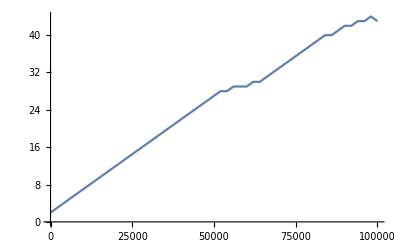

```mathematica
ListLinePlot[MTrajDet3]
```

### Params 4

```mathematica
params=Join[params4,{s->0.02}];

MTrajDet4=Table[{i/mg,0}/.mg->m*NT/.params,{i,0,Round[maxTimeStep*mg/.mg->m*NT/.params]}]

δVec=Join[{0,0},RandomVariate[NormalDistribution[0,1],Length[MTrajDet4]]];
xVec=Table[ToExpression["x"<>ToString[i]],{i,1,Length[δVec]}];
xVecT=Table[ToExpression["x"<>ToString[i]<>"[t]"],{i,1,Length[δVec]}];
xVecTran=Table[xVec[[i]]->xVecT[[i]],{i,1,Length[δVec]}];
dVec=Table[1+s*δVec[[i]],{i,1,Length[δVec]}]/.params;
AVec=Table[Sum[xVec[[i]]xVec[[j]]((1-c)/2(xVec[[j]]-xVec[[i]])+s(1-c)/2(δVec[[i]]xVec[[j]]-δVec[[j]]xVec[[i]])+s(1+c)/2(δVec[[j]]-δVec[[i]]))/.params,{j,1,Length[δVec]}],{i,1,Length[δVec]}];
eqns=Table[D[xVecT[[i]],t]==(AVec[[i]]/.xVecTran),{i,1,Length[δVec]}];

relaxTime=2000;

xFinal=Join[{0.5,0.5},ConstantArray[0,Length[MTrajDet4]]];

For[i=1,i≤Length[MTrajDet4],i++,

MTrajDet4[[i,2]]=Length[Select[xFinal,#>10^-6&]];
Print[MTrajDet4[[i,2]]];

j=1;
While[xFinal[[j]]<1/NT/.params,j++];
xFinal[[j]]=xFinal[[j]]-1/NT/.params;
xFinal[[i+2]]=1/NT/.params;

nSol=NDSolve[
Join[
eqns,
Table[(xVecT[[k]]/.t->0)==xFinal[[k]],{k,1,Length[δVec]}]
],
xVec,
{t,0,relaxTime},Method->{"EquationSimplification"->"Residual"}
];
xFinal=xVecT/.nSol[[1]]/.t->relaxTime;

For[j=1,j≤Length[xFinal],j++,If[xFinal[[j]]<10^-6,xFinal[[j]]=0]];
xFinal=xFinal/Total[xFinal];

];
```

{{0,0},{200.,0},{400.,0},{600.,0},{800.,0},{1000.,0},{1200.,0},{1400.,0},{1600.,0},{1800.,0},{2000.,0},{2200.,0},{2400.,0},{2600.,0},{2800.,0},{3000.,0},{3200.,0},{3400.,0},{3600.,0},{3800.,0},{4000.,0},{4200.,0},{4400.,0},{4600.,0},{4800.,0},{5000.,0},{5200.,0},{5400.,0},{5600.,0},{5800.,0},{6000.,0},{6200.,0},{6400.,0},{6600.,0},{6800.,0},{7000.,0},{7200.,0},{7400.,0},{7600.,0},{7800.,0},{8000.,0},{8200.,0},{8400.,0},{8600.,0},{8800.,0},{9000.,0},{9200.,0},{9400.,0},{9600.,0},{9800.,0},{10000.,0}}

{x1'[t]==x1[t] x10[t] (0.0397121-0.00441245 x1[t]+0.1 (-x1[t]+x10[t]))+x1[t] x11[t] (0.0105763-0.00117514 x1[t]+0.1 (-x1[t]+x11[t]))+x1[t] x12[t] (-0.0126379+0.00140421 x1[t]+0.1 (-x1[t]+x12[t]))+x1[t] x13[t] (0.0149029-0.00165588 x1[t]+0.1 (-x1[t]+x13[t]))+45+x1[t] x7[t] (0.021178-0.00235311 x1[t]+0.1 (-x1[t]+x7[t]))+x1[t] x8[t] (-0.0218706+0.00243007 x1[t]+0.1 (-x1[t]+x8[t]))+x1[t] x9[t] (-0.00964462+0.00107162 x1[t]+0.1 (-x1[t]+x9[t])),51,x53'[t]==0.+52}
 |  |  |  |

2

3

4

5

6

6

7

8

8

9

9

9

10

9

9

9

10

10

10

7

7

8

9

9

9

«2 more identical outputs»

10

10

9

10

10

10

«3 more identical outputs»

11

11

11

12

11

11

11

«2 more identical outputs»

12

12

12

«3 more identical outputs»

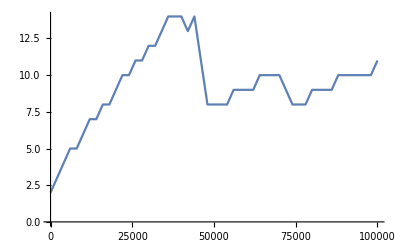

```mathematica
ListLinePlot[MTrajDet4]
```

### Combine plots

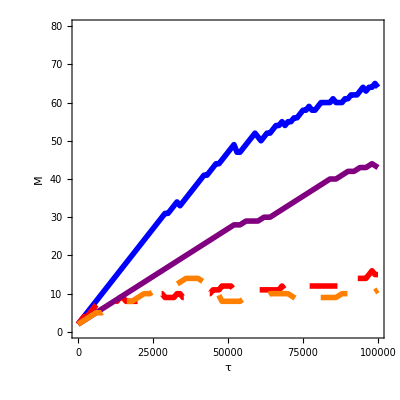

```mathematica
ListLinePlot[Evaluate[{
MTrajDet1,
MTrajDet2,
MTrajDet3,
MTrajDet4
}],AxesOrigin->{0,0},PlotRange->{0,80},AspectRatio->1,Frame->True,FrameStyle->18,ImageSize->400,FrameLabel->{Style[Text["τ"],24],Style[Text["M"],24]},
PlotStyle->{Directive[Thickness[0.01],Blue],Directive[Thickness[0.01],Dashing[0.05],Red],Directive[Thickness[0.01],Purple],Directive[Thickness[0.01],Dashing[0.05],Orange]}
]
```

## Neutral stochastic plot (c)

### Params 1

```mathematica
params=Join[params1,{mutSD->0}];
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=1;

M0=2;

(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];

MTrajStoch1=simTraj[[All,1;;2]];
```

0.05

500.

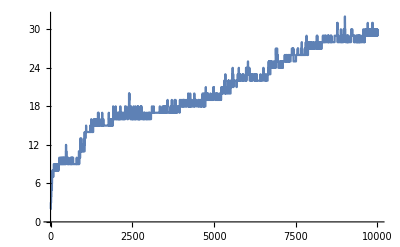

```mathematica
ListLinePlot[MTrajStoch1]
```

### Params 2

```mathematica
params=Join[params2,{mutSD->0}];
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=1;

M0=2;

(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];

MTrajStoch2=simTraj[[All,1;;2]];
```

0.05

500.

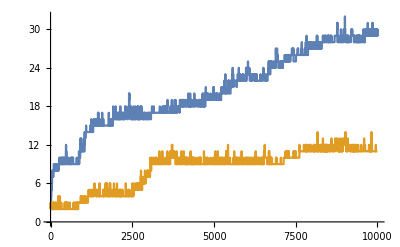

```mathematica
ListLinePlot[{MTrajStoch1,MTrajStoch2}]
```

### Params 3

```mathematica
params=Join[params3,{mutSD->0}];
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=1;

M0=2;

(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];

MTrajStoch3=simTraj[[All,1;;2]];
```

0.005

50.

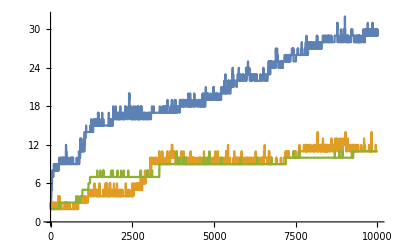

```mathematica
ListLinePlot[{MTrajStoch1,MTrajStoch2,MTrajStoch3}]
```

### Params 4

```mathematica
params=Join[params4,{mutSD->0}];
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=1;

M0=2;

(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];

MTrajStoch4=simTraj[[All,1;;2]];
```

0.005

50.

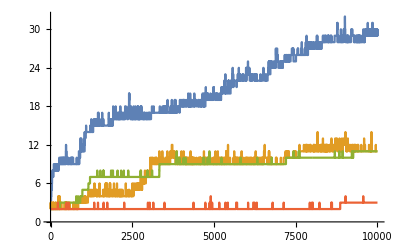

```mathematica
ListLinePlot[{MTrajStoch1,MTrajStoch2,MTrajStoch3,MTrajStoch4}]
```

## Non-neutral stochastic plot (d)

### Params 1

```mathematica
params=Join[params1,{mutSD->s/.sParam}];
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=1;

M0=2;

(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];

MTrajStoch1=simTraj[[All,1;;2]];
```

0.05

500.

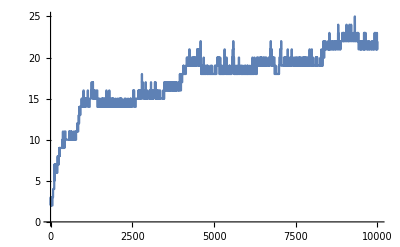

```mathematica
ListLinePlot[MTrajStoch1]
```

### Params 2

```mathematica
params=Join[params2,{mutSD->s/.sParam}];
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=1;

M0=2;

(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];

MTrajStoch2=simTraj[[All,1;;2]];
```

0.05

500.

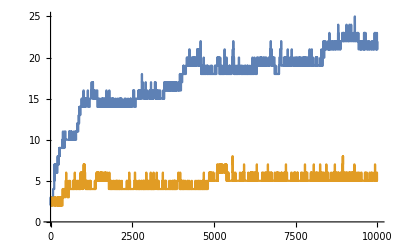

```mathematica
ListLinePlot[{MTrajStoch1,MTrajStoch2}]
```

### Params 3

```mathematica
params=Join[params3,{mutSD->s/.sParam}];
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=1;

M0=2;

(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];

MTrajStoch3=simTraj[[All,1;;2]];
```

0.005

50.

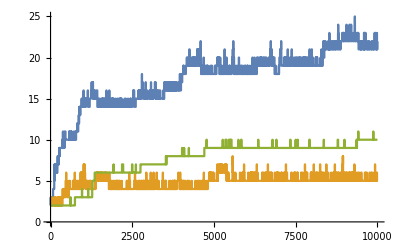

```mathematica
ListLinePlot[{MTrajStoch1,MTrajStoch2,MTrajStoch3}]
```

### Params 4

```mathematica
params=Join[params4,{mutSD->s/.sParam}];
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=1;

M0=2;

(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];

MTrajStoch4=simTraj[[All,1;;2]];
```

0.005

50.

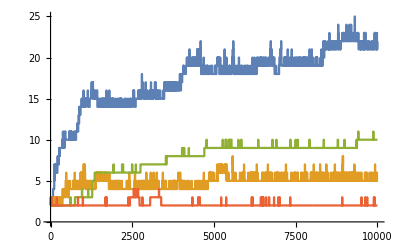

```mathematica
ListLinePlot[{MTrajStoch1,MTrajStoch2,MTrajStoch3,MTrajStoch4}]
```

## Load data and combine plots

```mathematica
dataPlotAParams1=Import[NotebookDirectory[]<>"Fig3Data/PlotA/params1.txt","Table"];
dataPlotAParams2=Import[NotebookDirectory[]<>"Fig3Data/PlotA/params2.txt","Table"];
dataPlotAParams3=Import[NotebookDirectory[]<>"Fig3Data/PlotA/params3.txt","Table"];
dataPlotAParams4=Import[NotebookDirectory[]<>"Fig3Data/PlotA/params4.txt","Table"];

dataPlotBParams1=Import[NotebookDirectory[]<>"Fig3Data/PlotB/params1.txt","Table"];
dataPlotBParams2=Import[NotebookDirectory[]<>"Fig3Data/PlotB/params2.txt","Table"];
dataPlotBParams3=Import[NotebookDirectory[]<>"Fig3Data/PlotB/params3.txt","Table"];
dataPlotBParams4=Import[NotebookDirectory[]<>"Fig3Data/PlotB/params4.txt","Table"];

dataPlotCParams1=Import[NotebookDirectory[]<>"Fig3Data/PlotC/params1.txt","Table"];
dataPlotCParams2=Import[NotebookDirectory[]<>"Fig3Data/PlotC/params2.txt","Table"];
dataPlotCParams3=Import[NotebookDirectory[]<>"Fig3Data/PlotC/params3.txt","Table"];
dataPlotCParams4=Import[NotebookDirectory[]<>"Fig3Data/PlotC/params4.txt","Table"];

dataPlotDParams1=Import[NotebookDirectory[]<>"Fig3Data/PlotD/params1.txt","Table"];
dataPlotDParams2=Import[NotebookDirectory[]<>"Fig3Data/PlotD/params2.txt","Table"];
dataPlotDParams3=Import[NotebookDirectory[]<>"Fig3Data/PlotD/params3.txt","Table"];
dataPlotDParams4=Import[NotebookDirectory[]<>"Fig3Data/PlotD/params4.txt","Table"];
```

```mathematica
MRangePlot={0,40};

plotA=ListLinePlot[Evaluate[{dataPlotAParams1,dataPlotAParams2,dataPlotAParams3,dataPlotAParams4}],PlotRange->MRangePlot,Frame->True,ImageSize->400,FrameStyle->18,
PlotStyle->{Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]]],Directive[Thickness[0.01],Dashing[0.05],ColorData[97,"ColorList"][[2]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[3]]],Directive[Thickness[0.01],Dashing[0.05],ColorData[97,"ColorList"][[4]]]}];

plotB=ListLinePlot[Evaluate[{dataPlotBParams1,dataPlotBParams2,dataPlotBParams3,dataPlotBParams4}],PlotRange->MRangePlot,Frame->True,ImageSize->400,FrameStyle->18,
PlotStyle->{Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]]],Directive[Thickness[0.01],Dashing[0.05],ColorData[97,"ColorList"][[2]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[3]]],Directive[Thickness[0.01],Dashing[0.05],ColorData[97,"ColorList"][[4]]]}];

plotC=ListLinePlot[Evaluate[{dataPlotCParams1,dataPlotCParams2,dataPlotCParams3,dataPlotCParams4}],PlotRange->MRangePlot,Frame->True,ImageSize->400,FrameStyle->18,
PlotStyle->{Directive[Thickness[0.005],ColorData[97,"ColorList"][[1]]],Directive[Thickness[0.005],Dashing[0.05],ColorData[97,"ColorList"][[2]]],Directive[Thickness[0.005],ColorData[97,"ColorList"][[3]]],Directive[Thickness[0.005],Dashing[0.05],ColorData[97,"ColorList"][[4]]]}];

plotD=ListLinePlot[Evaluate[{dataPlotDParams1,dataPlotDParams2,dataPlotDParams3,dataPlotDParams4}],PlotRange->MRangePlot,Frame->True,ImageSize->400,FrameStyle->18,
PlotStyle->{Directive[Thickness[0.005],ColorData[97,"ColorList"][[1]]],Directive[Thickness[0.005],Dashing[0.05],ColorData[97,"ColorList"][[2]]],Directive[Thickness[0.005],ColorData[97,"ColorList"][[3]]],Directive[Thickness[0.005],Dashing[0.05],ColorData[97,"ColorList"][[4]]]}];

legend=LineLegend[{Directive[Thickness[0.005],ColorData[97,"ColorList"][[1]]],Directive[Thickness[0.005],Dashing[0.025],ColorData[97,"ColorList"][[2]]],Directive[Thickness[0.005],ColorData[97,"ColorList"][[3]]],Directive[Thickness[0.005],Dashing[0.025],ColorData[97,"ColorList"][[4]]]},{1,2,3,4}];
```

## Fig 4: Predicted number of mating types

## obligate sex

```mathematica
(* Set up equations for critical mutation rate at which expected number of mating types (M) increases by one as a function of M (original number of mating types) *)
mgCritLBApprox[M_]=If[M==2,2^(-5/2-NT) NT^(3/2) √π,1/2 ⅇ^NT (M/(-1+M))^(1-M) NT^(1/2-NT) (ⅇ^(-((-2+M) NT)/(-1+M)) (((-2+M) NT)/(-1+M))^(1/2+((-2+M) NT)/(-1+M)))^(1-M) (ⅇ^((-1+1/M) NT) (((-1+M) NT)/M)^(1/2+NT-NT/M))^M];

mgCritUBApprox[M_]=(NT/(M-1)-1)^-1*If[M==2,2^(-5/2-NT) NT^(3/2) √π,1/2 ⅇ^NT (M/(-1+M))^(1-M) NT^(1/2-NT) (ⅇ^(-((-2+M) NT)/(-1+M)) (((-2+M) NT)/(-1+M))^(1/2+((-2+M) NT)/(-1+M)))^(1-M) (ⅇ^((-1+1/M) NT) (((-1+M) NT)/M)^(1/2+NT-NT/M))^M];

NTMAX=10^7;
dNT=10^5/2;

mgMin=10^-9;
mgMax=10^-2;

NTMin=10^5;

MRange={2,100,200,300,400};
MIsoclines={2,100,200,300,400};



mgCritLBApproxIsoclinesTable=Table[Table[N[{iNT,mgCritLBApprox[M]}],{M,MIsoclines}],{iNT,NTMin,NTMAX+NTMin,dNT}];
mgCritUBApproxIsoclinesTable=Table[Table[N[{iNT,mgCritUBApprox[M]}],{M,MIsoclines}],{iNT,NTMin,NTMAX+NTMin,dNT}];
```

### Calculate density plot data: LogLogScale

```mathematica
NTMAX=10^7;
NTMin=10^5;

mgMin=10^-9;
mgMax=10^-2;

MDensityTable=Flatten[Table[Table[{N[logNT],N[logmg],0},{logNT,Log[NTMin],Log[NTMAX+NTMin],Abs[(Log[NTMAX+NTMin]-Log[NTMin])/40]}],{logmg,Log[mgMin],Log[mgMax],Abs[(Log[mgMin]-Log[mgMax])/40]}],1];

For[k=1,k≤Length[MDensityTable],k++,

(* Initialize logNT and logmg parameters for each run *)
logNT=MDensityTable[[k,1]];
logmg=MDensityTable[[k,2]];

(* If this is the beginning of an NT cycle, set MminNTPrev to 0*)
If[logNT==Log[NTMin],MminNTPrev=2];

(* Generate a long list starting with the minimum value we know M must have *)
mLBCritList=Table[{M,0},{M,MminNTPrev,1000}];

(* populate the first mgCrit value (probably quite low initiall for low NT) *)
mLBCritList[[1,2]]=N[mgCritLBApprox[  mLBCritList[[1,1]]  ]/.{NT->Exp[logNT]}];

(* run over values of M and populate mgCrit values, but stop doing this if mcrit is higher than what we're plotting *)
i=2;
While[mLBCritList[[i-1,2]]<mgMax,
mLBCritList[[i,2]]=N[mgCritLBApprox[  mLBCritList[[i,1]]  ]/.{NT->Exp[logNT]}];
i++;
];

(* shorten mLBCritList so that it only contains the values of mgCrit_ that we're plotting over *)
mLBCritList=Delete[mLBCritList,Position[mLBCritList[[All,2]],0] ];

(* Loop over mg to find where mg intersects the mgCrit list. This tells us the bound of M ... *)
j=1;
While[mLBCritList[[j,2]]<Exp[logmg],j++];

MDensityTable[[k,3]]=mLBCritList[[j-1,1]];
MminNTPrev=mLBCritList[[j-1,1]];


]
```

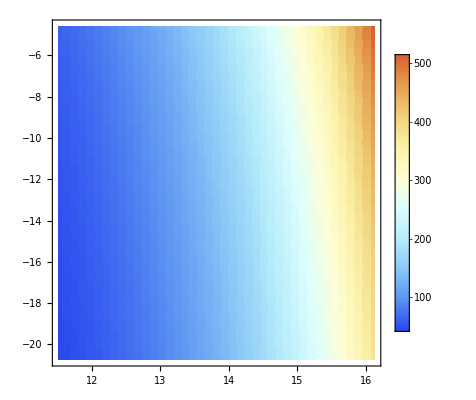

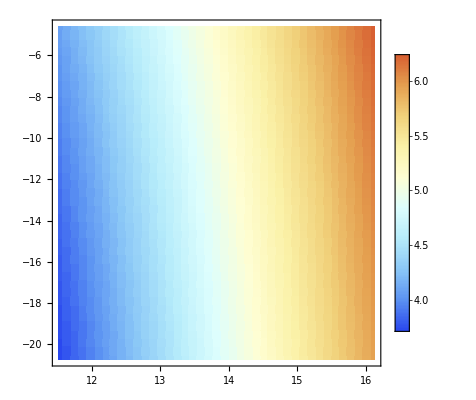

```mathematica
ListDensityPlot[MDensityTable,InterpolationOrder->0,PlotLegends->Automatic,ColorFunction->"LightTemperatureMap"]
ListDensityPlot[
Table[{MDensityTable[[i,1]],MDensityTable[[i,2]],Log[MDensityTable[[i,3]]]},{i,1,Length[MDensityTable]}],
InterpolationOrder->0,PlotLegends->Automatic,ColorFunction->"LightTemperatureMap"]
```

### Check critical mutation rate result against analytic result in text (see Eq.(3) )

```mathematica
NTMAX=10^7;
NTMin=10^5;

mgMin=10^-9;
mgMax=10^-2;

MDensityTable=Flatten[Table[Table[{N[logNT],N[logmg],0},{logNT,Log[NTMin],Log[NTMAX+NTMin],Abs[(Log[NTMAX+NTMin]-Log[NTMin])/40]}],{logmg,Log[mgMin],Log[mgMax],Abs[(Log[mgMin]-Log[mgMax])/40]}],1];

For[k=1,k≤Length[MDensityTable],k++,

(* Initialize logNT and logmg parameters for each run *)
logNT=MDensityTable[[k,1]];
logmg=MDensityTable[[k,2]];

MDensityTable[[k,3]]=√(-NT/(2(1+Log[2m])))/.{m->mg/NT}/.{NT->Exp[logNT],mg->Exp[logmg]};
]
```

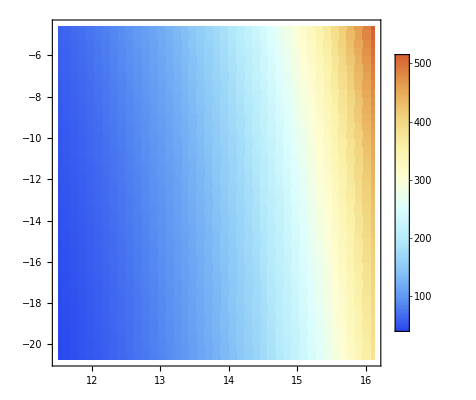

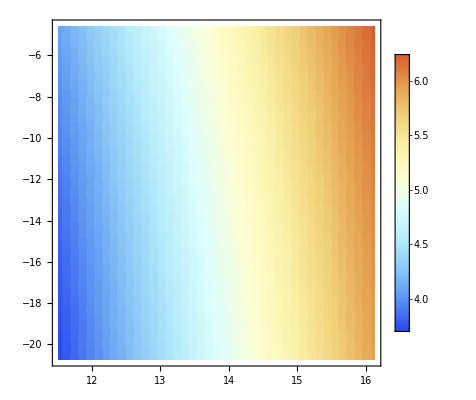

17.289

```mathematica
ListDensityPlot[MDensityTable,InterpolationOrder->0,PlotLegends->Automatic,ColorFunction->"LightTemperatureMap"]
ListDensityPlot[
Table[{MDensityTable[[i,1]],MDensityTable[[i,2]],Log[MDensityTable[[i,3]]]},{i,1,Length[MDensityTable]}],
InterpolationOrder->0,PlotLegends->Automatic,ColorFunction->"LightTemperatureMap"]
```

### Calculate density plot data: LogLogScale LB

```mathematica
NTMAX=10^7;
NTMin=10^5;

mgMin=10^-9;
mgMax=10^-2;

MDensityTable=Flatten[Table[Table[{N[logNT],N[logmg],0},{logNT,Log[NTMin],Log[NTMAX+NTMin],Abs[(Log[NTMAX+NTMin]-Log[NTMin])/40]}],{logmg,Log[mgMin],Log[mgMax],Abs[(Log[mgMin]-Log[mgMax])/40]}],1];

For[k=1,k≤Length[MDensityTable],k++,

(* Initialize logNT and logmg parameters for each run *)
logNT=MDensityTable[[k,1]];
logmg=MDensityTable[[k,2]];

(* If this is the beginning of an NT cycle, set MminNTPrev to 0*)
If[logNT==Log[NTMin],MminNTPrev=2];

(* Generate a long list starting with the minimum value we know M must have *)
mLBCritList=Table[{M,0},{M,MminNTPrev,1000}];

(* populate the first mgCrit value (probably quite low initiall for low NT) *)
mLBCritList[[1,2]]=N[mgCritLBApprox[  mLBCritList[[1,1]]  ]/.{NT->Exp[logNT]}];

(* run over values of M and populate mgCrit values, but stop doing this if mcrit is higher than what we're plotting *)
i=2;
While[mLBCritList[[i-1,2]]<mgMax,
mLBCritList[[i,2]]=N[mgCritLBApprox[  mLBCritList[[i,1]]  ]/.{NT->Exp[logNT]}];
i++;
];

(* shorten mLBCritList so that it only contains the values of mgCrit_ that we're plotting over *)
mLBCritList=Delete[mLBCritList,Position[mLBCritList[[All,2]],0] ];

(* Loop over mg to find where mg intersects the mgCrit list. This tells us the bound of M ... *)
j=1;
While[mLBCritList[[j,2]]<Exp[logmg],j++];

MDensityTable[[k,3]]=mLBCritList[[j-1,1]];
MminNTPrev=mLBCritList[[j-1,1]];


]

MDensityLBTable=MDensityTable;
```

```mathematica
ListDensityPlot[MDensityLBTable,InterpolationOrder->0,PlotLegends->Automatic,ColorFunction->"LightTemperatureMap"]
ListDensityPlot[
Table[{MDensityLBTable[[i,1]],MDensityLBTable[[i,2]],Log[MDensityLBTable[[i,3]]]},{i,1,Length[MDensityLBTable]}],
InterpolationOrder->0,PlotLegends->Automatic,ColorFunction->"LightTemperatureMap"]
```

-Graphics-

-Graphics-

### Calculate density plot data: LogLogScale UB

```mathematica
NTMAX=10^7;
NTMin=10^5;

mgMin=10^-9;
mgMax=10^-2;

MDensityTable=Flatten[Table[Table[{N[logNT],N[logmg],0},{logNT,Log[NTMin],Log[NTMAX+NTMin],Abs[(Log[NTMAX+NTMin]-Log[NTMin])/40]}],{logmg,Log[mgMin],Log[mgMax],Abs[(Log[mgMin]-Log[mgMax])/40]}],1];

For[k=1,k≤Length[MDensityTable],k++,

(* Initialize logNT and logmg parameters for each run *)
logNT=MDensityTable[[k,1]];
logmg=MDensityTable[[k,2]];

(* If this is the beginning of an NT cycle, set MminNTPrev to 0*)
If[logNT==Log[NTMin],MminNTPrev=2];

(* Generate a long list starting with the minimum value we know M must have *)
mUBCritList=Table[{M,0},{M,MminNTPrev,1000}];

(* populate the first mgCrit value (probably quite low initiall for low NT) *)
mUBCritList[[1,2]]=N[mgCritUBApprox[  mUBCritList[[1,1]]  ]/.{NT->Exp[logNT]}];

(* run over values of M and populate mgCrit values, but stop doing this if mcrit is higher than what we're plotting *)
i=2;
While[mUBCritList[[i-1,2]]<mgMax,
mUBCritList[[i,2]]=N[mgCritUBApprox[  mUBCritList[[i,1]]  ]/.{NT->Exp[logNT]}];
i++;
];

(* shorten mLBCritList so that it only contains the values of mgCrit_ that we're plotting over *)
mUBCritList=Delete[mUBCritList,Position[mUBCritList[[All,2]],0] ];

(* Loop over mg to find where mg intersects the mgCrit list. This tells us the bound of M ... *)
j=1;
While[mUBCritList[[j,2]]<Exp[logmg],j++];

MDensityTable[[k,3]]=mUBCritList[[j-1,1]];
MminNTPrev=mUBCritList[[j-1,1]];

]

MDensityUBTable=MDensityTable;
```

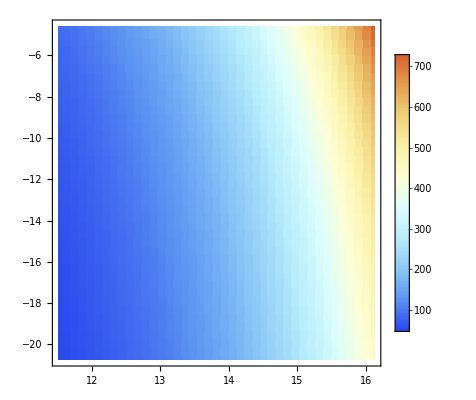

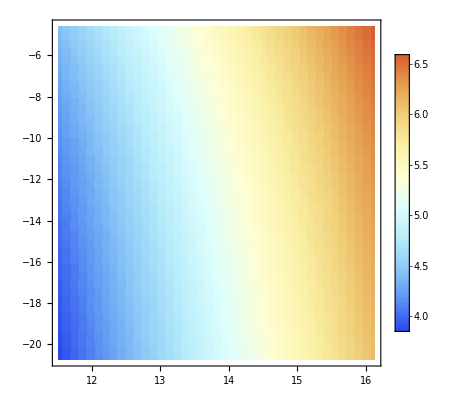

```mathematica
ListDensityPlot[MDensityUBTable,InterpolationOrder->0,PlotLegends->Automatic,ColorFunction->"LightTemperatureMap"]
ListDensityPlot[
Table[{MDensityUBTable[[i,1]],MDensityUBTable[[i,2]],Log[MDensityUBTable[[i,3]]]},{i,1,Length[MDensityUBTable]}],
InterpolationOrder->0,PlotLegends->Automatic,ColorFunction->"LightTemperatureMap"]
```

### Produce LB and UB Isoclines - remember log-log scale

```mathematica
mgCritLBApproxTable=Table[Table[N[{Log[NT],Log[mgCritLBApprox[M]]}],{M,MRange}],{iNT,NTMin,NTMAX+NTMin,dNT}];
mgCritUBApproxTable=Table[Table[N[{Log[NT],Log[mgCritUBApprox[M]]}],{M,MRange}],{iNT,NTMin,NTMAX+NTMin,dNT}];

(* So as to speed things up, I am creating tables - if the critical mutation rate falls below half the minimum I am plotting, I use results for lower N values. This does not alter the results, just saves times by not calculating things that I dont want to plot *)
i=1;
For[iNT=NTMin,iNT≤ NTMAX+NTMin,iNT=iNT+dNT,

For[j=1,j≤Length[mgCritLBApproxTable[[i]]],j++,

If[i>1,
If[mgCritLBApproxTable[[i-1]][[j]][[2]]>Log[mgMin/2],mgCritLBApproxTable[[i]][[j]]=mgCritLBApproxTable[[i]][[j]]/.NT->iNT,mgCritLBApproxTable[[i]][[j]]={mgCritLBApproxTable[[i]][[j]][[1]],mgCritLBApproxTable[[i-1]][[j]][[2]]}/.NT->iNT];
If[mgCritUBApproxTable[[i-1]][[j]][[2]]>Log[mgMin/2],mgCritUBApproxTable[[i]][[j]]=mgCritUBApproxTable[[i]][[j]]/.NT->iNT,mgCritUBApproxTable[[i]][[j]]={mgCritUBApproxTable[[i]][[j]][[1]],mgCritUBApproxTable[[i-1]][[j]][[2]]}/.NT->iNT];
,
mgCritLBApproxTable[[i]][[j]]=mgCritLBApproxTable[[i]][[j]]/.NT->iNT;
mgCritUBApproxTable[[i]][[j]]=mgCritUBApproxTable[[i]][[j]]/.NT->iNT;
];
];
i=i+1;
];
```

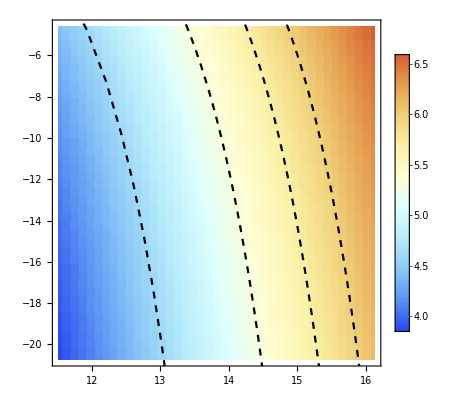

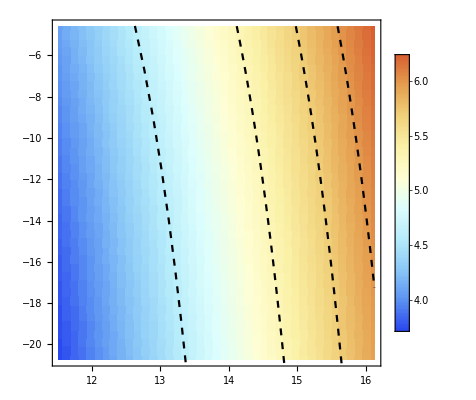

```mathematica
Show[
ListDensityPlot[
Table[{MDensityUBTable[[i,1]],MDensityUBTable[[i,2]],Log[MDensityUBTable[[i,3]]]},{i,1,Length[MDensityUBTable]}],
InterpolationOrder->0,PlotLegends->Automatic,ColorFunction->"LightTemperatureMap"],
ListLinePlot[Transpose[mgCritUBApproxTable],PlotRange->All,Joined->True,PlotStyle->Directive[{Thick,Black,Dashed}],
PlotRange->{{Min[MDensityUBTable[[All,1]]],Max[MDensityUBTable[[All,1]]]},{Min[MDensityUBTable[[All,2]]]+1,Max[MDensityUBTable[[All,2]]]-1}}]
]

Show[
ListDensityPlot[
Table[{MDensityLBTable[[i,1]],MDensityLBTable[[i,2]],Log[MDensityLBTable[[i,3]]]},{i,1,Length[MDensityLBTable]}],
InterpolationOrder->0,PlotLegends->Automatic,ColorFunction->"LightTemperatureMap"],
ListLinePlot[Transpose[mgCritLBApproxTable],PlotRange->All,Joined->True,PlotStyle->Directive[{Thick,Black,Dashed}],
PlotRange->{{Min[MDensityLBTable[[All,1]]],Max[MDensityLBTable[[All,1]]]},{Min[MDensityLBTable[[All,2]]]+1,Max[MDensityLBTable[[All,2]]]-1}}]
]
```

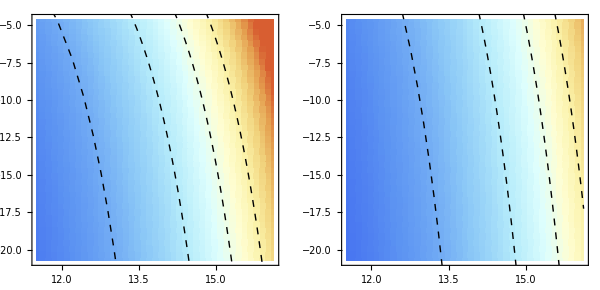

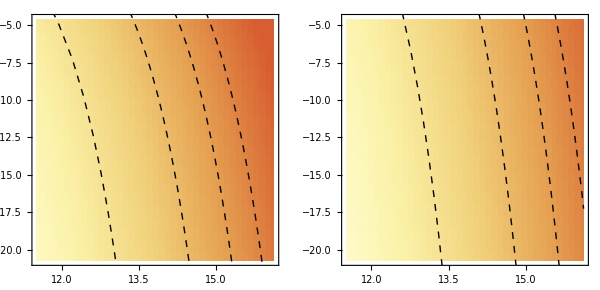

```mathematica
barMinMax={1,600};
logBarMinMax={Log[1],Log[600]};

GraphicsRow[
{
Show[
ListDensityPlot[
MDensityUBTable,
InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,barMinMax]]&)],
ListLinePlot[Transpose[mgCritUBApproxTable],PlotRange->All,Joined->True,PlotStyle->Directive[{Thick,Black,Dashed}],
PlotRange->{{Min[MDensityUBTable[[All,1]]],Max[MDensityUBTable[[All,1]]]},{Min[MDensityUBTable[[All,2]]]+1,Max[MDensityUBTable[[All,2]]]-1}}]
]
,
Show[
ListDensityPlot[
MDensityLBTable,
InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,barMinMax]]&)],
ListLinePlot[Transpose[mgCritLBApproxTable],PlotRange->All,Joined->True,PlotStyle->Directive[{Thick,Black,Dashed}],
PlotRange->{{Min[MDensityLBTable[[All,1]]],Max[MDensityLBTable[[All,1]]]},{Min[MDensityLBTable[[All,2]]]+1,Max[MDensityLBTable[[All,2]]]-1}}]
]
},ImageSize->600
]
BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,barMinMax]]&),barMinMax},LegendMarkerSize->350,LabelStyle->18,LegendLayout->"Row"]

GraphicsRow[
{
Show[
ListDensityPlot[
Table[{MDensityUBTable[[i,1]],MDensityUBTable[[i,2]],Log[MDensityUBTable[[i,3]]]},{i,1,Length[MDensityUBTable]}],
InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&)],
ListLinePlot[Transpose[mgCritUBApproxTable],PlotRange->All,Joined->True,PlotStyle->Directive[{Thick,Black,Dashed}],
PlotRange->{{Min[MDensityUBTable[[All,1]]],Max[MDensityUBTable[[All,1]]]},{Min[MDensityUBTable[[All,2]]]+1,Max[MDensityUBTable[[All,2]]]-1}}]
]
,
Show[
ListDensityPlot[
Table[{MDensityLBTable[[i,1]],MDensityLBTable[[i,2]],Log[MDensityLBTable[[i,3]]]},{i,1,Length[MDensityLBTable]}],
InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&)],
ListLinePlot[Transpose[mgCritLBApproxTable],PlotRange->All,Joined->True,PlotStyle->Directive[{Thick,Black,Dashed}],
PlotRange->{{Min[MDensityLBTable[[All,1]]],Max[MDensityLBTable[[All,1]]]},{Min[MDensityLBTable[[All,2]]]+1,Max[MDensityLBTable[[All,2]]]-1}}]
]
},ImageSize->600
]

BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),logBarMinMax},LegendMarkerSize->350,LabelStyle->18,LegendLayout->"Row",
"Ticks"->{Log[1],Log[6],Log[60],Log[600]},"TickLabels"->{"6","60","600","1"},ImageSize->400]
```

### Style for output in figure 4

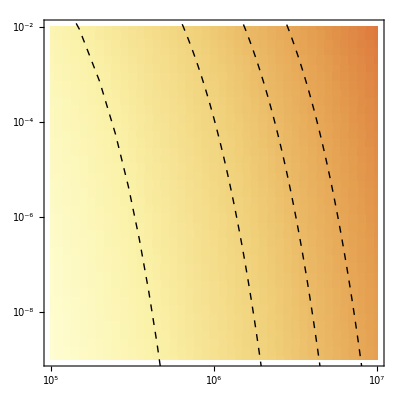

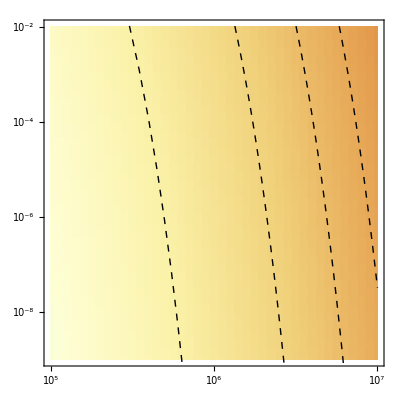

```mathematica
logBarMinMax={0,Log[600]};
logBarMinMax={0,Log[1000]};

frameTicksStylingUB={{Join[
Table[{Log[10^-i],If[Mod[i,2]==0,Superscript[10,-i],""],{0.02,0}},{i,2,9,1}],
Flatten[Table[Table[{Log[i*10^j],"",{0.0075,0}},{i,2,9,2}],{j,-9,-3}],1]
],None},{Join[Table[{Log[10^i],Superscript[10,i],{0.02,0}},{i,5,7}],Flatten[Table[Table[{Log[i*10^j],"",{0.0075,0}},{i,2,9}],{j,5,6}],1]],None}};

frameTicksStylingLB={{Join[
Table[{Log[10^-i],If[Mod[i,2]==0,Superscript[10,-i],""],{0.02,0}},{i,2,9,1}],
Flatten[Table[Table[{Log[i*10^j],"",{0.0075,0}},{i,2,9,2}],{j,-9,-3}],1]
],None},{Join[Table[{Log[10^i],Superscript[10,i],{0.02,0}},{i,5,7}],Flatten[Table[Table[{Log[i*10^j],"",{0.0075,0}},{i,2,9}],{j,5,6}],1]],None}};

plotFacultativeUB=Show[
ListDensityPlot[
Table[{MDensityUBTable[[i,1]],MDensityUBTable[[i,2]],Log[MDensityUBTable[[i,3]]]},{i,1,Length[MDensityUBTable]}],
InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&)],
ListLinePlot[Transpose[mgCritUBApproxTable],PlotRange->All,Joined->True,PlotStyle->Directive[{Thick,Black,Dashed}],
PlotRange->{{Min[MDensityUBTable[[All,1]]],Max[MDensityUBTable[[All,1]]]},{Min[MDensityUBTable[[All,2]]]+1,Max[MDensityUBTable[[All,2]]]-1}}],
FrameTicks->frameTicksStylingUB,
FrameTicksStyle->{{18,18},{18,18}},ImageSize->400
]

plotFacultativeLB=Show[
ListDensityPlot[
Table[{MDensityLBTable[[i,1]],MDensityLBTable[[i,2]],Log[MDensityLBTable[[i,3]]]},{i,1,Length[MDensityLBTable]}],
InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),
FrameTicks->frameTicksStylingLB,
FrameTicksStyle->{{18,18},{18,18}},ImageSize->400
],
ListLinePlot[Transpose[mgCritLBApproxTable],PlotRange->All,Joined->True,PlotStyle->Directive[{Thick,Black,Dashed}],
PlotRange->{{Min[MDensityLBTable[[All,1]]],Max[MDensityLBTable[[All,1]]]},{Min[MDensityLBTable[[All,2]]]+1,Max[MDensityLBTable[[All,2]]]-1}}]
]

plotFacultativeLegend=BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),logBarMinMax},LegendMarkerSize->350,LabelStyle->12,LegendLayout->"Column",
"Ticks"->Sort[Join[Table[Log[10^i],{i,0,3}],Flatten[Table[Table[Log[j*10^i],{j,2,8,2}],{i,0,2}],1]]],"TickLabels"->Join[{"1"},ConstantArray["",4],{"10"},ConstantArray["",4],{"100","","","600","",""}],ImageSize->800]
```

## rare sex (c=0.999)

```mathematica
(* Set up equations for critical mutation rate at which expected number of mating types (M) increases by one as a function of M (original number of mating types) *)
cEval={c->0.999};
mgCritLBApprox[M_]=If[M==2,(2^(-7/2+(2 c NT)/(-1+c)) (1+(2-3 c) c) (-(c NT)/(-1+c))^(1/2+(2 c NT)/(-1+c)) (-((1+c) NT)/(-1+c))^(1/2+((1+c) NT)/(-1+c)) ((NT+3 c NT)/(2-2 c))^((NT+3 c NT)/(1-c)))/c,1/2 (1+c) ⅇ^(-((1+c) NT)/(-1+c)) (M/(-1+M))^(1-M) NT (-((1+c) NT)/(-1+c))^(-1/2+((1+c) NT)/(-1+c)) (ⅇ^(((-2+M+c M) NT)/((-1+c) (-1+M))) (-((-2+M+c M) NT)/((-1+c) (-1+M)))^(1/2-((-2+M+c M) NT)/((-1+c) (-1+M))))^(1-M) (ⅇ^(((-1+c+M+c M) NT)/((-1+c) M)) (-((-1+c+M+c M) NT)/((-1+c) M))^(1/2-((-1+c+M+c M) NT)/((-1+c) M)))^M]/.cEval;

mgCritUBApprox[M_]=(NT/(M-1)-1)^-1*If[M==2,(2^(-7/2+(2 c NT)/(-1+c)) (1+(2-3 c) c) (-(c NT)/(-1+c))^(1/2+(2 c NT)/(-1+c)) (-((1+c) NT)/(-1+c))^(1/2+((1+c) NT)/(-1+c)) ((NT+3 c NT)/(2-2 c))^((NT+3 c NT)/(1-c)))/c,1/2 (1+c) ⅇ^(-((1+c) NT)/(-1+c)) (M/(-1+M))^(1-M) NT (-((1+c) NT)/(-1+c))^(-1/2+((1+c) NT)/(-1+c)) (ⅇ^(((-2+M+c M) NT)/((-1+c) (-1+M))) (-((-2+M+c M) NT)/((-1+c) (-1+M)))^(1/2-((-2+M+c M) NT)/((-1+c) (-1+M))))^(1-M) (ⅇ^(((-1+c+M+c M) NT)/((-1+c) M)) (-((-1+c+M+c M) NT)/((-1+c) M))^(1/2-((-1+c+M+c M) NT)/((-1+c) M)))^M]/.cEval;

NTMAX=10^7;
dNT=10^5;

mgMin=10^-9;
mgMax=10^-2;

NTMin=10^5;

MRange={2,3,4,6,8};
MIsoclines={2,3,4,6,8};



mgCritLBApproxIsoclinesTable=Table[Table[N[{iNT,mgCritLBApprox[M]}],{M,MIsoclines}],{iNT,NTMin,NTMAX+NTMin,dNT}];
mgCritUBApproxIsoclinesTable=Table[Table[N[{iNT,mgCritUBApprox[M]}],{M,MIsoclines}],{iNT,NTMin,NTMAX+NTMin,dNT}];
```

### Calculate density plot data: LogLogScale LB

```mathematica
NTMAX=10^7;
NTMin=10^5;

mgMin=10^-9;
mgMax=10^-2;

MDensityTable=Flatten[Table[Table[{N[logNT],N[logmg],0},{logNT,Log[NTMin],Log[NTMAX+NTMin],Abs[(Log[NTMAX+NTMin]-Log[NTMin])/100]}],{logmg,Log[mgMin],Log[mgMax],Abs[(Log[mgMin]-Log[mgMax])/100]}],1];

For[k=1,k≤Length[MDensityTable],k++,

(* Initialize logNT and logmg parameters for each run *)
logNT=MDensityTable[[k,1]];
logmg=MDensityTable[[k,2]];

(* If this is the beginning of an NT cycle, set MminNTPrev to 0*)
If[logNT==Log[NTMin],MminNTPrev=2];

(* Generate a long list starting with the minimum value we know M must have *)
mLBCritList=Table[{M,0},{M,MminNTPrev,1000}];

(* populate the first mgCrit value (probably quite low initiall for low NT) *)
mLBCritList[[1,2]]=N[mgCritLBApprox[  mLBCritList[[1,1]]  ]/.{NT->Exp[logNT]}];

(* run over values of M and populate mgCrit values, but stop doing this if mcrit is higher than what we're plotting *)
i=2;
While[mLBCritList[[i-1,2]]<mgMax&&i≤Length[mLBCritList],
mLBCritList[[i,2]]=N[mgCritLBApprox[  mLBCritList[[i,1]]  ]/.{NT->Exp[logNT]}];
i++;
];

(* shorten mLBCritList so that it only contains the values of mgCrit_ that we're plotting over *)
mLBCritList=Delete[mLBCritList,Position[mLBCritList[[All,2]],0] ];
If[Length[mLBCritList]>1,
(* Loop over mg to find where mg intersects the mgCrit list. This tells us the bound of M ... *)
j=1;
While[mLBCritList[[j,2]]<Exp[logmg],j++];
If[j>1,
MDensityTable[[k,3]]=mLBCritList[[j-1,1]];
MminNTPrev=mLBCritList[[j-1,1]];
,
MDensityTable[[k,3]]=1;
MminNTPrev=2;
]
,
MDensityTable[[k,3]]=1;
MminNTPrev=2;
]


]

MDensityLBTable=MDensityTable;
```

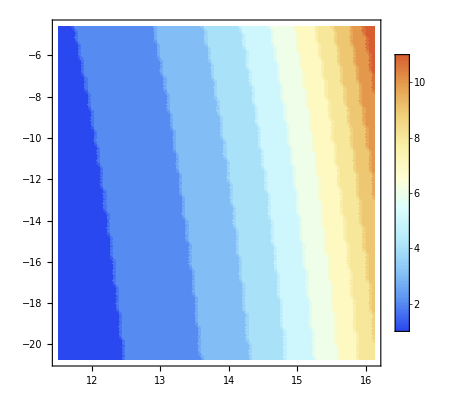

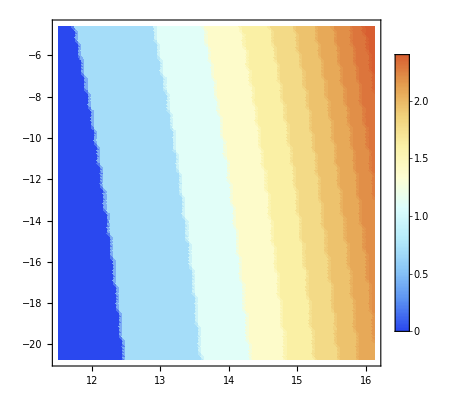

```mathematica
ListDensityPlot[MDensityLBTable,InterpolationOrder->1,PlotLegends->Automatic,ColorFunction->"LightTemperatureMap"]
ListDensityPlot[
Table[{MDensityLBTable[[i,1]],MDensityLBTable[[i,2]],Log[MDensityLBTable[[i,3]]]},{i,1,Length[MDensityLBTable]}],
InterpolationOrder->1,PlotLegends->Automatic,ColorFunction->"LightTemperatureMap"]
```

### Calculate density plot data: LogLogScale UB

```mathematica
NTMAX=10^7;
NTMin=10^5;

mgMin=10^-9;
mgMax=10^-2;

MDensityTable=Flatten[Table[Table[{N[logNT],N[logmg],0},{logNT,Log[NTMin],Log[NTMAX+NTMin],Abs[(Log[NTMAX+NTMin]-Log[NTMin])/100]}],{logmg,Log[mgMin],Log[mgMax],Abs[(Log[mgMin]-Log[mgMax])/100]}],1];

For[k=1,k≤Length[MDensityTable],k++,

(* Initialize logNT and logmg parameters for each run *)
logNT=MDensityTable[[k,1]];
logmg=MDensityTable[[k,2]];

(* If this is the beginning of an NT cycle, set MminNTPrev to 0*)
If[logNT==Log[NTMin],MminNTPrev=2];

(* Generate a long list starting with the minimum value we know M must have *)
mUBCritList=Table[{M,0},{M,MminNTPrev,1000}];

(* populate the first mgCrit value (probably quite low initiall for low NT) *)
mUBCritList[[1,2]]=N[mgCritUBApprox[  mUBCritList[[1,1]]  ]/.{NT->Exp[logNT]}];

(* run over values of M and populate mgCrit values, but stop doing this if mcrit is higher than what we're plotting *)
i=2;
While[mUBCritList[[i-1,2]]<mgMax&&i≤Length[mUBCritList],
mUBCritList[[i,2]]=N[mgCritUBApprox[  mUBCritList[[i,1]]  ]/.{NT->Exp[logNT]}];
i++;
];

(* shorten mLBCritList so that it only contains the values of mgCrit_ that we're plotting over *)
mUBCritList=Delete[mUBCritList,Position[mUBCritList[[All,2]],0] ];
If[Length[mUBCritList]>1,
(* Loop over mg to find where mg intersects the mgCrit list. This tells us the bound of M ... *)
j=1;
While[mUBCritList[[j,2]]<Exp[logmg],j++];
If[j>1,
MDensityTable[[k,3]]=mUBCritList[[j-1,1]];
MminNTPrev=mUBCritList[[j-1,1]];
,
MDensityTable[[k,3]]=1;
MminNTPrev=2;
]
,
MDensityTable[[k,3]]=1;
MminNTPrev=2;
]


]

MDensityUBTable=MDensityTable;
```

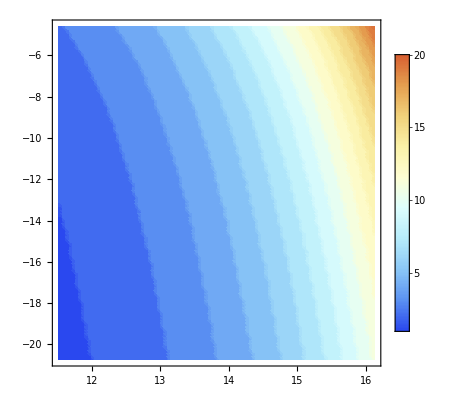

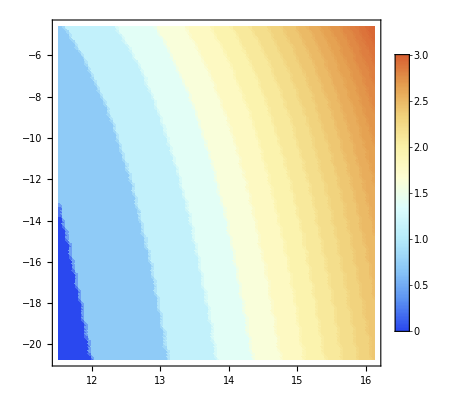

```mathematica
ListDensityPlot[MDensityUBTable,InterpolationOrder->1,PlotLegends->Automatic,ColorFunction->"LightTemperatureMap"]
ListDensityPlot[
Table[{MDensityUBTable[[i,1]],MDensityUBTable[[i,2]],Log[MDensityUBTable[[i,3]]]},{i,1,Length[MDensityUBTable]}],
InterpolationOrder->1,PlotLegends->Automatic,ColorFunction->"LightTemperatureMap"]
```

### Produce LB and UB Isoclines - remember log-log scale

```mathematica
mgCritLBApproxTable=Table[Table[N[{Log[iNT],Log[mgCritLBApprox[M]]}],{M,MRange}],{iNT,NTMin,NTMAX+NTMin,dNT}];
mgCritUBApproxTable=Table[Table[N[{Log[iNT],Log[mgCritUBApprox[M]]}],{M,MRange}],{iNT,NTMin,NTMAX+NTMin,dNT}];

(* So as to speed things up, I am creating tables - if the critical mutation rate falls below half the minimum I am plotting, I use results for lower N values. This does not alter the results, just saves times by not calculating things that I dont want to plot *)
i=1;
For[iNT=NTMin,iNT≤ NTMAX+NTMin,iNT=iNT+dNT,
For[j=1,j≤Length[mgCritLBApproxTable[[i]]],j++,

If[i>1,
If[mgCritLBApproxTable[[i-1]][[j]][[2]]>Log[mgMin/2],mgCritLBApproxTable[[i]][[j]]=Evaluate[mgCritLBApproxTable[[i]][[j]]/.NT->iNT],mgCritLBApproxTable[[i]][[j]]=Evaluate[{mgCritLBApproxTable[[i]][[j]][[1]],mgCritLBApproxTable[[i-1]][[j]][[2]]}/.NT->iNT]];
If[mgCritUBApproxTable[[i-1]][[j]][[2]]>Log[mgMin/2],mgCritUBApproxTable[[i]][[j]]=Evaluate[mgCritUBApproxTable[[i]][[j]]/.NT->iNT],mgCritUBApproxTable[[i]][[j]]=Evaluate[{mgCritUBApproxTable[[i]][[j]][[1]],mgCritUBApproxTable[[i-1]][[j]][[2]]}/.NT->iNT]];
,
mgCritLBApproxTable[[i]][[j]]=Evaluate[mgCritLBApproxTable[[i]][[j]]/.NT->iNT];
mgCritUBApproxTable[[i]][[j]]=Evaluate[mgCritUBApproxTable[[i]][[j]]/.NT->iNT];
];
];
i=i+1;
];
```

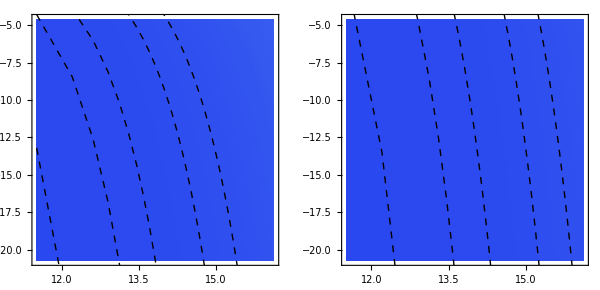

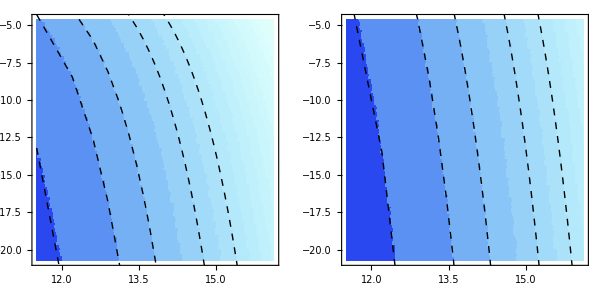

```mathematica
barMinMax={1,600};
logBarMinMax={Log[1],Log[600]};

GraphicsRow[
{
Show[
ListDensityPlot[
MDensityUBTable,
InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,barMinMax]]&)],
ListLinePlot[Transpose[mgCritUBApproxTable],PlotRange->All,Joined->True,PlotStyle->Directive[{Thick,Black,Dashed}],
PlotRange->{{Min[MDensityUBTable[[All,1]]],Max[MDensityUBTable[[All,1]]]},{Min[MDensityUBTable[[All,2]]]+1,Max[MDensityUBTable[[All,2]]]-1}}]
]
,
Show[
ListDensityPlot[
MDensityLBTable,
InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,barMinMax]]&)],
ListLinePlot[Transpose[mgCritLBApproxTable],PlotRange->All,Joined->True,PlotStyle->Directive[{Thick,Black,Dashed}],
PlotRange->{{Min[MDensityLBTable[[All,1]]],Max[MDensityLBTable[[All,1]]]},{Min[MDensityLBTable[[All,2]]]+1,Max[MDensityLBTable[[All,2]]]-1}}]
]
},ImageSize->600
]
BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,barMinMax]]&),barMinMax},LegendMarkerSize->350,LabelStyle->18,LegendLayout->"Row"]

GraphicsRow[
{
Show[
ListDensityPlot[
Table[{MDensityUBTable[[i,1]],MDensityUBTable[[i,2]],Log[MDensityUBTable[[i,3]]]},{i,1,Length[MDensityUBTable]}],
InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&)],
ListLinePlot[Transpose[mgCritUBApproxTable],PlotRange->All,Joined->True,PlotStyle->Directive[{Thick,Black,Dashed}],
PlotRange->{{Min[MDensityUBTable[[All,1]]],Max[MDensityUBTable[[All,1]]]},{Min[MDensityUBTable[[All,2]]]+1,Max[MDensityUBTable[[All,2]]]-1}}]
]
,
Show[
ListDensityPlot[
Table[{MDensityLBTable[[i,1]],MDensityLBTable[[i,2]],Log[MDensityLBTable[[i,3]]]},{i,1,Length[MDensityLBTable]}],
InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&)],
ListLinePlot[Transpose[mgCritLBApproxTable],PlotRange->All,Joined->True,PlotStyle->Directive[{Thick,Black,Dashed}],
PlotRange->{{Min[MDensityLBTable[[All,1]]],Max[MDensityLBTable[[All,1]]]},{Min[MDensityLBTable[[All,2]]]+1,Max[MDensityLBTable[[All,2]]]-1}}]
]
},ImageSize->600
]

BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),logBarMinMax},LegendMarkerSize->350,LabelStyle->18,LegendLayout->"Row",
"Ticks"->{Log[1],Log[6],Log[60],Log[600]},"TickLabels"->{"6","60","600","1"},ImageSize->400]
```

### Style for output in figure 4

```mathematica
logBarMinMax={0,Log[1000]};

frameTicksStylingUB={{Join[
Table[{Log[10^-i],If[Mod[i,2]==0,Superscript[10,-i],""],{0.02,0}},{i,2,9,1}],
Flatten[Table[Table[{Log[i*10^j],"",{0.0075,0}},{i,2,9,2}],{j,-9,-3}],1]
],None},{Join[Table[{Log[10^i],Superscript[10,i],{0.02,0}},{i,5,7}],Flatten[Table[Table[{Log[i*10^j],"",{0.0075,0}},{i,2,9}],{j,5,6}],1]],None}};

frameTicksStylingLB={{Join[
Table[{Log[10^-i],If[Mod[i,2]==0,Superscript[10,-i],""],{0.02,0}},{i,2,9,1}],
Flatten[Table[Table[{Log[i*10^j],"",{0.0075,0}},{i,2,9,2}],{j,-9,-3}],1]
],None},{Join[Table[{Log[10^i],Superscript[10,i],{0.02,0}},{i,5,7}],Flatten[Table[Table[{Log[i*10^j],"",{0.0075,0}},{i,2,9}],{j,5,6}],1]],None}};

plotFacultativeUB=Show[
ListDensityPlot[
Table[{MDensityUBTable[[i,1]],MDensityUBTable[[i,2]],Log[MDensityUBTable[[i,3]]]},{i,1,Length[MDensityUBTable]}],
InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),FrameTicks->frameTicksStylingUB,
FrameTicksStyle->{{18,18},{18,18}},ImageSize->400
],

ListLinePlot[Transpose[mgCritUBApproxTable],PlotRange->All,Joined->True,PlotStyle->Directive[{Thick,Black,Dashed}],
PlotRange->{{Min[MDensityUBTable[[All,1]]],Max[MDensityUBTable[[All,1]]]},{Min[MDensityUBTable[[All,2]]]+1,Max[MDensityUBTable[[All,2]]]-1}}]
]

plotFacultativeLB=Show[
ListDensityPlot[
Table[{MDensityLBTable[[i,1]],MDensityLBTable[[i,2]],Log[MDensityLBTable[[i,3]]]},{i,1,Length[MDensityLBTable]}],
InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),FrameTicks->frameTicksStylingLB,
FrameTicksStyle->{{18,18},{18,18}},ImageSize->400
],
ListLinePlot[Transpose[mgCritLBApproxTable],PlotRange->All,Joined->True,PlotStyle->Directive[{Thick,Black,Dashed}],
PlotRange->{{Min[MDensityLBTable[[All,1]]],Max[MDensityLBTable[[All,1]]]},{Min[MDensityLBTable[[All,2]]]+1,Max[MDensityLBTable[[All,2]]]-1}}]
]

plotFacultativeLegend=BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),logBarMinMax},LegendMarkerSize->350,LabelStyle->18,LegendLayout->"Column",
"Ticks"->Sort[Join[Table[Log[10^i],{i,0,3}],Flatten[Table[Table[Log[j*10^i],{j,2,8,2}],{i,0,2}],1]]],"TickLabels"->Join[{"1"},ConstantArray["",4],{"10"},ConstantArray["",4],{"100","","","600","",""}],TicksStyle->18,ImageSize->800]
```

-Graphics-

-Graphics-

## Fig S1 (deterministic mating type frequency dynamics)

```mathematica
(* PARAMETERS: 
M = Number of mating types present in the population
c = rate of asexual reproduction
s = variance in mating type allele fitnesses (σ in Main Text and SI)
NT = number of individuals in population (N or Subscript[N, e] is Main Text and SI) 
*)

params1={M->3,c->0,s->0,NT->100};

params2={M->3,c->0,s->0.04,NT->100};

params3={M->3,c->0.9,s->0.04,NT->100};

params4={M->6,c->0,s->0,NT->100};

params5={M->6,c->0,s->0.04,NT->100};

params6={M->6,c->0.9,s->0.04,NT->100};

numDatPoints=10000;
```

## Streamplot (1a)

```mathematica
(* Define deterministic dynamics - dVec = D in Main Text and SI. δVec = d in Main Text and SI *)

params=params1;

(* dVec and δVec are defined here - note that since s=0 for this parameter set, precise values of δVec do not need to be defined *)
δVec=Table[ToExpression["δ"<>ToString[i]]/.params,{i,1,3}];
dVec=Table[1+s*δVec[[i]],{i,1,Length[δVec]}]/.params;

xVec=Table[ToExpression["x"<>ToString[i]],{i,1,Length[δVec]}];
xVecT=Table[ToExpression["x"<>ToString[i]<>"[t]"],{i,1,Length[δVec]}];
xVecTran=Table[xVec[[i]]->xVecT[[i]],{i,1,Length[δVec]}];

(* AVec gives the deterministic dynamics (See Eq.(8) in Main Text) *)
AVec=Table[Sum[xVec[[i]]xVec[[j]]((1-c)/2(xVec[[j]]-xVec[[i]])+s(1-c)/2(δVec[[i]]xVec[[j]]-δVec[[j]]xVec[[i]])+s(1+c)/2(δVec[[j]]-δVec[[i]]))/.params,{j,1,Length[δVec]}],{i,1,Length[δVec]}];

(* FP gives deterministic fixed point solution to the dynamics (see Eq.(11) in Main Text) *)
FP=Table[xVec[[i]]->1/M+s*(1-c-M-c*M)/(M^2(1-c))(M*δVec[[i]]-Sum[δVec[[j]],{j,1,Length[δVec]}])/.M->Length[δVec],{i,1,Length[δVec]}];

plota=
Show[
StreamPlot[AVec[[1;;2]]/.xVec[[3]]->1-Total[xVec]+xVec[[3]]/.params,{x1,0,1},{x2,0,1},StreamStyle->Gray,FrameStyle->18,ImageSize->400
],
RegionPlot[x1+x2>1.01/.params,{x1,1/NT/.params,(NT+1)/NT/.params},{x2,1/NT/.params,(NT+1)/NT/.params},BoundaryStyle->None,PlotStyle->Lighter[LightGray]],
Graphics[{Red,Thickness[0.005],Circle[{1/M,1/M}/.params,0.0125]}],
Graphics[{Red,Disk[{x1,x2}/.FP/.params,0.0125]}]
]
```

-Graphics-

## Histogram plot (1b)

```mathematica
(* Define deterministic dynamics - dVec = D in Main Text and SI. δVec = d in Main Text and SI *)

params=params2;

(* dVec and δVec are defined below - since s≠0 for this parameter set, precise values of δVec are defined in δTable *)
δTable=Table[RandomVariate[NormalDistribution[0,s/.params],M/.params],{i,1,numDatPoints}];

δVec=Table[ToExpression["δ"<>ToString[i]]/.params,{i,1,M/.params}];
dVec=Table[1+s*δVec[[i]],{i,1,Length[δVec]}]/.params;
xVec=Table[ToExpression["x"<>ToString[i]],{i,1,Length[δVec]}];
xVecT=Table[ToExpression["x"<>ToString[i]<>"[t]"],{i,1,Length[δVec]}];
xVecTran=Table[xVec[[i]]->xVecT[[i]],{i,1,Length[δVec]}];

(* AVec gives the deterministic dynamics (See Eq.(8) in Main Text) *)
AVec=Table[Sum[xVec[[i]]xVec[[j]]((1-c)/2(xVec[[j]]-xVec[[i]])+s(1-c)/2(δVec[[i]]xVec[[j]]-δVec[[j]]xVec[[i]])+s(1+c)/2(δVec[[j]]-δVec[[i]]))/.params,{j,1,Length[δVec]}],{i,1,Length[δVec]}];

(* FP gives deterministic fixed point solution to the dynamics (see Eq.(11) in Main Text) *)
FP=Table[xVec[[i]]->1/M+s*(1-c-M-c*M)/(M^2(1-c))(M*δVec[[i]]-Sum[δVec[[j]],{j,1,Length[δVec]}])/.M->Length[δVec],{i,1,Length[δVec]}];

FPTable=Table[xVec/.FP/.Table[δVec[[i]]->δTable[[j]][[i]],{i,1,Length[δVec]}]/.params,{j,1,Length[δTable]}];
barMinMax={0,1};

plotb=Show[
DensityHistogram[FPTable[[All,1;;2]],{1,1},"PDF",PlotRange->{{0,1},{0,1}},ImageSize->400,ColorFunctionScaling->False,ColorFunction->((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),FrameStyle->18,ImageSize->400],
RegionPlot[x1+x2>1.01-1/M(M-3)/.params,{x1,0,1},{x2,0,1},BoundaryStyle->None,PlotStyle->Lighter[LightGray]]
]
```

-Graphics-

## Histogram plot (1c)

```mathematica
(* Define deterministic dynamics - dVec = D in Main Text and SI. δVec = d in Main Text and SI *)

params=params3;

(* dVec and δVec are defined below - since s≠0 for this parameter set, precise values of δVec are defined in δTable *)
δTable=Table[RandomVariate[NormalDistribution[0,s/.params],M/.params],{i,1,numDatPoints}];

δVec=Table[ToExpression["δ"<>ToString[i]]/.params,{i,1,3}];
dVec=Table[1+s*δVec[[i]],{i,1,Length[δVec]}]/.params;
xVec=Table[ToExpression["x"<>ToString[i]],{i,1,Length[δVec]}];
xVecT=Table[ToExpression["x"<>ToString[i]<>"[t]"],{i,1,Length[δVec]}];
xVecTran=Table[xVec[[i]]->xVecT[[i]],{i,1,Length[δVec]}];

(* AVec gives the deterministic dynamics (See Eq.(8) in Main Text) *)
AVec=Table[Sum[xVec[[i]]xVec[[j]]((1-c)/2(xVec[[j]]-xVec[[i]])+s(1-c)/2(δVec[[i]]xVec[[j]]-δVec[[j]]xVec[[i]])+s(1+c)/2(δVec[[j]]-δVec[[i]]))/.params,{j,1,Length[δVec]}],{i,1,Length[δVec]}];

(* FP gives deterministic fixed point solution to the dynamics (see Eq.(11) in Main Text) *)
FP=Table[xVec[[i]]->1/M+s*(1-c-M-c*M)/(M^2(1-c))(M*δVec[[i]]-Sum[δVec[[j]],{j,1,Length[δVec]}])/.M->Length[δVec],{i,1,Length[δVec]}];

FPTable=Table[xVec/.FP/.Table[δVec[[i]]->δTable[[j]][[i]],{i,1,Length[δVec]}]/.params,{j,1,Length[δTable]}];
barMinMax={0,1};

plotc=Show[
DensityHistogram[FPTable[[All,1;;2]],{30,30},"PDF",PlotRange->{{0,1},{0,1}},ImageSize->400,ColorFunctionScaling->False,ColorFunction->((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),FrameStyle->18,ImageSize->400],
RegionPlot[x1+x2>1.01-1/M(M-3)/.params,{x1,0,1},{x2,0,1},BoundaryStyle->None,PlotStyle->Lighter[LightGray]]
]
```

-Graphics-

## Streamplot (1d)

```mathematica
(* Define deterministic dynamics - dVec = D in Main Text and SI. δVec = d in Main Text and SI *)

params=params4;

(* dVec and δVec are defined here - note that since s=0 for this parameter set, precise values of δVec do not need to be defined *)
δVec=Table[ToExpression["δ"<>ToString[i]]/.params,{i,1,M/.params}];
dVec=Table[1+s*δVec[[i]],{i,1,Length[δVec]}]/.params;
xVec=Table[ToExpression["x"<>ToString[i]],{i,1,Length[δVec]}];
xVecT=Table[ToExpression["x"<>ToString[i]<>"[t]"],{i,1,Length[δVec]}];
xVecTran=Table[xVec[[i]]->xVecT[[i]],{i,1,Length[δVec]}];

(* AVec gives the deterministic dynamics (See Eq.(8) in Main Text) *)
AVec=Table[Sum[xVec[[i]]xVec[[j]]((1-c)/2(xVec[[j]]-xVec[[i]])+s(1-c)/2(δVec[[i]]xVec[[j]]-δVec[[j]]xVec[[i]])+s(1+c)/2(δVec[[j]]-δVec[[i]]))/.params,{j,1,Length[δVec]}],{i,1,Length[δVec]}];

(* FP gives deterministic fixed point solution to the dynamics (see Eq.(11) in Main Text) *)
FP=Table[xVec[[i]]->1/M+s*(1-c-M-c*M)/(M^2(1-c))(M*δVec[[i]]-Sum[δVec[[j]],{j,1,Length[δVec]}])/.M->Length[δVec],{i,1,Length[δVec]}];

plotd=
Show[
StreamPlot[(AVec[[1;;2]]/.xVec[[3]]->1-Total[xVec]+xVec[[3]])/.Table[xVec[[i]]->1/M/.params,{i,4,M/.params}]/.params,{x1,0,1},{x2,0,1},StreamStyle->Gray,FrameStyle->18,ImageSize->400
],
RegionPlot[x1+x2>1.01-1/M(M-3)/.params,{x1,0,1},{x2,0,1},BoundaryStyle->None,PlotStyle->Lighter[LightGray]],
Graphics[{Red,Thickness[0.005],Circle[{1/M,1/M}/.params,0.0125]}],
Graphics[{Red,Disk[{x1,x2}/.FP/.params,0.0125]}]
]
```

-Graphics-

## Histogram plot (1e)

```mathematica
(* Define deterministic dynamics - dVec = D in Main Text and SI. δVec = d in Main Text and SI *)

params=params5;

(* dVec and δVec are defined below - since s≠0 for this parameter set, precise values of δVec are defined in δTable *)
δTable=Table[RandomVariate[NormalDistribution[0,s/.params],M/.params],{i,1,numDatPoints}];

δVec=Table[ToExpression["δ"<>ToString[i]]/.params,{i,1,M/.params}];
dVec=Table[1+s*δVec[[i]],{i,1,Length[δVec]}]/.params;
xVec=Table[ToExpression["x"<>ToString[i]],{i,1,Length[δVec]}];
xVecT=Table[ToExpression["x"<>ToString[i]<>"[t]"],{i,1,Length[δVec]}];
xVecTran=Table[xVec[[i]]->xVecT[[i]],{i,1,Length[δVec]}];

(* AVec gives the deterministic dynamics (See Eq.(8) in Main Text) *)
AVec=Table[Sum[xVec[[i]]xVec[[j]]((1-c)/2(xVec[[j]]-xVec[[i]])+s(1-c)/2(δVec[[i]]xVec[[j]]-δVec[[j]]xVec[[i]])+s(1+c)/2(δVec[[j]]-δVec[[i]]))/.params,{j,1,Length[δVec]}],{i,1,Length[δVec]}];

(* FP gives deterministic fixed point solution to the dynamics (see Eq.(11) in Main Text) *)
FP=Table[xVec[[i]]->1/M+s*(1-c-M-c*M)/(M^2(1-c))(M*δVec[[i]]-Sum[δVec[[j]],{j,1,Length[δVec]}])/.M->Length[δVec],{i,1,Length[δVec]}];

FPTable=Table[xVec/.FP/.Table[δVec[[i]]->δTable[[j]][[i]],{i,1,Length[δVec]}]/.params,{j,1,Length[δTable]}];
barMinMax={0,1};

plote=Show[
DensityHistogram[FPTable[[All,1;;2]],{1,1},"PDF",PlotRange->{{0,1},{0,1}},ImageSize->400,ColorFunctionScaling->False,ColorFunction->((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),FrameStyle->18,ImageSize->400],
RegionPlot[x1+x2>1.01-1/M(M-3)/.params,{x1,0,1},{x2,0,1},BoundaryStyle->None,PlotStyle->Lighter[LightGray]]
]
```

-Graphics-

## Histogram plot (1f)

```mathematica
(* Define deterministic dynamics - dVec = D in Main Text and SI. δVec = d in Main Text and SI *)

params=params6;

(* dVec and δVec are defined below - since s≠0 for this parameter set, precise values of δVec are defined in δTable *)
δTable=Table[RandomVariate[NormalDistribution[0,s/.params],M/.params],{i,1,numDatPoints}];

δVec=Table[ToExpression["δ"<>ToString[i]]/.params,{i,1,M/.params}];
dVec=Table[1+s*δVec[[i]],{i,1,Length[δVec]}]/.params;
xVec=Table[ToExpression["x"<>ToString[i]],{i,1,Length[δVec]}];
xVecT=Table[ToExpression["x"<>ToString[i]<>"[t]"],{i,1,Length[δVec]}];
xVecTran=Table[xVec[[i]]->xVecT[[i]],{i,1,Length[δVec]}];

(* AVec gives the deterministic dynamics (See Eq.(8) in Main Text) *)
AVec=Table[Sum[xVec[[i]]xVec[[j]]((1-c)/2(xVec[[j]]-xVec[[i]])+s(1-c)/2(δVec[[i]]xVec[[j]]-δVec[[j]]xVec[[i]])+s(1+c)/2(δVec[[j]]-δVec[[i]]))/.params,{j,1,Length[δVec]}],{i,1,Length[δVec]}];

(* FP gives deterministic fixed point solution to the dynamics (see Eq.(11) in Main Text) *)
FP=Table[xVec[[i]]->1/M+s*(1-c-M-c*M)/(M^2(1-c))(M*δVec[[i]]-Sum[δVec[[j]],{j,1,Length[δVec]}])/.M->Length[δVec],{i,1,Length[δVec]}];

FPTable=Table[xVec/.FP/.Table[δVec[[i]]->δTable[[j]][[i]],{i,1,Length[δVec]}]/.params,{j,1,Length[δTable]}];
barMinMax={0,1};

plotf=Show[
DensityHistogram[FPTable[[All,1;;2]],{30,30},"PDF",PlotRange->{{0,1},{0,1}},ImageSize->400,ColorFunctionScaling->False,ColorFunction->((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),FrameStyle->18,ImageSize->400],
RegionPlot[x1+x2>1.01-1/M(M-3)/.params,{x1,0,1},{x2,0,1},BoundaryStyle->None,PlotStyle->Lighter[LightGray]]
]

BarLegend[{((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),barMinMax},LegendMarkerSize->350,LabelStyle->18,LegendLayout->"Row"];
```

-Graphics-

## Fig S2-S4 (density plots: simulation vs analytics) (note - pre-generated data provided in GitHub folder)

/home/mapc-gwac20-user/Dropbox/MatingTypesFinal/GitHub_Resubmision_Files/mating_types_sim_compiled

## S2: c=1 (note - pre-generated data provided in GitHub folder)

```mathematica
(* Define parameters *)
params={NT->16,m->0.01,c->0.9999,s->0,Mmax->1000};

(* ANALYTIC PART ----------------------------------------------------------------------------------------------------------------------------*)

nArrow[n_]:=Sort[DeleteCases[n,0],Greater];
PSTRED[n_]:=Binomial[Mmax,Length[nArrow[n]]]/Binomial[NT,Length[nArrow[n]]]((2 m NT)/(Mmax-Length[ nArrow[n] ])(((1+c)/(1-c)NT)!)/(1+c))^(Length[ nArrow[n] ]-1)Product[1/(nArrow[n][[α]])1/((((1+c)/(1-c))NT-nArrow[n][[α]])!),{α,1,Length[nArrow[n]]}];

(* First construct a mapping from any i1,i2 to the appropriate first two elements of the ordered probability... *)
mapTable=Round[Table[If[i1+i2≤NT/.params,N[Sort[{i1,i2},Greater][[1;;2]]],0],{i1,0,NT/.params},{i2,0,NT/.params}]];
(* And a similar one for the permuation factors *)
permFactorTable=Table[If[i1+i2≤NT/.params,1/Length[Permutations[{i1,i2}]],0],{i1,0,NT/.params},{i2,0,NT/.params}];

(*  Now I want all possible states ... *)
stateIntPart=IntegerPartitions[NT/.params];
stateIntPart[[1]]={stateIntPart[[1,1]],0};

(* Now make a table that maps i1 and i2 to the set of states satisfying that condition *)
stateMapTable=Table[If[i1+i2≤NT/.params,Flatten[Position[stateIntPart[[All,1;;2]],mapTable[[i1+1,i2+1]]]],0],{i1,0,NT/.params},{i2,0,NT/.params}];

PSTAnaTableOrdered=Flatten[Table[
If[i1+i2≤NT/.params,
{i1,i2,Sum[permFactorTable[[i1+1,i2+1]]*Length[Permutations[Join[n,Table[0,{k,1,NT-Length[n]/.params}]]]]*PSTRED[n]/.params,{n,stateIntPart[[ stateMapTable[[i1+1,i2+1]] ]]}]}
,{i1,i2,0}]
,{i1,0,NT/.params},{i2,0,NT/.params}],1];
PSTAnaTableNorm=Total[PSTAnaTableOrdered[[All,3]]];
For[i=1,i≤Length[PSTAnaTableOrdered],i++,PSTAnaTableOrdered[[i,3]]=N[PSTAnaTableOrdered[[i,3]]/PSTAnaTableNorm]];

(* SIMULATION PART ----------------------------------------------------------------------------------------------------------------------------*)

(* First, reset Mmax as this is inconsequential (see mating_types_sim.cpp) *)

params[[4]]=Mmax->(NT/.params);

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=1;
minTimeStep=10000;
maxTimeStep=400000;
M0=5;


paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[m/.params]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[s/.params];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];

(*
Now let's account for the third dimension - now we have our 3D symmetry!!!
*)

simTrajOrdered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajOrdered[[i]]=Join[simTraj[[i,1;;2]],Join[nArrow[simTraj[[i,3;;]]],Table[0,{k,1,3-Length[nArrow[simTraj[[i,3;;]]]]/.params}]]];
];
PSTSimTableOrdered=DeleteCases[Flatten[Table[If[i1+i2≤NT/.params,Join[{i1,i2},{N[1/Length[Permutations[{i1,i2}]] Count[simTrajOrdered[[All,3;;4]],Sort[{i1,i2},Greater][[1;;2]]]/Length[simTrajOrdered]]}],{i1,i2,0}],{i1,0,NT/.params},{i2,0,NT/.params}],1],0];
PSTSimTableOrderedNorm=Total[PSTSimTableOrdered[[All,3]]];
For[i=1,i≤Length[PSTSimTableOrdered],i++,PSTSimTableOrdered[[i,3]]=N[PSTSimTableOrdered[[i,3]]/PSTSimTableOrderedNorm]];
```

```mathematica
barMinMax={0,Max[Join[PSTSimTableOrdered[[All,3]],PSTAnaTableOrdered[[All,3]]]]};


plot2A=Show[
ListDensityPlot[PSTSimTableOrdered,PlotRange->{{-1/2,NT+1/2/.params},{-1/2,NT+1/2/.params},barMinMax},InterpolationOrder->0,ImageSize->400,
ColorFunctionScaling->False,ColorFunction->((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),
FrameStyle->18,ImageSize->400,
PlotLabel->Style[Text["Simulation"],24]
],
RegionPlot[x1+x2>1.02*NT/.params,{x1,0,NT+1/.params},{x2,0,NT+1/.params},BoundaryStyle->None,PlotStyle->LightGray]
]

plot2B=Show[
ListDensityPlot[PSTAnaTableOrdered,PlotRange->{{-1/2,NT+1/2/.params},{-1/2,NT+1/2/.params},barMinMax},InterpolationOrder->0,ImageSize->400,
ColorFunctionScaling->False,ColorFunction->((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),
FrameStyle->18,ImageSize->400,
PlotLabel->Style[Text["Analytics"],24]
],
RegionPlot[x1+x2>1.02*NT/.params,{x1,0,NT+1/.params},{x2,0,NT+1/.params},BoundaryStyle->None,PlotStyle->LightGray]
]

plot2Legend=BarLegend[{((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),barMinMax},LegendMarkerSize->300,LabelStyle->18,LegendLabel->Style[Text["P^st(n)"],16]]
```

-Graphics-

-Graphics-

## S3: c=0 (note - pre-generated data provided in GitHub folder)

```mathematica
(* Define parameters *)
params={NT->16,m->0.01,c->0.0001,s->0,Mmax->1000};


(* ANALYTIC PART ----------------------------------------------------------------------------------------------------------------------------*)



nArrow[n_]:=Sort[DeleteCases[n,0],Greater];
PSTRED[n_]:=Binomial[Mmax,Length[nArrow[n]]]/Binomial[NT,Length[nArrow[n]]]((2 m NT)/(Mmax-Length[ nArrow[n] ])(((1+c)/(1-c)NT)!)/(1+c))^(Length[ nArrow[n] ]-1)Product[1/(nArrow[n][[α]])1/((((1+c)/(1-c))NT-nArrow[n][[α]])!),{α,1,Length[nArrow[n]]}];

(* First construct a mapping from any i1,i2 to the appropriate first two elements of the ordered probability... *)
mapTable=Round[Table[If[i1+i2≤NT/.params,N[Sort[{i1,i2},Greater][[1;;2]]],0],{i1,0,NT/.params},{i2,0,NT/.params}]];
(* And a similar one for the permuation factors *)
permFactorTable=Table[If[i1+i2≤NT/.params,1/Length[Permutations[{i1,i2}]],0],{i1,0,NT/.params},{i2,0,NT/.params}];

(*  Now I want all possible states ... *)
stateIntPart=IntegerPartitions[NT/.params];
stateIntPart[[1]]={stateIntPart[[1,1]],0};

(* Now make a table that maps i1 and i2 to the set of states satisfying that condition *)
stateMapTable=Table[If[i1+i2≤NT/.params,Flatten[Position[stateIntPart[[All,1;;2]],mapTable[[i1+1,i2+1]]]],0],{i1,0,NT/.params},{i2,0,NT/.params}];

PSTAnaTableOrdered=Flatten[Table[
If[i1+i2≤NT/.params,
{i1,i2,Sum[permFactorTable[[i1+1,i2+1]]*Length[Permutations[Join[n,Table[0,{k,1,NT-Length[n]/.params}]]]]*PSTRED[n]/.params,{n,stateIntPart[[ stateMapTable[[i1+1,i2+1]] ]]}]}
,{i1,i2,0}]
,{i1,0,NT/.params},{i2,0,NT/.params}],1];
PSTAnaTableNorm=Total[PSTAnaTableOrdered[[All,3]]];
For[i=1,i≤Length[PSTAnaTableOrdered],i++,PSTAnaTableOrdered[[i,3]]=N[PSTAnaTableOrdered[[i,3]]/PSTAnaTableNorm]];

(* SIMULATION PART ----------------------------------------------------------------------------------------------------------------------------*)

(* First, reset Mmax as this is inconseuqential ... *)

params[[4]]=Mmax->(NT/.params);

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=1;
minTimeStep=10000;
maxTimeStep=400000;
M0=5;


paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[m/.params]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[s/.params];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];

(*
Now let's account for the third dimension - now we have our 3D symmetry!!!
*)

simTrajOrdered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajOrdered[[i]]=Join[simTraj[[i,1;;2]],Join[nArrow[simTraj[[i,3;;]]],Table[0,{k,1,3-Length[nArrow[simTraj[[i,3;;]]]]/.params}]]];
];
PSTSimTableOrdered=DeleteCases[Flatten[Table[If[i1+i2≤NT/.params,Join[{i1,i2},{N[1/Length[Permutations[{i1,i2}]] Count[simTrajOrdered[[All,3;;4]],Sort[{i1,i2},Greater][[1;;2]]]/Length[simTrajOrdered]]}],{i1,i2,0}],{i1,0,NT/.params},{i2,0,NT/.params}],1],0];
PSTSimTableOrderedNorm=Total[PSTSimTableOrdered[[All,3]]];
For[i=1,i≤Length[PSTSimTableOrdered],i++,PSTSimTableOrdered[[i,3]]=N[PSTSimTableOrdered[[i,3]]/PSTSimTableOrderedNorm]];
```

```mathematica
barMinMax={0,Max[Join[PSTSimTableOrdered[[All,3]],PSTAnaTableOrdered[[All,3]]]]};


plot3A=Show[
ListDensityPlot[PSTSimTableOrdered,PlotRange->{{-1/2,NT+1/2/.params},{-1/2,NT+1/2/.params},barMinMax},InterpolationOrder->0,ImageSize->400,
ColorFunctionScaling->False,ColorFunction->((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),
FrameStyle->18,ImageSize->400,
PlotLabel->Style[Text["Simulation"],24]
],
RegionPlot[x1+x2>1.02*NT/.params,{x1,0,NT+1/.params},{x2,0,NT+1/.params},BoundaryStyle->None,PlotStyle->LightGray]
]

plot3B=Show[
ListDensityPlot[PSTAnaTableOrdered,PlotRange->{{-1/2,NT+1/2/.params},{-1/2,NT+1/2/.params},barMinMax},InterpolationOrder->0,ImageSize->400,
ColorFunctionScaling->False,ColorFunction->((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),
FrameStyle->18,ImageSize->400,
PlotLabel->Style[Text["Analytics"],24]
],
RegionPlot[x1+x2>1.02*NT/.params,{x1,0,NT+1/.params},{x2,0,NT+1/.params},BoundaryStyle->None,PlotStyle->LightGray]
]

plot3Legend=BarLegend[{((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),barMinMax},LegendMarkerSize->300,LabelStyle->18,LegendLabel->Style[Text["P^st(n)"],16]]
```

-Graphics-

-Graphics-

## S4: c=0.4 (note - pre-generated data provided in GitHub folder)

```mathematica
(* Define parameters *)
params={NT->16,m->0.01,c->0.4,s->0,Mmax->1000};


(* ANALYTIC PART ----------------------------------------------------------------------------------------------------------------------------*)



nArrow[n_]:=Sort[DeleteCases[n,0],Greater];
PSTRED[n_]:=Binomial[Mmax,Length[nArrow[n]]]/Binomial[NT,Length[nArrow[n]]]((2 m NT)/(Mmax-Length[ nArrow[n] ])(((1+c)/(1-c)NT)!)/(1+c))^(Length[ nArrow[n] ]-1)Product[1/(nArrow[n][[α]])1/((((1+c)/(1-c))NT-nArrow[n][[α]])!),{α,1,Length[nArrow[n]]}];

(* First construct a mapping from any i1,i2 to the appropriate first two elements of the ordered probability... *)
mapTable=Round[Table[If[i1+i2≤NT/.params,N[Sort[{i1,i2},Greater][[1;;2]]],0],{i1,0,NT/.params},{i2,0,NT/.params}]];
(* And a similar one for the permuation factors *)
permFactorTable=Table[If[i1+i2≤NT/.params,1/Length[Permutations[{i1,i2}]],0],{i1,0,NT/.params},{i2,0,NT/.params}];

(*  Now I want all possible states ... *)
stateIntPart=IntegerPartitions[NT/.params];
stateIntPart[[1]]={stateIntPart[[1,1]],0};

(* Now make a table that maps i1 and i2 to the set of states satisfying that condition *)
stateMapTable=Table[If[i1+i2≤NT/.params,Flatten[Position[stateIntPart[[All,1;;2]],mapTable[[i1+1,i2+1]]]],0],{i1,0,NT/.params},{i2,0,NT/.params}];

PSTAnaTableOrdered=Flatten[Table[
If[i1+i2≤NT/.params,
{i1,i2,Sum[permFactorTable[[i1+1,i2+1]]*Length[Permutations[Join[n,Table[0,{k,1,NT-Length[n]/.params}]]]]*PSTRED[n]/.params,{n,stateIntPart[[ stateMapTable[[i1+1,i2+1]] ]]}]}
,{i1,i2,0}]
,{i1,0,NT/.params},{i2,0,NT/.params}],1];
PSTAnaTableNorm=Total[PSTAnaTableOrdered[[All,3]]];
For[i=1,i≤Length[PSTAnaTableOrdered],i++,PSTAnaTableOrdered[[i,3]]=N[PSTAnaTableOrdered[[i,3]]/PSTAnaTableNorm]];

(* SIMULATION PART ----------------------------------------------------------------------------------------------------------------------------*)

(* First, reset Mmax as this is inconseuqential ... *)

params[[4]]=Mmax->(NT/.params);

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=1;
minTimeStep=10000;
maxTimeStep=400000;
M0=5;


paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[m/.params]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[s/.params];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];

(*
Now let's account for the third dimension - now we have our 3D symmetry!!!
*)

simTrajOrdered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajOrdered[[i]]=Join[simTraj[[i,1;;2]],Join[nArrow[simTraj[[i,3;;]]],Table[0,{k,1,3-Length[nArrow[simTraj[[i,3;;]]]]/.params}]]];
];
PSTSimTableOrdered=DeleteCases[Flatten[Table[If[i1+i2≤NT/.params,Join[{i1,i2},{N[1/Length[Permutations[{i1,i2}]] Count[simTrajOrdered[[All,3;;4]],Sort[{i1,i2},Greater][[1;;2]]]/Length[simTrajOrdered]]}],{i1,i2,0}],{i1,0,NT/.params},{i2,0,NT/.params}],1],0];
PSTSimTableOrderedNorm=Total[PSTSimTableOrdered[[All,3]]];
For[i=1,i≤Length[PSTSimTableOrdered],i++,PSTSimTableOrdered[[i,3]]=N[PSTSimTableOrdered[[i,3]]/PSTSimTableOrderedNorm]];
```

```mathematica
barMinMax={0,Max[Join[PSTSimTableOrdered[[All,3]],PSTAnaTableOrdered[[All,3]]]]};


plot4A=Show[
ListDensityPlot[PSTSimTableOrdered,PlotRange->{{-1/2,NT+1/2/.params},{-1/2,NT+1/2/.params},barMinMax},InterpolationOrder->0,ImageSize->400,
ColorFunctionScaling->False,ColorFunction->((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),
FrameStyle->18,ImageSize->400,
PlotLabel->Style[Text["Simulation"],24]
],
RegionPlot[x1+x2>1.02*NT/.params,{x1,0,NT+1/.params},{x2,0,NT+1/.params},BoundaryStyle->None,PlotStyle->LightGray]
]

plot4B=Show[
ListDensityPlot[PSTAnaTableOrdered,PlotRange->{{-1/2,NT+1/2/.params},{-1/2,NT+1/2/.params},barMinMax},InterpolationOrder->0,ImageSize->400,
ColorFunctionScaling->False,ColorFunction->((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),
FrameStyle->18,ImageSize->400,
PlotLabel->Style[Text["Analytics"],24]
],
RegionPlot[x1+x2>1.02*NT/.params,{x1,0,NT+1/.params},{x2,0,NT+1/.params},BoundaryStyle->None,PlotStyle->LightGray]
]

plot4Legend=BarLegend[{((Blend[{White,Red}, #1] &)[Rescale[#,barMinMax]]&),barMinMax},LegendMarkerSize->300,LabelStyle->18,LegendLabel->Style[Text["P^st(n)"],16]]
```

-Graphics-

-Graphics-

## Fig S5 (illustrating the approximation)

```mathematica
(* As this is an illustrative plot, we seek to show qualatative features of the stationary distributuion.
For this reason, the distribution that we plot below is that obtained from the 2-allele (1D) neutral Moran model with mutation. 
*)

Plot[z^c1(1-z)^c2/.{c1->-4,c2->-4},{z,0,1}]
```

-Graphics-

```mathematica
(*data1=Join[{0.5},Table[0.01,{zd,0.1,0.9,0.1}],{0.5}]*)
data1=Join[{0.0005},Table[Limit[z^c1(1-z)^c2/.{c1->2*2,c2->2*5},z->zd],{zd,0.1,0.9,0.1}],{0.0005}];

plot4a=Labeled[
BarChart[data1/Total[data1],PlotRange->{0,0.45},BarSpacing->None,ChartLabels->Table[If[i==0+1,"0",If[i==Length[data1],"N",If[i==4(*Position[data1,Max[data1]][[1,1]]*),"N/M",""]]],{i,1,Length[data1]}],Frame->True,FrameStyle->22,ImageSize->400,ChartStyle->Directive[{Lighter[Orange],Opacity[0.7]}],
PlotLabel->Style[Text["Example distribution"],22]],
Style[Text["n_i"],22],Bottom,Spacings->0];

plot4b=Labeled[
Show[
BarChart[data1/Total[data1],PlotRange->{0,0.45},BarSpacing->None,ChartLabels->Table[If[i==0+1,"0",If[i==Length[data1],"N",If[i==4(*Position[data1,Max[data1]][[1,1]]*),"N/M",""]]],{i,1,Length[data1]}],Frame->True,FrameStyle->22,ImageSize->400,ChartStyle->Directive[{Lighter[Orange],Opacity[0.2]}],
PlotLabel->Style[Text["Distribution Approximation (LB) "],22]],
BarChart[Table[If[i==Position[data1,Max[data1[[2;;(Length[data1]-1)]] ]][[1,1]],data1[[i]]/Total[data1],0],{i,1,Length[data1]}],BarSpacing->None,ChartStyle->Directive[{Lighter[Blue],Opacity[0.7]}]
]
],
Style[Text["n_i"],22],Bottom,Spacings->0];

plot4c=Labeled[
Show[
BarChart[data1/Total[data1],PlotRange->{0,0.45},BarSpacing->None,ChartLabels->Table[If[i==0+1,"0",If[i==Length[data1],"N",If[i==4(*Position[data1,Max[data1]][[1,1]]*),"N/M",""]]],{i,1,Length[data1]}],Frame->True,FrameStyle->22,ImageSize->400,ChartStyle->Directive[{Lighter[Orange],Opacity[0.2]}],
PlotLabel->Style[Text["Distribution Approximation (UB) "],22]],
BarChart[Join[{0},Table[data1[[  Position[data1,Max[data1[[2;;(Length[data1]-1)]] ]][[1,1]]]]/Total[data1],{i,2,Length[data1]-1}],{0}],BarSpacing->None,ChartStyle->Directive[{Lighter[Blue],Opacity[0.7]}]]
],
Style[Text["n_i"],22],Bottom,Spacings->0];

Labeled[GraphicsRow[{plot4a,plot4b,plot4c},ImageSize->1400,Spacings->0],Style[Text["P^ST(n)"],22],Left,Spacings->-0.]
```

-Graphics-P^ST(n)

```mathematica
data1=Join[{1/20 15000},Table[Limit[z^c1(1-z)^c2/.{c1->-2,c2->-2},z->zd],{zd,0.1,0.9,0.1}],{1/20 15000}]

plot4d=Labeled[
BarChart[data1/Total[data1],PlotRange->{0,0.6},BarSpacing->None,ChartLabels->Table[If[i==0+1,"0",If[i==Length[data1],"N",If[i==4(*Position[data1,Max[data1]][[1,1]]*),"N/M",""]]],{i,1,Length[data1]}],Frame->True,FrameStyle->22,ImageSize->400,ChartStyle->Directive[{Lighter[Orange],Opacity[0.7]}],
PlotLabel->Style[Text["Example distribution"],22]],
Style[Text["n_i"],22],Bottom,Spacings->0];

plot4e=Labeled[
Show[
BarChart[data1/Total[data1],PlotRange->{0,0.6},BarSpacing->None,ChartLabels->Table[If[i==0+1,"0",If[i==Length[data1],"N",If[i==4(*Position[data1,Max[data1]][[1,1]]*),"N/M",""]]],{i,1,Length[data1]}],Frame->True,FrameStyle->22,ImageSize->400,ChartStyle->Directive[{Lighter[Orange],Opacity[0.2]}],
PlotLabel->Style[Text["Distribution Approximation (LB) "],22]],
BarChart[Table[If[i==4,data1[[4]]/Total[data1],0],{i,1,Length[data1]}],BarSpacing->None,ChartStyle->Directive[{Lighter[Blue],Opacity[0.7]}]
]
],
Style[Text["n_i"],22],Bottom,Spacings->0];

plot4f=Labeled[
Show[
BarChart[data1/Total[data1],PlotRange->{0,0.6},BarSpacing->None,ChartLabels->Table[If[i==0+1,"0",If[i==Length[data1],"N",If[i==4(*Position[data1,Max[data1]][[1,1]]*),"N/M",""]]],{i,1,Length[data1]}],Frame->True,FrameStyle->22,ImageSize->400,ChartStyle->Directive[{Lighter[Orange],Opacity[0.2]}],
PlotLabel->Style[Text["Distribution Approximation (UB) "],22]],
BarChart[Join[{0},Table[0.01,{i,2,Length[data1]-1}],{0}],BarSpacing->None,ChartStyle->Directive[{Lighter[Blue],Opacity[0.7]}]]
],
Style[Text["n_i"],22],Bottom,Spacings->0];

Labeled[GraphicsRow[{plot4d,plot4e,plot4f},ImageSize->1400,Spacings->0],Style[Text["P^ST(n)"],22],Left,Spacings->-0.]
```

{750,123.457,39.0625,22.6757,17.3611,16.,17.3611,22.6757,39.0625,123.457,750}

-Graphics-P^ST(n)

## Fig S6 (M vs N, c=1) (note - pre-generated data provided in GitHub folder)

## C=1 (note - pre-generated data provided in GitHub folder)

### s = 0.0 (generate data)

```mathematica
params={c->1,Mmax->1000,m->0.0000005,NTMin->1000,NTMax->10000,dNT->1000,mutSD->0.0};

(* Subscript[m, g] is ... *)
m*NTMax/.params

MMeanSimTable0=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];
MModeSimTable0=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=N[200];
minTimeStep=10000;
maxTimeStep=N[1000000+minTimeStep];

(* number of expected mutations during relaxation is between ... *)
minTimeStep*m*{NTMin,NTMax}/.params

(* total number of expected mutations is between ... *)
maxTimeStep*m*{NTMin,NTMax}/.params

For[i=1,i≤Length[MMeanSimTable],i++,

Print["NT = "<>ToString[MMeanSimTable[[i,1]]]];

M0=3;

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[AccountingForm[maxTimeStep]]<>" "<>ToString[Mmax/.params]<>" "<>ToString[ MMeanSimTable[[i,1]] ]<>" "<>ToString[ AccountingForm[m/.params] ]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];
simTrajM=Table[Length[DeleteCases[simTraj[[i,3;;]],0]],{i,1,Length[simTraj]}];

MMeanSimTable0[[i,2]]=N[Mean[simTrajM]];
MMeanSimTable0[[i,3]]=N[StandardDeviation[simTrajM]];
MModeSimTable0[[i,2]]=N[Commonest[simTrajM][[1]]];
MModeSimTable0[[i,3]]=N[StandardDeviation[simTrajM]];

];
```

0.005

{5.,50.}

{505.,5050.}

NT = 1000

NT = 2000

NT = 3000

NT = 4000

NT = 5000

NT = 6000

NT = 7000

NT = 8000

NT = 9000

NT = 10000

```mathematica
Show[
ErrorListPlot[MMeanSimTable0,PlotRange->{0,3},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Red],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable0,
Joined->True,PlotStyle->{Darker[Red],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}]

]
```

-Graphics-

### s = 0.02 (generate data)

```mathematica
params={c->1,Mmax->1000,m->0.0000005,NTMin->1000,NTMax->10000,dNT->1000,mutSD->0.02};

m*NTMax/.params

MMeanSimTable002=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];
MModeSimTable002=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=N[200];
minTimeStep=10000;
maxTimeStep=N[1000000+minTimeStep];

For[i=1,i≤Length[MMeanSimTable],i++,Round[MModeLBApprox/.params/.NT->MMeanSimTable[[10,1]]]

Print["NT = "<>ToString[MMeanSimTable[[i,1]]]];

M0=3;

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[AccountingForm[maxTimeStep]]<>" "<>ToString[Mmax/.params]<>" "<>ToString[ MMeanSimTable[[i,1]] ]<>" "<>ToString[ AccountingForm[m/.params] ]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];
simTrajM=Table[Length[DeleteCases[simTraj[[i,3;;]],0]],{i,1,Length[simTraj]}];

MMeanSimTable002[[i,2]]=N[Mean[simTrajM]];
MMeanSimTable002[[i,3]]=N[StandardDeviation[simTrajM]];
MModeSimTable002[[i,2]]=N[Commonest[simTrajM][[1]]];
MModeSimTable002[[i,3]]=N[StandardDeviation[simTrajM]];

];
```

0.005

NT = 1000

NT = 2000

NT = 3000

NT = 4000

NT = 5000

NT = 6000

NT = 7000

NT = 8000

NT = 9000

NT = 10000

```mathematica
Show[
ErrorListPlot[MMeanSimTable0,PlotRange->{0,3},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Red],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable0,
Joined->True,PlotStyle->{Darker[Red],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}],

ErrorListPlot[MMeanSimTable002,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Blue],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable002,
Joined->True,PlotStyle->{Darker[Blue],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}]

]
```

-Graphics-

### s = 0.05 (generate data)

```mathematica
params={c->1,Mmax->1000,m->0.0000005,NTMin->1000,NTMax->10000,dNT->1000,mutSD->0.05};

m*NTMax/.params

MMeanSimTable005=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];
MModeSimTable005=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=N[200];
minTimeStep=10000;
maxTimeStep=N[1000000+minTimeStep];

For[i=1,i≤Length[MMeanSimTable],i++,

Print["NT = "<>ToString[MMeanSimTable[[i,1]]]];

M0=3;

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[AccountingForm[maxTimeStep]]<>" "<>ToString[Mmax/.params]<>" "<>ToString[ MMeanSimTable[[i,1]] ]<>" "<>ToString[ AccountingForm[m/.params] ]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];
simTrajM=Table[Length[DeleteCases[simTraj[[i,3;;]],0]],{i,1,Length[simTraj]}];

MMeanSimTable005[[i,2]]=N[Mean[simTrajM]];
MMeanSimTable005[[i,3]]=N[StandardDeviation[simTrajM]];
MModeSimTable005[[i,2]]=N[Commonest[simTrajM][[1]]];
MModeSimTable005[[i,3]]=N[StandardDeviation[simTrajM]];

];
```

0.005

NT = 1000

NT = 2000

NT = 3000

NT = 4000

NT = 5000

NT = 6000

NT = 7000

NT = 8000

NT = 9000

NT = 10000

```mathematica
Show[
ErrorListPlot[MMeanSimTable0,PlotRange->{0,3},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Red],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable0,
Joined->True,PlotStyle->{Darker[Red],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}],

ErrorListPlot[MMeanSimTable005,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Blue],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable005,
Joined->True,PlotStyle->{Darker[Blue],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}]

]
```

-Graphics-

### Combine above data for plot

```mathematica
MModeUBFullTable=Table[{NT,1+0.1},{NT,NTMin/.params,NTMax/.params,dNT/.params}];
MModeLBFullTable=Table[{NT,1-0.1},{NT,NTMin/.params,NTMax/.params,dNT/.params}];
MModeUBApprox=Table[{NT,1+0.05},{NT,NTMin/.params,NTMax/.params,dNT/.params}];
MModeLBApprox=Table[{NT,1-0.05},{NT,NTMin/.params,NTMax/.params,dNT/.params}];
```

```mathematica
Show[

ListLinePlot[Evaluate[{MModeUBFullTable,MModeLBFullTable}/.params],PlotRange->{0,3},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["Mode[M]",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Filling->{1->{2}},PlotStyle->None,FillingStyle->Directive[{Lighter[Green],Opacity[0.4]}],PlotLegends->LineLegend[{Lighter[Green],Opacity[0.9]},{Style[Text["Analytic Bounds s=0"],24]}]],
ListLinePlot[Evaluate[{MModeUBApprox,MModeLBApprox}/.params],
Filling->{1->{2}},PlotStyle->None,FillingStyle->Directive[{Lighter[Blue],Opacity[0.3]}],PlotLegends->LineLegend[{Lighter[Blue]},{Style[Text["Analytic bounds s=0 
(continuous approx.)"],24]}]],


(*ErrorListPlot[MMeanSimTable0,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Blue],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable0,
PlotMarkers->{{●,10}},PlotStyle->{Darker[Blue],AbsoluteDashing[3]},PlotLegends->{Style[Text[" Simulation s=0"],24]}],

(*ErrorListPlot[MMeanSimTable002,
Joined->True,PlotStyle->{Darker[Orange],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable002,
PlotMarkers->{{▲,15}},PlotStyle->{Darker[Orange],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation s=0.02"],24]}],

(*ErrorListPlot[MMeanSimTable005,
Joined->True,PlotStyle->{Darker[Red],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable005,
PlotMarkers->{{■,15}},PlotStyle->{Darker[Red],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation s=0.05"],24]}]

]
```

-Graphics-

/home/mapc-gwac20-user/Dropbox/MatingTypesFinal/PaperAndNotes/PaperResubmission3/SI/FigureEdits/FigS6/figS6_unstyled.pdf

### Load data from pre-generated files

```mathematica
params={c->0,Mmax->1000,m->0.0000005,NTMin->1000,NTMax->10000,dNT->1000,mutSD->0.0};

(* Load data for number of mating types from the simulations *)

MMeanSimTable0=Import[NotebookDirectory[]<>"Fig_S6_mean_M_c_1_sig_0.txt","Table"];
MModeSimTable0=Import[NotebookDirectory[]<>"Fig_S6_mode_M_c_1_sig_0.txt","Table"];

MMeanSimTable002=Import[NotebookDirectory[]<>"Fig_S6_mean_M_c_1_sig_002.txt","Table"];
MModeSimTable002=Import[NotebookDirectory[]<>"Fig_S6_mode_M_c_1_sig_002.txt","Table"];

MMeanSimTable005=Import[NotebookDirectory[]<>"Fig_S6_mean_M_c_1_sig_005.txt","Table"];
MModeSimTable005=Import[NotebookDirectory[]<>"Fig_S6_mode_M_c_1_sig_005.txt","Table"];

(* Note that since analytic solution for Mode[M] is one for the upper bound and lower bound, we choose these simple forms below for clarity of plotting *)

MModeUBFullTable=Table[{NT,1+0.1},{NT,NTMin/.params,NTMax/.params,dNT/.params}];
MModeLBFullTable=Table[{NT,1-0.1},{NT,NTMin/.params,NTMax/.params,dNT/.params}];
MModeUBApprox=Table[{NT,1+0.05},{NT,NTMin/.params,NTMax/.params,dNT/.params}];
MModeLBApprox=Table[{NT,1-0.05},{NT,NTMin/.params,NTMax/.params,dNT/.params}];

Needs["ErrorBarPlots`"]
Show[

ListLinePlot[Evaluate[{MModeUBFullTable,MModeLBFullTable}/.params],PlotRange->{0,3},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["Mode[M]",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Filling->{1->{2}},PlotStyle->None,FillingStyle->Directive[{Lighter[Green],Opacity[0.4]}],PlotLegends->LineLegend[{Lighter[Green],Opacity[0.9]},{Style[Text["Analytic Bounds s=0"],24]}]],
ListLinePlot[Evaluate[{MModeUBApprox,MModeLBApprox}/.params],
Filling->{1->{2}},PlotStyle->None,FillingStyle->Directive[{Lighter[Blue],Opacity[0.3]}],PlotLegends->LineLegend[{Lighter[Blue]},{Style[Text["Analytic bounds s=0 
(continuous approx.)"],24]}]],


(*ErrorListPlot[MMeanSimTable0,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Blue],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable0,
PlotMarkers->{{●,10}},PlotStyle->{Darker[Blue],AbsoluteDashing[3]},PlotLegends->{Style[Text[" Simulation s=0"],24]}],

(*ErrorListPlot[MMeanSimTable002,
Joined->True,PlotStyle->{Darker[Orange],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable002,
PlotMarkers->{{▲,15}},PlotStyle->{Darker[Orange],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation s=0.02"],24]}],

(*ErrorListPlot[MMeanSimTable005,
Joined->True,PlotStyle->{Darker[Red],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable005,
PlotMarkers->{{■,15}},PlotStyle->{Darker[Red],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation s=0.05"],24]}]

]
```

-Graphics-

## Fig S7 (M vs N, c=0) (note - pre-generated data provided in GitHub folder)

## C=0 (note - pre-generated data provided in GitHub folder)

### s = 0.0 (generate data)

```mathematica
params={c->0,Mmax->1000,m->0.0000005,NTMin->1000,NTMax->10000,dNT->1000,mutSD->0.0};

(* Subscript[m, g] is ... *)
m*NTMax/.params

MMeanSimTable0=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];
MModeSimTable0=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=N[200];
minTimeStep=10000;
maxTimeStep=N[1000000+minTimeStep];

(* number of expected mutations during relaxation is between ... *)
minTimeStep*m*{NTMin,NTMax}/.params

(* total number of expected mutations is between ... *)
maxTimeStep*m*{NTMin,NTMax}/.params

For[i=1,i≤Length[MMeanSimTable],i++,

Print["NT = "<>ToString[MMeanSimTable[[i,1]]]];

M0=30;

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[AccountingForm[maxTimeStep]]<>" "<>ToString[Mmax/.params]<>" "<>ToString[ MMeanSimTable[[i,1]] ]<>" "<>ToString[ AccountingForm[m/.params] ]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];
simTrajM=Table[Length[DeleteCases[simTraj[[i,3;;]],0]],{i,1,Length[simTraj]}];

MMeanSimTable0[[i,2]]=N[Mean[simTrajM]];
MMeanSimTable0[[i,3]]=N[StandardDeviation[simTrajM]];
MModeSimTable0[[i,2]]=N[Commonest[simTrajM][[1]]];
MModeSimTable0[[i,3]]=N[StandardDeviation[simTrajM]];

];
```

0.005

{5.,50.}

{505.,5050.}

NT = 1000

NT = 2000

NT = 3000

NT = 4000

NT = 5000

NT = 6000

NT = 7000

NT = 8000

NT = 9000

NT = 10000

```mathematica
Show[
ErrorListPlot[MMeanSimTable,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Red],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable,
Joined->True,PlotStyle->{Darker[Red],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}],

ErrorListPlot[MMeanSimTable0,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Blue],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable0,
Joined->True,PlotStyle->{Darker[Blue],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}]

]
```

-Graphics-

### s = 0.02 (generate data)

```mathematica
params={c->0,Mmax->1000,m->0.0000005,NTMin->1000,NTMax->10000,dNT->1000,mutSD->0.02};

m*NTMax/.params

MMeanSimTable002=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];
MModeSimTable002=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=N[200];
minTimeStep=10000;
maxTimeStep=N[1000000+minTimeStep];

For[i=1,i≤Length[MMeanSimTable],i++,

Print["NT = "<>ToString[MMeanSimTable[[i,1]]]];

M0=30;

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[AccountingForm[maxTimeStep]]<>" "<>ToString[Mmax/.params]<>" "<>ToString[ MMeanSimTable[[i,1]] ]<>" "<>ToString[ AccountingForm[m/.params] ]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];
simTrajM=Table[Length[DeleteCases[simTraj[[i,3;;]],0]],{i,1,Length[simTraj]}];

MMeanSimTable002[[i,2]]=N[Mean[simTrajM]];
MMeanSimTable002[[i,3]]=N[StandardDeviation[simTrajM]];
MModeSimTable002[[i,2]]=N[Commonest[simTrajM][[1]]];
MModeSimTable002[[i,3]]=N[StandardDeviation[simTrajM]];

];
```

0.005

NT = 1000

NT = 2000

NT = 3000

NT = 4000

NT = 5000

NT = 6000

NT = 7000

NT = 8000

NT = 9000

NT = 10000

```mathematica
Show[
ErrorListPlot[MMeanSimTable,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Red],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable,
Joined->True,PlotStyle->{Darker[Red],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}],

ErrorListPlot[MMeanSimTable002,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Blue],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable002,
Joined->True,PlotStyle->{Darker[Blue],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}]

]
```

-Graphics-

### s = 0.05 (generate data)

```mathematica
params={c->0,Mmax->1000,m->0.0000005,NTMin->1000,NTMax->10000,dNT->1000,mutSD->0.05};

m*NTMax/.params

MMeanSimTable005=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];
MModeSimTable005=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=N[200];
minTimeStep=10000;
maxTimeStep=N[1000000+minTimeStep];

For[i=1,i≤Length[MMeanSimTable],i++,

Print["NT = "<>ToString[MMeanSimTable[[i,1]]]];

M0=30;

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[AccountingForm[maxTimeStep]]<>" "<>ToString[Mmax/.params]<>" "<>ToString[ MMeanSimTable[[i,1]] ]<>" "<>ToString[ AccountingForm[m/.params] ]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];
simTrajM=Table[Length[DeleteCases[simTraj[[i,3;;]],0]],{i,1,Length[simTraj]}];

MMeanSimTable005[[i,2]]=N[Mean[simTrajM]];
MMeanSimTable005[[i,3]]=N[StandardDeviation[simTrajM]];
MModeSimTable005[[i,2]]=N[Commonest[simTrajM][[1]]];
MModeSimTable005[[i,3]]=N[StandardDeviation[simTrajM]];

];
```

0.005

NT = 1000

NT = 2000

NT = 3000

NT = 4000

NT = 5000

NT = 6000

NT = 7000

NT = 8000

NT = 9000

NT = 10000

```mathematica
Show[
ErrorListPlot[MMeanSimTable,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Red],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable,
Joined->True,PlotStyle->{Darker[Red],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}],

ErrorListPlot[MMeanSimTable005,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Blue],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable005,
Joined->True,PlotStyle->{Darker[Blue],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}]

]
```

-Graphics-

### analytic neutral bounds (s = 0)

```mathematica
params={c->0,Mmax->1000,m->0.0000005,NTMin->1000,NTMax->10000,dNT->100};

params[[2]]=Mmax->100000000;

(* Set a maximum M to look for - note that the functions rLB and rUB only cross M once. Also note that larger values will slow down the following code *)
MMaxguess=40;

(* Define rLB and rUB from SI (see Eqs.(S48-S49))*)
Clear[rLB,rUB];
rLB[M_]:=2 m NT!((M/(M-1))^(M-1)((NT((M-2)/(M-1)))!)^(M-1))/((NT((M-1)/M))!)^M;
rUB[M_]:=(NT/(M-1)-1)*rLB[M];

(* Numerically determine the points at which rUB and rLB cross one as a function of M - this gives Mode[M] *)
MModeLBFullTable=Table[
{NT,
If[
Position[Normal[CrossingDetect[Table[If[N[rLB[M]/.params]≥1,1,-1],{M,2,Min[Mmax-1/.params,NT,MMaxguess]}],0]],1]=={},
If[(rLB[2]/.params)≤ 1,1,Min[Mmax/.params,NT/.params]],
Position[Normal[CrossingDetect[Table[If[N[rLB[M]/.params]≥1,1,-1],{M,2,Min[Mmax-1/.params,NT,MMaxguess]}],0]],1][[1,1]]+1
]},
{NT,NTMin/.params,NTMax/.params,dNT/.params}];

MModeUBFullTable=Table[
{NT,
If[
Position[Normal[CrossingDetect[Table[If[N[rUB[M]/.params]≥1,1,-1],{M,2,Min[Mmax-1/.params,NT,MMaxguess]}],0]],1]=={},
If[(rUB[2]/.params)≤ 1,1,Min[Mmax/.params,NT/.params]],
Position[Normal[CrossingDetect[Table[If[N[rUB[M]/.params]≥1,1,-1],{M,2,Min[Mmax-1/.params,NT,MMaxguess]}],0]],1][[1,1]]+1
]},
{NT,NTMin/.params,NTMax/.params,dNT/.params}];
```

### Combine above data for plot

```mathematica
Show[

ListLinePlot[Evaluate[{MModeUBFullTable,MModeLBFullTable}/.params],PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["Mode[M]",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Filling->{1->{2}},PlotStyle->None,FillingStyle->Directive[{Lighter[Green],Opacity[0.4]}],PlotLegends->LineLegend[{Lighter[Green],Opacity[0.9]},{Style[Text["Analytic Bounds s=0"],24]}]],
Plot[Evaluate[{MModeUBApprox,MModeLBApprox}/.params],{NT,100,NTMax/.params},
Filling->{1->{2}},PlotStyle->None,FillingStyle->Directive[{Lighter[Blue],Opacity[0.3]}],PlotLegends->LineLegend[{Lighter[Blue]},{Style[Text["Analytic bounds s=0 
(continuous approx.)"],24]}]],


(*ErrorListPlot[MMeanSimTable0,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Blue],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable0,
PlotMarkers->{{●,10}},PlotStyle->{Darker[Blue],AbsoluteDashing[3]},PlotLegends->{Style[Text[" Simulation s=0"],24]}],

(*ErrorListPlot[MMeanSimTable002,
Joined->True,PlotStyle->{Darker[Orange],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable002,
PlotMarkers->{{▲,15}},PlotStyle->{Darker[Orange],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation s=0.02"],24]}],

(*ErrorListPlot[MMeanSimTable005,
Joined->True,PlotStyle->{Darker[Red],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable005,
PlotMarkers->{{■,15}},PlotStyle->{Darker[Red],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation s=0.05"],24]}]

]
```

-Graphics-

### Load data from pre-generated files

```mathematica
params={c->0,Mmax->1000,m->0.0000005,NTMin->1000,NTMax->10000,dNT->1000,mutSD->0.0};

(* Load data for number of mating types from the simulations *)

MMeanSimTable0=Import[NotebookDirectory[]<>"Fig_S7_mean_M_c_0_sig_0.txt","Table"];
MModeSimTable0=Import[NotebookDirectory[]<>"Fig_S7_mode_M_c_0_sig_0.txt","Table"];

MMeanSimTable002=Import[NotebookDirectory[]<>"Fig_S7_mean_M_c_0_sig_002.txt","Table"];
MModeSimTable002=Import[NotebookDirectory[]<>"Fig_S7_mode_M_c_0_sig_002.txt","Table"];

MMeanSimTable005=Import[NotebookDirectory[]<>"Fig_S7_mean_M_c_0_sig_005.txt","Table"];
MModeSimTable005=Import[NotebookDirectory[]<>"Fig_S7_mode_M_c_0_sig_005.txt","Table"];

(* Load analytic data on where rub and rlb cross one (numeric solution) *)

MModeUBFullTable=Import[NotebookDirectory[]<>"Fig_S7_analytic_mode_M_UB.txt","Table"];
MModeLBFullTable=Import[NotebookDirectory[]<>"Fig_S7_analytic_mode_M_LB.txt","Table"];

(* Analytic approximations for upper and lower bound on number of mating types *)

MModeUBApprox=√(NT/ProductLog[1/(4*E^2 m^2 NT)]);
MModeLBApprox=√(NT/(-2(1+Log[2m])));

Needs["ErrorBarPlots`"]

Show[

ListLinePlot[Evaluate[{MModeUBFullTable,MModeLBFullTable}/.params],PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["Mode[M]",24]},AxesOrigin->{750,0},(*Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],*)
Filling->{1->{2}},PlotStyle->None,FillingStyle->Directive[{Lighter[Green],Opacity[0.4]}],PlotLegends->LineLegend[{Lighter[Green],Opacity[0.9]},{Style[Text["Analytic Bounds s=0"],24]}]],
Plot[Evaluate[{MModeUBApprox,MModeLBApprox}/.params],{NT,100,NTMax/.params},
Filling->{1->{2}},PlotStyle->None,FillingStyle->Directive[{Lighter[Blue],Opacity[0.3]}],PlotLegends->LineLegend[{Lighter[Blue]},{Style[Text["Analytic bounds s=0 
(continuous approx.)"],24]}]],


(*ErrorListPlot[MMeanSimTable0,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Blue],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable0,
PlotMarkers->{{●,10}},PlotStyle->{Darker[Blue],AbsoluteDashing[3]},PlotLegends->{Style[Text[" Simulation s=0"],24]}],

(*ErrorListPlot[MMeanSimTable002,
Joined->True,PlotStyle->{Darker[Orange],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable002,
PlotMarkers->{{▲,15}},PlotStyle->{Darker[Orange],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation s=0.02"],24]}],

(*ErrorListPlot[MMeanSimTable005,
Joined->True,PlotStyle->{Darker[Red],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable005,
PlotMarkers->{{■,15}},PlotStyle->{Darker[Red],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation s=0.05"],24]}]

]
```

-Graphics-

## Fig S8 (M vs N, c=0.8)

## 1>C>0

### s = 0.0 (generate data)

```mathematica
params={c->0.8,Mmax->1000,m->0.0000005,NTMin->1000,NTMax->10000,dNT->1000,mutSD->0.0};

m*NTMax/.params

MMeanSimTable0=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];
MModeSimTable0=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=1000;
minTimeStep=10000;
maxTimeStep=10010000;

For[i=1,i≤Length[MMeanSimTable],i++,

Print["NT = "<>ToString[MMeanSimTable[[i,1]]]];

M0=10;

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[ MMeanSimTable[[i,1]] ]<>" "<>ToString[ AccountingForm[m/.params] ]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];
simTrajM=Table[Length[DeleteCases[simTraj[[i,3;;]],0]],{i,1,Length[simTraj]}];

MMeanSimTable0[[i,2]]=N[Mean[simTrajM]];
MMeanSimTable0[[i,3]]=N[StandardDeviation[simTrajM]];
MModeSimTable0[[i,2]]=N[Commonest[simTrajM][[1]]];
MModeSimTable0[[i,3]]=N[StandardDeviation[simTrajM]];

];
```

0.005

NT = 1000

NT = 2000

NT = 3000

NT = 4000

NT = 5000

NT = 6000

NT = 7000

NT = 8000

NT = 9000

NT = 10000

```mathematica
Show[
ErrorListPlot[MMeanSimTable,PlotRange->{0,30/2},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25/2}],
Joined->True,PlotStyle->{Darker[Red],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable,
Joined->True,PlotStyle->{Darker[Red],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}],

ErrorListPlot[MMeanSimTable0,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Blue],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable0,
Joined->True,PlotStyle->{Darker[Blue],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}]

]
```

-Graphics-

### s = 0.02 (generate data)

```mathematica
params={c->0.8,Mmax->1000,m->0.0000005,NTMin->1000,NTMax->10000,dNT->1000,mutSD->0.02};

m*NTMax/.params

MMeanSimTable002=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];
MModeSimTable002=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=1000;
minTimeStep=10000;
maxTimeStep=10010000;

For[i=1,i≤Length[MMeanSimTable],i++,

Print["NT = "<>ToString[MMeanSimTable[[i,1]]]];

M0=10;

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[ MMeanSimTable[[i,1]] ]<>" "<>ToString[ AccountingForm[m/.params] ]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];
simTrajM=Table[Length[DeleteCases[simTraj[[i,3;;]],0]],{i,1,Length[simTraj]}];

MMeanSimTable002[[i,2]]=N[Mean[simTrajM]];
MMeanSimTable002[[i,3]]=N[StandardDeviation[simTrajM]];
MModeSimTable002[[i,2]]=N[Commonest[simTrajM][[1]]];
MModeSimTable002[[i,3]]=N[StandardDeviation[simTrajM]];

];
```

0.005

NT = 1000

NT = 2000

NT = 3000

NT = 4000

NT = 5000

NT = 6000

NT = 7000

NT = 8000

NT = 9000

NT = 10000

```mathematica
Show[
ErrorListPlot[MMeanSimTable,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Red],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable,
Joined->True,PlotStyle->{Darker[Red],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}],

ErrorListPlot[MMeanSimTable002,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Blue],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable002,
Joined->True,PlotStyle->{Darker[Blue],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}]

]
```

-Graphics-

### s = 0.05 (generate data)

```mathematica
params={c->0.8,Mmax->1000,m->0.0000005,NTMin->1000,NTMax->10000,dNT->1000,mutSD->0.05};

m*NTMax/.params

MMeanSimTable005=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];
MModeSimTable005=Table[{NT,0,0},{NT,NTMin/.params,NTMax/.params,dNT/.params}];

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=1000;
minTimeStep=10000;
maxTimeStep=10010000;

For[i=1,i≤Length[MMeanSimTable],i++,

Print["NT = "<>ToString[MMeanSimTable[[i,1]]]];

M0=10;

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[ MMeanSimTable[[i,1]] ]<>" "<>ToString[ AccountingForm[m/.params] ]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_compiled "<>paramString,Number,RecordLists->True];
simTrajM=Table[Length[DeleteCases[simTraj[[i,3;;]],0]],{i,1,Length[simTraj]}];

MMeanSimTable005[[i,2]]=N[Mean[simTrajM]];
MMeanSimTable005[[i,3]]=N[StandardDeviation[simTrajM]];
MModeSimTable005[[i,2]]=N[Commonest[simTrajM][[1]]];
MModeSimTable005[[i,3]]=N[StandardDeviation[simTrajM]];

];
```

0.005

NT = 1000

NT = 2000

NT = 3000

NT = 4000

NT = 5000

NT = 6000

NT = 7000

NT = 8000

NT = 9000

NT = 10000

```mathematica
Show[
ErrorListPlot[MMeanSimTable,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Red],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable,
Joined->True,PlotStyle->{Darker[Red],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}],

ErrorListPlot[MMeanSimTable005,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Blue],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],
ErrorListPlot[MModeSimTable005,
Joined->True,PlotStyle->{Darker[Blue],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation Mode[M]"],24]}]

]
```

-Graphics-

### analytic neutral bounds (s = 0)

```mathematica
params={c->0.8,Mmax->1000,m->0.0000005,NTMin->1000,NTMax->10000,dNT->100,mutSD->0.0};

params[[2]]=Mmax->100000000;

(* Set a maximum M to look for - note that the functions rLB and rUB only cross M once. Also note that larger values will slow down the following code *)
MMaxguess=40;

Clear[rLB,rUB]
rLB[M_]:=2m(((1+c)/(1-c)NT)!)/(1+c)(M/(M-1))^(M-1)((((1+c)/(1-c))NT-NT/(M-1))!)^(M-1)/((((1+c)/(1-c))NT-NT/M)!)^M;
rUB[M_]:=(NT/(M-1)-1)*rLB[M];

rLBApprox1=2m M^(-1+(3 M)/2-NT+((1+c) M NT)/(1-c))(M-1)^(3/2-(3 M)/2+((+2-M-c M) NT)/(1-c))(1+c)^(-1/2+((1+c) NT)/(1-c))(-2+M+c M)^(1/2 (-1+M-(2 (2-M-c M) NT)/(1-c)))  (-1+c+M+c M)^(-M/2+NT-((1+c) M NT)/(1-c));

rUBApprox1=(NT/(M-1)-1) rLBApprox1;

MModeLBFullTable=Table[
{NT,
If[
Position[Normal[CrossingDetect[Table[If[N[rLB[M]/.params]≥1,1,-1],{M,2,Min[Mmax-1/.params,NT,MMaxguess]}],0]],1]=={},
If[(rLB[2]/.params)≤ 1,1,Min[Mmax/.params,NT/.params]],
Position[Normal[CrossingDetect[Table[If[N[rLB[M]/.params]≥1,1,-1],{M,2,Min[Mmax-1/.params,NT,MMaxguess]}],0]],1][[1,1]]+1
]},
{NT,NTMin/.params,NTMax/.params,dNT/.params}];

MModeUBFullTable=Table[
{NT,
If[
Position[Normal[CrossingDetect[Table[If[N[rUB[M]/.params]≥1,1,-1],{M,2,Min[Mmax-1/.params,NT,MMaxguess]}],0]],1]=={},
If[(rUB[2]/.params)≤ 1,1,Min[Mmax/.params,NT/.params]],
Position[Normal[CrossingDetect[Table[If[N[rUB[M]/.params]≥1,1,-1],{M,2,Min[Mmax-1/.params,NT,MMaxguess]}],0]],1][[1,1]]+1
]},
{NT,NTMin/.params,NTMax/.params,dNT/.params}];


(* NOTE!!! Rootfind work as we here use logs and log[1] = 0 *)
MModeLBApproxTable=Table[
{NT,
x/.Quiet[FindRoot[Interpolation[Table[{M,Log[rLBApprox1/.params]},{M,2,Min[Mmax-1/.params,NT,MMaxguess],1}],x],{x,8}]]
},
{NT,NTMin/.params,NTMax/.params,dNT/.params}];

MModeUBApproxTable=Table[
{NT,
x/.Quiet[FindRoot[Interpolation[Table[{M,Log[rUBApprox1/.params]},{M,2,Min[Mmax-1/.params,NT,MMaxguess],1}],x],{x,8}]]
},
{NT,NTMin/.params,NTMax/.params,dNT/.params}];

Needs["ErrorBarPlots`"]
Show[
ListLinePlot[MModeUBFullTable,PlotStyle->{Darker[Green],DotDashed}],
ListLinePlot[MModeLBFullTable,PlotStyle->{Darker[Green],Dashed}],
ListLinePlot[MModeUBApproxTable,PlotStyle->{Darker[Blue],DotDashed}],
ListLinePlot[MModeLBApproxTable,PlotStyle->{Darker[Blue],Dashed}]
]
```

-Graphics-

### Combine above data for plot

```mathematica
Show[

ListLinePlot[Evaluate[{MModeUBFullTable,MModeLBFullTable}/.params],PlotRange->{0,30/2},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["Mode[M]",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0.8
m=5×10^-7"],24],{1200,25/2}],
Filling->{1->{2}},PlotStyle->None,FillingStyle->Directive[{Lighter[Green],Opacity[0.4]}],PlotLegends->LineLegend[{Lighter[Green],Opacity[0.9]},{Style[Text["Analytic Bounds σ=0"],24]}]],
ListLinePlot[Evaluate[{MModeUBApproxTable,MModeLBApproxTable}/.params],
Filling->{1->{2}},PlotStyle->None,FillingStyle->Directive[{Lighter[Blue],Opacity[0.3]}],PlotLegends->LineLegend[{Lighter[Blue]},{Style[Text["Analytic bounds σ=0 
(continuous approx.)"],24]}]],


(*ErrorListPlot[MMeanSimTable0,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Blue],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable0,
PlotMarkers->{{●,10}},PlotStyle->{Darker[Blue],AbsoluteDashing[3]},PlotLegends->{Style[Text[" Simulation σ=0"],24]}],

(*ErrorListPlot[MMeanSimTable002,
Joined->True,PlotStyle->{Darker[Orange],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable002,
PlotMarkers->{{▲,15}},PlotStyle->{Darker[Orange],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation σ=0.02"],24]}],

(*ErrorListPlot[MMeanSimTable005,
Joined->True,PlotStyle->{Darker[Red],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable005,
PlotMarkers->{{■,15}},PlotStyle->{Darker[Red],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation σ=0.05"],24]}]

]

(*Export["/home/mapc-gwac20-user/Dropbox/MatingTypesFinal/PaperAndNotes/Notes/Figures/plot_M_N_range_10000_10010000_sim_mean_c01_s005.pdf",%]*)
```

-Graphics-

### Load data from pre-generated files

```mathematica
params={c->0,Mmax->1000,m->0.0000005,NTMin->1000,NTMax->10000,dNT->1000,mutSD->0.0};

(* Load data for number of mating types from the simulations *)

MMeanSimTable0=Import[NotebookDirectory[]<>"Fig_S8_mean_M_c_01_sig_0.txt","Table"];
MModeSimTable0=Import[NotebookDirectory[]<>"Fig_S8_mode_M_c_01_sig_0.txt","Table"];

MMeanSimTable002=Import[NotebookDirectory[]<>"Fig_S8_mean_M_c_01_sig_002.txt","Table"];
MModeSimTable002=Import[NotebookDirectory[]<>"Fig_S8_mode_M_c_01_sig_002.txt","Table"];

MMeanSimTable005=Import[NotebookDirectory[]<>"Fig_S8_mean_M_c_01_sig_005.txt","Table"];
MModeSimTable005=Import[NotebookDirectory[]<>"Fig_S8_mode_M_c_01_sig_005.txt","Table"];

(* Load analytic data on where rub and rlb cross one (full numeric solution) *)

MModeUBFullTable=Import[NotebookDirectory[]<>"Fig_S8_analytic_mode_M_UB.txt","Table"];
MModeLBFullTable=Import[NotebookDirectory[]<>"Fig_S8_analytic_mode_M_LB.txt","Table"];

(* Load analytic data on where rub and rlb cross one (approximate numeric solution) *)

MModeUBApproxTable=Import[NotebookDirectory[]<>"Fig_S8_analytic_approx_mode_M_UB.txt","Table"];
MModeLBApproxTable=Import[NotebookDirectory[]<>"Fig_S8_analytic_approx_mode_M_LB.txt","Table"];


Needs["ErrorBarPlots`"]

Show[

ListLinePlot[Evaluate[{MModeUBFullTable,MModeLBFullTable}/.params],PlotRange->{0,30/2},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["Mode[M]",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0.8
m=5×10^-7"],24],{1200,25/2}],
Filling->{1->{2}},PlotStyle->None,FillingStyle->Directive[{Lighter[Green],Opacity[0.4]}],PlotLegends->LineLegend[{Lighter[Green],Opacity[0.9]},{Style[Text["Analytic Bounds σ=0"],24]}]],
ListLinePlot[Evaluate[{MModeUBApproxTable,MModeLBApproxTable}/.params],
Filling->{1->{2}},PlotStyle->None,FillingStyle->Directive[{Lighter[Blue],Opacity[0.3]}],PlotLegends->LineLegend[{Lighter[Blue]},{Style[Text["Analytic bounds σ=0 
(continuous approx.)"],24]}]],


(*ErrorListPlot[MMeanSimTable0,PlotRange->{0,30},Frame->True,ImageSize->600,FrameStyle->20,FrameLabel->{Style["N",24],Style["M",24]},AxesOrigin->{750,0},Epilog->Inset[Style[Text["c=0
m=5×10^-7"],24],{1200,25}],
Joined->True,PlotStyle->{Darker[Blue],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable0,
PlotMarkers->{{●,10}},PlotStyle->{Darker[Blue],AbsoluteDashing[3]},PlotLegends->{Style[Text[" Simulation σ=0"],24]}],

(*ErrorListPlot[MMeanSimTable002,
Joined->True,PlotStyle->{Darker[Orange],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable002,
PlotMarkers->{{▲,15}},PlotStyle->{Darker[Orange],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation σ=0.02"],24]}],

(*ErrorListPlot[MMeanSimTable005,
Joined->True,PlotStyle->{Darker[Red],Dotted},PlotLegends->{Style[Text["Simulation Mean[M]"],24]}],*)
ErrorListPlot[MModeSimTable005,
PlotMarkers->{{■,15}},PlotStyle->{Darker[Red],AbsoluteDashing[3]},PlotLegends->{Style[Text["Simulation σ=0.05"],24]}]

]
```

-Graphics-

## Fig S9 (N=10^4 trajectories)

### Define equations for rUB and rLB

```mathematica
rLB:=2m(((1+c)/(1-c)NT)!)/(1+c)(M/(M-1))^(M-1)((((1+c)/(1-c))NT-NT/(M-1))!)^(M-1)/((((1+c)/(1-c))NT-NT/M)!)^M;
rUB:=(NT/(M-1)-1)*rLB;

rLBApprox1=2m M^(-1+(3 M)/2-NT+((1+c) M NT)/(1-c))(M-1)^(3/2-(3 M)/2+((+2-M-c M) NT)/(1-c))(1+c)^(-1/2+((1+c) NT)/(1-c))(-2+M+c M)^(1/2 (-1+M-(2 (2-M-c M) NT)/(1-c)))  (-1+c+M+c M)^(-M/2+NT-((1+c) M NT)/(1-c));

rUBApprox1=(NT/(M-1)-1) rLBApprox1;
```

### Single run trial: c=0.9 mg=0.001 s=0 (without selection - left panels)

#### Calculate neutral expected number of mating types

```mathematica
(* Set up parameters and look at prediction from theory ... *)

params={NT->10000,m->0.0000001,c->0.9,Mmax->200,mutSD->0};
N[m*NT/.params]

ListPlot[
{
Table[{M,Log[rLB]/.params},{M,2,Mmax/.params,1}],
Table[{M,Log[rUB/.params]},{M,2,Mmax/.params,1}]
},PlotRange->Automatic,AxesOrigin->{0,0}]


MModeFullLB=Position[Normal[CrossingDetect[Table[If[N[Log[rLB]/.params]≥0,1,-1],{M,2,Mmax/.params}],0]],1][[1,1]]+1;
MModeFullUB=Position[Normal[CrossingDetect[Table[If[N[Log[rUB]/.params]≥0,1,-1],{M,2,Mmax/.params}],0]],1][[1,1]]+2;
{MModeFullLB,MModeFullUB}

MModeApproxLB=x/.Quiet[FindRoot[Interpolation[Table[{M,Log[rLBApprox1/.params]},{M,2,Mmax/.params,1}],x],{x,8}]];
MModeApproxUB=x/.Quiet[FindRoot[Interpolation[Table[{M,Log[rUBApprox1/.params]},{M,2,Mmax/.params,1}],x],{x,8}]];
{MModeApproxLB,MModeApproxUB}
```

0.001

-Graphics-

{4,7}

{4.68152,6.4057}

#### Run long simulation for inset

```mathematica
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=50;
minTimeStep=0;
maxTimeStep=50000;
M0=2;


(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_output_mutation_times_compiled "<>paramString,Number,RecordLists->True];

(* mutation times file generated with executed code above *)
mTimings=Flatten[Import[NotebookDirectory[]<>"DataFiles/MutationTimes/run_0.txt","Table"]];

(* Number of mutations observed ... *)
Length[mTimings]
```

0.001

50.

55

```mathematica
simTrajReordered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajReordered[[i,3;;Length[simTrajReordered[[i]] ] ]]=Reverse[Sort[simTraj[[i,3;;Length[simTraj[[i]] ] ] ]]];
];

sexRatioTraj=Table[{simTrajReordered[[i,1]],simTrajReordered[[i,2]]*simTrajReordered[[i,3]]/NT/.params},{i,1,Length[simTrajReordered]}];

simTrajInset=simTraj;
sexRatioTrajInset=sexRatioTraj;

MTrajInsetPlot=Show[
ListLinePlot[simTrajInset[[All,1;;2]],AxesOrigin->{0,0},PlotRange->{0,11},
GridLines->{mTimings,{2}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotStyle->Darker[Cyan],
Frame->True,ImageSize->600, (*FrameLabel->{{"M",""},{"Time (generations)",""}},*)FrameStyle->22,
AspectRatio->1/2,FrameTicks->{{{0,5,10},Automatic},{{0,25000,50000},Automatic}},ImageSize->200
],
Plot[{MModeFullLB,MModeFullUB},{t,0,maxTimeStep},Filling->1->{2},PlotStyle->None],
Plot[Commonest[simTraj[[All,2]]],{t,0,maxTimeStep},PlotStyle->Directive[{Darker[Blue],Dashed}]]
]

SexRatioTrajInsetPlot=ListLinePlot[sexRatioTrajInset,GridLines->{mTimings,{1}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotRange->{0,5},
PlotStyle->Orange,
Frame->True,ImageSize->600,(* FrameLabel->{{"Sex ratio",""},{"Time (generations)",""}},*)FrameStyle->22,
AspectRatio->1/2,FrameTicks->{{{0,1,5},Automatic},{{0,25000,50000},Automatic}}
]
```

-Graphics-

-Graphics-

#### Run short simulation for main plot

```mathematica
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=5;
minTimeStep=0;
maxTimeStep=5000;
M0=100;


(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_output_mutation_times_compiled "<>paramString,Number,RecordLists->True];

(* mutation times file generated with executed code above *)
mTimings=Flatten[Import[NotebookDirectory[]<>"DataFiles/MutationTimes/run_0.txt","Table"]];

(* Number of mutations observed ... *)
Length[mTimings]
```

0.001

5.

6

```mathematica
simTrajReordered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajReordered[[i,3;;Length[simTrajReordered[[i]] ] ]]=Reverse[Sort[simTraj[[i,3;;Length[simTraj[[i]] ] ] ]]];
];

sexRatioTraj=Table[{simTrajReordered[[i,1]],simTrajReordered[[i,2]]*simTrajReordered[[i,3]]/NT/.params},{i,1,Length[simTrajReordered]}];

MTrajPlot=Show[
ListLinePlot[simTraj[[All,1;;2]],AxesOrigin->{0,0},PlotRange->{0,110},
GridLines->{mTimings,{2}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotStyle->Darker[Cyan],
Frame->True,ImageSize->600,FrameLabel->{{"M",""},{"Time (generations)",""}},FrameStyle->22,
Epilog->Inset[MTrajInsetPlot,{3000,70},Automatic,4000]
],
Plot[{MModeFullLB,MModeFullUB},{t,0,maxTimeStep},Filling->1->{2},PlotStyle->None]
]

SexRatioTrajPlot=ListLinePlot[sexRatioTraj,GridLines->{mTimings,{1}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotRange->{0,11},
PlotStyle->Orange,
Frame->True,ImageSize->600, FrameLabel->{{"Sex ratio",""},{"Time (generations)",""}},FrameStyle->22,
Epilog->Inset[SexRatioTrajInsetPlot,{3000,7},Automatic,4000]
]
```

-Graphics-

-Graphics-

### Single run trial: c=0.9 mg=0.001 s=0.02 (with selection - right panels)

#### Calculate neutral expected number of mating types

```mathematica
(* Set up parameters and look at prediction from theory ... *)

params={NT->10000,m->0.0000001,c->0.9,Mmax->200,mutSD->0.02};
N[m*NT/.params]

ListPlot[
{
Table[{M,Log[rLB]/.params},{M,2,Mmax/.params,1}],
Table[{M,Log[rUB/.params]},{M,2,Mmax/.params,1}]
},PlotRange->Automatic,AxesOrigin->{0,0}]


MModeFullLB=Position[Normal[CrossingDetect[Table[If[N[Log[rLB]/.params]≥0,1,-1],{M,2,Mmax/.params}],0]],1][[1,1]]+1;
MModeFullUB=Position[Normal[CrossingDetect[Table[If[N[Log[rUB]/.params]≥0,1,-1],{M,2,Mmax/.params}],0]],1][[1,1]]+2;
{MModeFullLB,MModeFullUB}

MModeApproxLB=x/.Quiet[FindRoot[Interpolation[Table[{M,Log[rLBApprox1/.params]},{M,2,Mmax/.params,1}],x],{x,8}]];
MModeApproxUB=x/.Quiet[FindRoot[Interpolation[Table[{M,Log[rUBApprox1/.params]},{M,2,Mmax/.params,1}],x],{x,8}]];
{MModeApproxLB,MModeApproxUB}
```

0.001

-Graphics-

{4,7}

{4.68152,6.4057}

#### Run long simulation for inset

```mathematica
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=50;
minTimeStep=0;
maxTimeStep=50000;
M0=2;


(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_output_mutation_times_compiled "<>paramString,Number,RecordLists->True];

(* mutation times file generated with executed code above *)
mTimings=Flatten[Import[NotebookDirectory[]<>"DataFiles/MutationTimes/run_0.txt","Table"]];

(* Number of mutations observed ... *)
Length[mTimings]
```

0.001

50.

55

```mathematica
simTrajReordered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajReordered[[i,3;;Length[simTrajReordered[[i]] ] ]]=Reverse[Sort[simTraj[[i,3;;Length[simTraj[[i]] ] ] ]]];
];

sexRatioTraj=Table[{simTrajReordered[[i,1]],simTrajReordered[[i,2]]*simTrajReordered[[i,3]]/NT/.params},{i,1,Length[simTrajReordered]}];

simTrajInset=simTraj;
sexRatioTrajInset=sexRatioTraj;

MTrajInsetPlot=Show[
ListLinePlot[simTrajInset[[All,1;;2]],AxesOrigin->{0,0},PlotRange->{0,11},
GridLines->{mTimings,{2}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotStyle->Darker[Cyan],
Frame->True,ImageSize->600, (*FrameLabel->{{"M",""},{"Time (generations)",""}},*)FrameStyle->22,
AspectRatio->1/2,FrameTicks->{{{0,5,10},Automatic},{{0,25000,50000},Automatic}},ImageSize->200
],
Plot[{MModeFullLB,MModeFullUB},{t,0,maxTimeStep},Filling->1->{2},PlotStyle->None],
Plot[Commonest[simTraj[[All,2]]],{t,0,maxTimeStep},PlotStyle->Directive[{Darker[Blue],Dashed}]]
]

SexRatioTrajInsetPlot=ListLinePlot[sexRatioTrajInset,GridLines->{mTimings,{1}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotRange->{0,5},
PlotStyle->Orange,
Frame->True,ImageSize->600,(* FrameLabel->{{"Sex ratio",""},{"Time (generations)",""}},*)FrameStyle->22,
AspectRatio->1/2,FrameTicks->{{{0,1,5},Automatic},{{0,25000,50000},Automatic}}
]
```

-Graphics-

-Graphics-

#### Run short simulation for main plot

```mathematica
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=5;
minTimeStep=0;
maxTimeStep=5000;
M0=100;


(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_output_mutation_times_compiled "<>paramString,Number,RecordLists->True];

(* mutation times file generated with executed code above *)
mTimings=Flatten[Import[NotebookDirectory[]<>"DataFiles/MutationTimes/run_0.txt","Table"]];

(* Number of mutations observed ... *)
Length[mTimings]
```

0.001

5.

6

```mathematica
simTrajReordered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajReordered[[i,3;;Length[simTrajReordered[[i]] ] ]]=Reverse[Sort[simTraj[[i,3;;Length[simTraj[[i]] ] ] ]]];
];

sexRatioTraj=Table[{simTrajReordered[[i,1]],simTrajReordered[[i,2]]*simTrajReordered[[i,3]]/NT/.params},{i,1,Length[simTrajReordered]}];

MTrajPlot=Show[
ListLinePlot[simTraj[[All,1;;2]],AxesOrigin->{0,0},PlotRange->{0,110},
GridLines->{mTimings,{2}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotStyle->Darker[Cyan],
Frame->True,ImageSize->600,FrameLabel->{{"M",""},{"Time (generations)",""}},FrameStyle->22,
Epilog->Inset[MTrajInsetPlot,{3000,70},Automatic,4000]
],
Plot[{MModeFullLB,MModeFullUB},{t,0,maxTimeStep},Filling->1->{2},PlotStyle->None]
]

SexRatioTrajPlot=ListLinePlot[sexRatioTraj,GridLines->{mTimings,{1}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotRange->{0,11},
PlotStyle->Orange,
Frame->True,ImageSize->600, FrameLabel->{{"Sex ratio",""},{"Time (generations)",""}},FrameStyle->22,
Epilog->Inset[SexRatioTrajInsetPlot,{3000,7},Automatic,4000]
]
```

-Graphics-

-Graphics-

## Fig S10 (N=10^5 trajectories)

### Define equations for rUB and rLB

```mathematica
rLB:=2m(((1+c)/(1-c)NT)!)/(1+c)(M/(M-1))^(M-1)((((1+c)/(1-c))NT-NT/(M-1))!)^(M-1)/((((1+c)/(1-c))NT-NT/M)!)^M;
rUB:=(NT/(M-1)-1)*rLB;

rLBApprox1=2m M^(-1+(3 M)/2-NT+((1+c) M NT)/(1-c))(M-1)^(3/2-(3 M)/2+((+2-M-c M) NT)/(1-c))(1+c)^(-1/2+((1+c) NT)/(1-c))(-2+M+c M)^(1/2 (-1+M-(2 (2-M-c M) NT)/(1-c)))  (-1+c+M+c M)^(-M/2+NT-((1+c) M NT)/(1-c));

rUBApprox1=(NT/(M-1)-1) rLBApprox1;
```

### Single run trial: c=0.99 mg=0.001 s=0.0 (left plots)

#### Calculate expected number of mating types

```mathematica
(* Set up parameters and look at prediction from theory ... *)

params={NT->100000,m->0.00000001,c->0.99,Mmax->200,mutSD->0.0};
N[m*NT/.params]

ListPlot[
{
Table[{M,Log[rLB]/.params},{M,2,Mmax/.params,1}],
Table[{M,Log[rUB/.params]},{M,2,Mmax/.params,1}]
},PlotRange->Automatic,AxesOrigin->{0,0}]


MModeFullLB=Position[Normal[CrossingDetect[Table[If[N[Log[rLB]/.params]≥0,1,-1],{M,2,Mmax/.params}],0]],1][[1,1]]+1;
MModeFullUB=Position[Normal[CrossingDetect[Table[If[N[Log[rUB]/.params]≥0,1,-1],{M,2,Mmax/.params}],0]],1][[1,1]]+2;
{MModeFullLB,MModeFullUB}

MModeApproxLB=x/.Quiet[FindRoot[Interpolation[Table[{M,Log[rLBApprox1/.params]},{M,2,Mmax/.params,1}],x],{x,8}]];
MModeApproxUB=x/.Quiet[FindRoot[Interpolation[Table[{M,Log[rUBApprox1/.params]},{M,2,Mmax/.params,1}],x],{x,8}]];
{MModeApproxLB,MModeApproxUB}
```

0.001

-Graphics-

{4,7}

{4.29602,6.25086}

#### Run simulation for inset (initial conditions small M)

```mathematica
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=50;
minTimeStep=0;
maxTimeStep=50000;
M0=5;


(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_output_mutation_times_compiled "<>paramString,Number,RecordLists->True];

(* mutation times file generated with executed code above *)
mTimings=Flatten[Import[NotebookDirectory[]<>"DataFiles/MutationTimes/run_0.txt","Table"]];

(* Number of mutations observed ... *)
Length[mTimings]
```

0.001

50.

45

```mathematica
simTrajReordered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajReordered[[i,3;;Length[simTrajReordered[[i]] ] ]]=Reverse[Sort[simTraj[[i,3;;Length[simTraj[[i]] ] ] ]]];
];

sexRatioTraj=Table[{simTrajReordered[[i,1]],simTrajReordered[[i,2]]*simTrajReordered[[i,3]]/NT/.params},{i,1,Length[simTrajReordered]}];

simTrajInset=simTraj;
sexRatioTrajInset=sexRatioTraj;

MTrajInsetPlot=Show[
ListLinePlot[simTrajInset[[All,1;;2]],AxesOrigin->{0,0},PlotRange->{0,11},
GridLines->{mTimings,{2}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotStyle->Darker[Cyan],
Frame->True,ImageSize->600, (*FrameLabel->{{"M",""},{"Time (generations)",""}},*)FrameStyle->22,
AspectRatio->1/2,FrameTicks->{{{0,5,10},Automatic},{{0,25000,50000},Automatic}},ImageSize->200
],
Plot[{MModeFullLB,MModeFullUB},{t,0,maxTimeStep},Filling->1->{2},PlotStyle->None],
Plot[Commonest[simTraj[[All,2]]],{t,0,maxTimeStep},PlotStyle->Directive[{Darker[Blue],Dashed}]]
]

SexRatioTrajInsetPlot=ListLinePlot[sexRatioTrajInset,GridLines->{mTimings,{1}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotRange->{0,5},
PlotStyle->Orange,
Frame->True,ImageSize->600,(* FrameLabel->{{"Sex ratio",""},{"Time (generations)",""}},*)FrameStyle->22,
AspectRatio->1/2,FrameTicks->{{{0,1,5},Automatic},{{0,25000,50000},Automatic}}
]
```

-Graphics-

-Graphics-

#### Run simulation for main plot (initial conditions large M)

```mathematica
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=5;
minTimeStep=0;
maxTimeStep=50000;
M0=20;


(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_output_mutation_times_compiled "<>paramString,Number,RecordLists->True];

(* mutation times file generated with executed code above *)
mTimings=Flatten[Import[NotebookDirectory[]<>"DataFiles/MutationTimes/run_0.txt","Table"]];

(* Number of mutations observed ... *)
Length[mTimings]
```

0.001

50.

59

```mathematica
simTrajReordered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajReordered[[i,3;;Length[simTrajReordered[[i]] ] ]]=Reverse[Sort[simTraj[[i,3;;Length[simTraj[[i]] ] ] ]]];
];

sexRatioTraj=Table[{simTrajReordered[[i,1]],simTrajReordered[[i,2]]*simTrajReordered[[i,3]]/NT/.params},{i,1,Length[simTrajReordered]}];

MTrajPlot=Show[
ListLinePlot[simTraj[[All,1;;2]],AxesOrigin->{0,0},PlotRange->{0,22},
GridLines->{mTimings,{2}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotStyle->Darker[Cyan],
Frame->True,ImageSize->600,FrameLabel->{{"M",""},{"Time (generations)",""}},FrameStyle->22,
Epilog->Inset[MTrajInsetPlot,{33000,15},Automatic,35000]
],
Plot[{MModeFullLB,MModeFullUB},{t,0,maxTimeStep},Filling->1->{2},PlotStyle->None]
]

SexRatioTrajPlot=ListLinePlot[sexRatioTraj,GridLines->{mTimings,{1}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotRange->{0,16},
PlotStyle->Orange,
Frame->True,ImageSize->600, FrameLabel->{{"Sex ratio",""},{"Time (generations)",""}},FrameStyle->22,
Epilog->Inset[SexRatioTrajInsetPlot,{33000,7+3.5},Automatic,35000]
]
```

-Graphics-

-Graphics-

```mathematica
SexRatioTrajInsetPlot
```

-Graphics-

### Single run trial: c=0.99 mg=0.001 s=0.01 (right plots)

#### Calculate expected number of mating types

```mathematica
(* Set up parameters and look at prediction from theory ... *)

params={NT->100000,m->0.00000001,c->0.99,Mmax->200,mutSD->0.01};
N[m*NT/.params]

ListPlot[
{
Table[{M,Log[rLB]/.params},{M,2,Mmax/.params,1}],
Table[{M,Log[rUB/.params]},{M,2,Mmax/.params,1}]
},PlotRange->Automatic,AxesOrigin->{0,0}]


MModeFullLB=Position[Normal[CrossingDetect[Table[If[N[Log[rLB]/.params]≥0,1,-1],{M,2,Mmax/.params}],0]],1][[1,1]]+1;
MModeFullUB=Position[Normal[CrossingDetect[Table[If[N[Log[rUB]/.params]≥0,1,-1],{M,2,Mmax/.params}],0]],1][[1,1]]+2;
{MModeFullLB,MModeFullUB}

MModeApproxLB=x/.Quiet[FindRoot[Interpolation[Table[{M,Log[rLBApprox1/.params]},{M,2,Mmax/.params,1}],x],{x,8}]];
MModeApproxUB=x/.Quiet[FindRoot[Interpolation[Table[{M,Log[rUBApprox1/.params]},{M,2,Mmax/.params,1}],x],{x,8}]];
{MModeApproxLB,MModeApproxUB}
```

0.001

-Graphics-

{4,7}

{4.29602,6.25086}

#### Run simulation for inset (initial conditions small M)

```mathematica
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=50;
minTimeStep=0;
maxTimeStep=50000;
M0=2;


(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_output_mutation_times_compiled "<>paramString,Number,RecordLists->True];

(* mutation times file generated with executed code above *)
mTimings=Flatten[Import[NotebookDirectory[]<>"DataFiles/MutationTimes/run_0.txt","Table"]];

(* Number of mutations observed ... *)
Length[mTimings]
```

0.001

50.

53

```mathematica
simTrajReordered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajReordered[[i,3;;Length[simTrajReordered[[i]] ] ]]=Reverse[Sort[simTraj[[i,3;;Length[simTraj[[i]] ] ] ]]];
];

sexRatioTraj=Table[{simTrajReordered[[i,1]],simTrajReordered[[i,2]]*simTrajReordered[[i,3]]/NT/.params},{i,1,Length[simTrajReordered]}];

simTrajInset=simTraj;
sexRatioTrajInset=sexRatioTraj;

MTrajInsetPlot=Show[
ListLinePlot[simTrajInset[[All,1;;2]],AxesOrigin->{0,0},PlotRange->{0,11},
GridLines->{mTimings,{2}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotStyle->Darker[Cyan],
Frame->True,ImageSize->600, (*FrameLabel->{{"M",""},{"Time (generations)",""}},*)FrameStyle->22,
AspectRatio->1/2,FrameTicks->{{{0,5,10},Automatic},{{0,25000,50000},Automatic}},ImageSize->200
],
Plot[{MModeFullLB,MModeFullUB},{t,0,maxTimeStep},Filling->1->{2},PlotStyle->None],
Plot[Commonest[simTraj[[All,2]]],{t,0,maxTimeStep},PlotStyle->Directive[{Darker[Blue],Dashed}]]
]

SexRatioTrajInsetPlot=ListLinePlot[sexRatioTrajInset,GridLines->{mTimings,{1}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotRange->{0,5},
PlotStyle->Orange,
Frame->True,ImageSize->600,(* FrameLabel->{{"Sex ratio",""},{"Time (generations)",""}},*)FrameStyle->22,
AspectRatio->1/2,FrameTicks->{{{0,1,5},Automatic},{{0,25000,50000},Automatic}}
]
```

-Graphics-

-Graphics-

#### Run simulation for main plot (initial conditions large M)

```mathematica
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=5;
minTimeStep=0;
maxTimeStep=50000;
M0=20;


(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_output_mutation_times_compiled "<>paramString,Number,RecordLists->True];

(* mutation times file generated with executed code above *)
mTimings=Flatten[Import[NotebookDirectory[]<>"DataFiles/MutationTimes/run_0.txt","Table"]];

(* Number of mutations observed ... *)
Length[mTimings]
```

0.001

50.

54

```mathematica
simTrajReordered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajReordered[[i,3;;Length[simTrajReordered[[i]] ] ]]=Reverse[Sort[simTraj[[i,3;;Length[simTraj[[i]] ] ] ]]];
];

sexRatioTraj=Table[{simTrajReordered[[i,1]],simTrajReordered[[i,2]]*simTrajReordered[[i,3]]/NT/.params},{i,1,Length[simTrajReordered]}];

MTrajPlot=Show[
ListLinePlot[simTraj[[All,1;;2]],AxesOrigin->{0,0},PlotRange->{0,22},
GridLines->{mTimings,{2}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotStyle->Darker[Cyan],
Frame->True,ImageSize->600,FrameLabel->{{"M",""},{"Time (generations)",""}},FrameStyle->22,
Epilog->Inset[MTrajInsetPlot,{33000,15},Automatic,35000]
],
Plot[{MModeFullLB,MModeFullUB},{t,0,maxTimeStep},Filling->1->{2},PlotStyle->None]
]

SexRatioTrajPlot=ListLinePlot[sexRatioTraj,GridLines->{mTimings,{1}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotRange->{0,16},
PlotStyle->Orange,
Frame->True,ImageSize->600, FrameLabel->{{"Sex ratio",""},{"Time (generations)",""}},FrameStyle->22,
Epilog->Inset[SexRatioTrajInsetPlot,{33000,7+3.5},Automatic,35000]
]
```

-Graphics-

-Graphics-

```mathematica
SexRatioTrajInsetPlot
```

-Graphics-

## Fig S11 (N=10^6 trajectories)

### Define equations for rUB and rLB

```mathematica
rLB:=2m(((1+c)/(1-c)NT)!)/(1+c)(M/(M-1))^(M-1)((((1+c)/(1-c))NT-NT/(M-1))!)^(M-1)/((((1+c)/(1-c))NT-NT/M)!)^M;
rUB:=(NT/(M-1)-1)*rLB;

rLBApprox1=2m M^(-1+(3 M)/2-NT+((1+c) M NT)/(1-c))(M-1)^(3/2-(3 M)/2+((+2-M-c M) NT)/(1-c))(1+c)^(-1/2+((1+c) NT)/(1-c))(-2+M+c M)^(1/2 (-1+M-(2 (2-M-c M) NT)/(1-c)))  (-1+c+M+c M)^(-M/2+NT-((1+c) M NT)/(1-c));

rUBApprox1=(NT/(M-1)-1) rLBApprox1;
```

### Single run trial: c=0.999 mg=0.001 s=0.0001 (left plots)

#### Calculate expected number of mating types

```mathematica
(* Set up parameters and look at prediction from theory ... *)

params={NT->1000000,m->0.000000001,c->0.999,Mmax->200,mutSD->0.0001};
N[m*NT/.params]

ListPlot[
{
Table[{M,Log[rLB]/.params},{M,2,Mmax/.params,1}],
Table[{M,Log[rUB/.params]},{M,2,Mmax/.params,1}]
},PlotRange->Automatic,AxesOrigin->{0,0}]


MModeFullLB=Position[Normal[CrossingDetect[Table[If[N[Log[rLB]/.params]≥0,1,-1],{M,2,Mmax/.params}],0]],1][[1,1]]+1;
MModeFullUB=Position[Normal[CrossingDetect[Table[If[N[Log[rUB]/.params]≥0,1,-1],{M,2,Mmax/.params}],0]],1][[1,1]]+2;
{MModeFullLB,MModeFullUB}

MModeApproxLB=x/.Quiet[FindRoot[Interpolation[Table[{M,Log[rLBApprox1/.params]},{M,2,Mmax/.params,1}],x],{x,8}]];
MModeApproxUB=x/.Quiet[FindRoot[Interpolation[Table[{M,Log[rUBApprox1/.params]},{M,2,Mmax/.params,1}],x],{x,8}]];
{MModeApproxLB,MModeApproxUB}
```

0.001

-Graphics-

{4,7}

{4.07772,6.23604}

#### Run simulation for inset (initial conditions small M)

```mathematica
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=50;
minTimeStep=0;
maxTimeStep=50000;
M0=2;


(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_output_mutation_times_compiled "<>paramString,Number,RecordLists->True];

(* mutation times file generated with executed code above *)
mTimings=Flatten[Import[NotebookDirectory[]<>"DataFiles/MutationTimes/run_0.txt","Table"]];

(* Number of mutations observed ... *)
Length[mTimings]
```

0.001

50.

40

```mathematica
simTrajReordered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajReordered[[i,3;;Length[simTrajReordered[[i]] ] ]]=Reverse[Sort[simTraj[[i,3;;Length[simTraj[[i]] ] ] ]]];
];

sexRatioTraj=Table[{simTrajReordered[[i,1]],simTrajReordered[[i,2]]*simTrajReordered[[i,3]]/NT/.params},{i,1,Length[simTrajReordered]}];

simTrajInset=simTraj;
sexRatioTrajInset=sexRatioTraj;

MTrajInsetPlot=Show[
ListLinePlot[simTrajInset[[All,1;;2]],AxesOrigin->{0,0},PlotRange->{0,11},
GridLines->{mTimings,{2}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotStyle->Darker[Cyan],
Frame->True,ImageSize->600, (*FrameLabel->{{"M",""},{"Time (generations)",""}},*)FrameStyle->22,
AspectRatio->1/2,FrameTicks->{{{0,5,10},Automatic},{{0,25000,50000},Automatic}},ImageSize->200
],
Plot[{MModeFullLB,MModeFullUB},{t,0,maxTimeStep},Filling->1->{2},PlotStyle->None],
Plot[Commonest[simTraj[[All,2]]],{t,0,maxTimeStep},PlotStyle->Directive[{Darker[Blue],Dashed}]]
]

SexRatioTrajInsetPlot=ListLinePlot[sexRatioTrajInset,GridLines->{mTimings,{1}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotRange->{0,5},
PlotStyle->Orange,
Frame->True,ImageSize->600,(* FrameLabel->{{"Sex ratio",""},{"Time (generations)",""}},*)FrameStyle->22,
AspectRatio->1/2,FrameTicks->{{{0,1,5},Automatic},{{0,25000,50000},Automatic}}
]
```

-Graphics-

-Graphics-

#### Run simulation for main plot (initial conditions large M)

```mathematica
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=5;
minTimeStep=0;
maxTimeStep=50000;
M0=20;


(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_output_mutation_times_compiled "<>paramString,Number,RecordLists->True];

(* mutation times file generated with executed code above *)
mTimings=Flatten[Import[NotebookDirectory[]<>"DataFiles/MutationTimes/run_0.txt","Table"]];

(* Number of mutations observed ... *)
Length[mTimings]
```

0.001

50.

47

```mathematica
simTrajReordered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajReordered[[i,3;;Length[simTrajReordered[[i]] ] ]]=Reverse[Sort[simTraj[[i,3;;Length[simTraj[[i]] ] ] ]]];
];

sexRatioTraj=Table[{simTrajReordered[[i,1]],simTrajReordered[[i,2]]*simTrajReordered[[i,3]]/NT/.params},{i,1,Length[simTrajReordered]}];

MTrajPlot=Show[
ListLinePlot[simTraj[[All,1;;2]],AxesOrigin->{0,0},PlotRange->{0,42},
GridLines->{mTimings,{2}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotStyle->Darker[Cyan],
Frame->True,ImageSize->600,FrameLabel->{{"M",""},{"Time (generations)",""}},FrameStyle->22,
Epilog->Inset[MTrajInsetPlot,{33000,30},Automatic,35000,Background->White]
],
Plot[{MModeFullLB,MModeFullUB},{t,0,maxTimeStep},Filling->1->{2},PlotStyle->None]
]

SexRatioTrajPlot=ListLinePlot[sexRatioTraj,GridLines->{mTimings,{1}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotRange->{0,22},
PlotStyle->Orange,
Frame->True,ImageSize->600, FrameLabel->{{"Sex ratio",""},{"Time (generations)",""}},FrameStyle->22,
Epilog->Inset[SexRatioTrajInsetPlot,{33000,15},Automatic,35000,Background->White]
]
```

-Graphics-

-Graphics-

### Single run trial: c=0.999 mg=0.001 s=0.005 (right plots)

#### Calculate expected number of mating types

```mathematica
(* Set up parameters and look at prediction from theory ... *)

params={NT->1000000,m->0.000000001,c->0.999,Mmax->200,mutSD->0.005};
N[m*NT/.params]

ListPlot[
{
Table[{M,Log[rLB]/.params},{M,2,Mmax/.params,1}],
Table[{M,Log[rUB/.params]},{M,2,Mmax/.params,1}]
},PlotRange->Automatic,AxesOrigin->{0,0}]


MModeFullLB=Position[Normal[CrossingDetect[Table[If[N[Log[rLB]/.params]≥0,1,-1],{M,2,Mmax/.params}],0]],1][[1,1]]+1;
MModeFullUB=Position[Normal[CrossingDetect[Table[If[N[Log[rUB]/.params]≥0,1,-1],{M,2,Mmax/.params}],0]],1][[1,1]]+2;
{MModeFullLB,MModeFullUB}

MModeApproxLB=x/.Quiet[FindRoot[Interpolation[Table[{M,Log[rLBApprox1/.params]},{M,2,Mmax/.params,1}],x],{x,8}]];
MModeApproxUB=x/.Quiet[FindRoot[Interpolation[Table[{M,Log[rUBApprox1/.params]},{M,2,Mmax/.params,1}],x],{x,8}]];
{MModeApproxLB,MModeApproxUB}
```

0.001

-Graphics-

{4,7}

{4.07772,6.23604}

#### Run simulation for inset (initial conditions small M)

```mathematica
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=50;
minTimeStep=0;
maxTimeStep=50000;
M0=2;


(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_output_mutation_times_compiled "<>paramString,Number,RecordLists->True];

(* mutation times file generated with executed code above *)
mTimings=Flatten[Import[NotebookDirectory[]<>"DataFiles/MutationTimes/run_0.txt","Table"]];

(* Number of mutations observed ... *)
Length[mTimings]
```

0.001

50.

53

```mathematica
simTrajReordered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajReordered[[i,3;;Length[simTrajReordered[[i]] ] ]]=Reverse[Sort[simTraj[[i,3;;Length[simTraj[[i]] ] ] ]]];
];

sexRatioTraj=Table[{simTrajReordered[[i,1]],simTrajReordered[[i,2]]*simTrajReordered[[i,3]]/NT/.params},{i,1,Length[simTrajReordered]}];

simTrajInset=simTraj;
sexRatioTrajInset=sexRatioTraj;

MTrajInsetPlot=Show[
ListLinePlot[simTrajInset[[All,1;;2]],AxesOrigin->{0,0},PlotRange->{0,11},
GridLines->{mTimings,{2}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotStyle->Darker[Cyan],
Frame->True,ImageSize->600, (*FrameLabel->{{"M",""},{"Time (generations)",""}},*)FrameStyle->22,
AspectRatio->1/2,FrameTicks->{{{0,5,10},Automatic},{{0,25000,50000},Automatic}},ImageSize->200
],
Plot[{MModeFullLB,MModeFullUB},{t,0,maxTimeStep},Filling->1->{2},PlotStyle->None],
Plot[Commonest[simTraj[[All,2]]],{t,0,maxTimeStep},PlotStyle->Directive[{Darker[Blue],Dashed}]]
]

SexRatioTrajInsetPlot=ListLinePlot[sexRatioTrajInset,GridLines->{mTimings,{1}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotRange->{0,5},
PlotStyle->Orange,
Frame->True,ImageSize->600,(* FrameLabel->{{"Sex ratio",""},{"Time (generations)",""}},*)FrameStyle->22,
AspectRatio->1/2,FrameTicks->{{{0,1,5},Automatic},{{0,25000,50000},Automatic}}
]
```

-Graphics-

-Graphics-

#### Run simulation for main plot (initial conditions large M)

```mathematica
mg=m*NT/.params

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=5;
minTimeStep=0;
maxTimeStep=50000;
M0=20;


(* Number of expected mutations over simulation ... *)
N[maxTimeStep*mg]

paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[NT/.params]<>" "<>ToString[AccountingForm[m/.params]]<>" "<>ToString[c/.params]<>" "<>ToString[M0]<>" "<>ToString[AccountingForm[mutSD/.params]];

(* Run external compiled c++ code *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"mating_types_sim_output_mutation_times_compiled "<>paramString,Number,RecordLists->True];

(* mutation times file generated with executed code above *)
mTimings=Flatten[Import[NotebookDirectory[]<>"DataFiles/MutationTimes/run_0.txt","Table"]];

(* Number of mutations observed ... *)
Length[mTimings]
```

0.001

50.

44

```mathematica
simTrajReordered=simTraj;
For[i=1,i≤Length[simTraj],i++,
simTrajReordered[[i,3;;Length[simTrajReordered[[i]] ] ]]=Reverse[Sort[simTraj[[i,3;;Length[simTraj[[i]] ] ] ]]];
];

sexRatioTraj=Table[{simTrajReordered[[i,1]],simTrajReordered[[i,2]]*simTrajReordered[[i,3]]/NT/.params},{i,1,Length[simTrajReordered]}];

MTrajPlot=Show[
ListLinePlot[simTraj[[All,1;;2]],AxesOrigin->{0,0},PlotRange->{0,42},
GridLines->{mTimings,{2}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotStyle->Darker[Cyan],
Frame->True,ImageSize->600,FrameLabel->{{"M",""},{"Time (generations)",""}},FrameStyle->22,
Epilog->Inset[MTrajInsetPlot,{33000,30},Automatic,35000,Background->White]
],
Plot[{MModeFullLB,MModeFullUB},{t,0,maxTimeStep},Filling->1->{2},PlotStyle->None]
]

SexRatioTrajPlot=ListLinePlot[sexRatioTraj,GridLines->{mTimings,{1}},GridLinesStyle->{Directive[{Thin,Gray,Dotted}],Directive[{Thick,Black,Dashed}]},PlotRange->{0,22},
PlotStyle->Orange,
Frame->True,ImageSize->600, FrameLabel->{{"Sex ratio",""},{"Time (generations)",""}},FrameStyle->22,
Epilog->Inset[SexRatioTrajInsetPlot,{33000,15},Automatic,35000,Background->White]
]
```

-Graphics-

-Graphics-